```mathematica
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
Needs["EnergyLoss`",NotebookDirectory[]<>"../packages/EnergyLoss.wl"]
```

## Global Internal Variables

```mathematica
$DynamicEvaluation
```

False

```mathematica
$HistoryLength=0
```

0

```mathematica
SystemOptions["CacheOptions"]
```

{CacheOptions→{Chemistry→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Date→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Derivative→{Cache→True,CacheTableLength→257,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Developer→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Geo→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→100000000,CacheResultMaxBytes→100000000,KeyComparison→None,ResultComparison→LessEqual},GeoFunction→{Cache→True,CacheTableLength→10211,CacheTableWidth→7,CacheKeyMaxBytes→100000,CacheResultMaxBytes→100000,KeyComparison→None,ResultComparison→LessEqual},GeoTile→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→100000000,KeyComparison→None,ResultComparison→LessEqual},Image→{Cache→True,CacheTableLength→257,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→10000000,KeyComparison→None,ResultComparison→LessEqual},NeuralNetworks→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Numeric→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→GreaterEqual},ParametricFunction→{Cache→True,CacheTableLength→19,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Quantity→{Cache→True,CacheTableLength→10211,CacheTableWidth→7,CacheKeyMaxBytes→100000,CacheResultMaxBytes→100000,KeyComparison→None,ResultComparison→LessEqual},Simplify→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Symbolic→{Cache→True,CacheTableLength→257,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual}}}

```mathematica
MemoryInUse[]
```

573155760

```mathematica
ClearSystemCache[]
```

```mathematica
MemoryInUse[]
```

570377704

#### Memory Debug

From: https://mathematica.stackexchange.com/questions/6177/debugging-memory-leaks

```mathematica
Names["Global`*"]
```

{AEarth,AEarth$,AllbutMassandκFixed,AllbutMassandκFixed$,AllbutMassFixed,AllbutMassFixed$,associationlist,bE,bEarth,bEarth$,bE$,bE$218123,bs,bs$,captured,captured$,CaptureProb,CaptureProb$,context,CoreIndex,CoreIndex$,CrustIndex,CrustIndex$,CrustOrCore,db,db$,dc,dE,dEdlofr,dEdlofr$,directory,directory$,dM,dNcMaxdt,dNcMaxdt$,dσdERoftandω,dσdERoftandω$,dσdERofvχandω,dσdERofvχandω$,EarthVolume,EarthVolume$,eDKEfracchange,eDKEfracchange$,eDvescchange,eDvescchange$,eind,EK,ELAveragede,ELAveragedNuc0,ElectronicσDicst10MeVto1PeV,ElectronicσDicst10MeVto1TeV,ElectronicσDicstallmasses,ElectronicσDicstp1GeV,ElectronicσDicsts,ELfunc,ELfuncTotalbyκsquared,ELfuncTotalbyκsquared$,ELthroughEarthbyκsquared,ELthroughEarthbyκsquared$,ExportToDir,extension,extension$,fD,fDpoints,fDs,fD$,FeTotalparams,FeσDicte10MeVto1PeV,FeσDicte10MeVto1TeV,FeσDicteallmasses,FeσDictemep1GeV,FeσDictNuc10MeVto1PeV,FeσDictNuc10MeVto1TeV,FeσDictNucallmasses,FeσDictNucmep1GeV,fintegrand,fintegrand$,fintegrand$122844,GetCaptureRate,getDefinitions,GetEvaporationRate,GetNc,GetNcMax,GetTotalELFunction,GetvχatEarth,GetvχMax,GetWeakCaptureProbability,GetWeakCaptureProbabilityNuc,GetWeakCaptureTrajectory,h,heavySymbols,h$,i,ICdict,ICdict$,IGCRDict,indexforcapturethreshold,indexforcapturethreshold$,integralofλinvwrtr,integralofλinvwrtrE,integralofλinvwrtrE$,integralofλinvwrtrNuc,integralofλinvwrtrNuc$,integralofλinvwrtr$,Interf,Interf$,InterPDicts,InterPDicts$,InterpolatePc,Intertable,Intertable$,IterateGetCaptureRate,IterateGetEvaporationRate,IterateKEchange,j,k,KEchange,KEchangeDicts,KEchangeDicts$,KEchangeMassDicts,key,k$,l,lDict,ldom,ldom$,list,list$,lowerbrat,lowervrat,lsol,lsol$,ltor,l$,m,mDMtot,meD,meDovermpD,meDovermpD$,meDPoints,meDratio,meDratios,meDratio$,meD$,MgOTotalparams,MgOσDicte10MeVto1PeV,MgOσDicte10MeVto1TeV,MgOσDicteallmasses,MgOσDictemep1GeV,MgσDictNuc10MeVto1PeV,MgσDictNuc10MeVto1TeV,MgσDictNucallmasses,MgσDictNucmep1GeV,mN,mN$,mN$123380,mN$218123,mpD,mpDPoints,mpDPointshigh,mpDPointshigher,mpDPointslow,mpDPointslower,mpD$,mpD$122845,mSMtot,mSMtot$,mχ,mχ$,mχ$122844,mχ$123380,mχ$218123,n,n0,n0$,name,nbs,Nc,NcDict,NcDicts,NcDicts$,NcDict$,NcMax,NcMaxDict,NcMaxDictList,NcMaxDict$,NcMax$,Nc$,nD0,nD0ΛCDM,nD0$,ndups,ndupsmax,ndups$,nT,Ntot,Ntot$,nT$,Nucind,NuclearσDicst10MeVto1PeV,NuclearσDicst10MeVto1TeV,NuclearσDicstallmasses,NuclearσDicstp1GeV,NuclearσDicts,NucleusParams,NucleusParams$,NucleusParams$218123,NucσDict,nvχs,obj,oneminusCDFvmax,oneminusCDFvmax$,OσDictNuc10MeVto1PeV,OσDictNuc10MeVto1TeV,OσDictNucallmasses,OσDictNucmep1GeV,p,params,params$,params$123380,params$218123,path,path$,Pcut,PDict,PDictList,PDictLists,PDictLists$,PDictList$,PDicts100GeVKE,PDicts100GeVScan,PDicts100TeVKE,PDicts100TeVScan,PDicts10GeVKE,PDicts10GeVScan,PDicts10MeVKE,PDicts10MeVScan,PDicts10TeVKE,PDicts10TeVScan,PDicts1GeVKE,PDicts1GeVScan,PDicts1MeVKE,PDicts1MeVScan,PDicts1PeVKE,PDicts1PeVScan,PDicts1TeVKE,PDicts1TeVScan,PDictsp1GeVKE,PDictsp1GeVScan,pDKEfracchange,pDKEfracchange$,PDom,PDom$,pDvescchange,pDvescchange$,Pfdom,Pfdom$,Pfdom$122844,Pfs,Pfs$,Pfs$122844,Pfunc,PfuncE,PfuncE$,PfuncNuc,PfuncNuc$,Pfunc$,plot,PlotCaptureRateκContour,PlotELfrac,PlotELNucoverE,PlotEvaporationRateκContour,PlotKEchange,PlotKEchangeκContour,plotname,plotname$,PlotNcκContour,PlotPDist,plot$,prop,r,rc,rc$,rE,RE,RegionELDomains,RegionELDomains$,RegionELfuncs,RegionELfuncs$,regionindex,regionindex$,regionindex$218123,RegionVolume,RegionVolume$,RegionΘ,RegionσDicts,RegionσDicts$,rE$,RE$,rE$122844,rootname,rootname$,s,ScanDict,ScanDictList,ScanDictList$,ScanDicts,ScanGetCaptureRateandGetNc,SiO2Totalparams,SiO2σDicte10MeVto1PeV,SiO2σDicte10MeVto1TeV,SiO2σDicteallmasses,SiO2σDictemep1GeV,sizeLim,SiσDictNuc10MeVto1PeV,SiσDictNuc10MeVto1TeV,SiσDictNucallmasses,SiσDictNucmep1GeV,sname,sortedlist,sortedlist$,SortProcessesByRegion,subdirectory,subsubdirectory,SurvivalProb,SurvivalProb$,sym,symbolMemoryUsage,sym$,t,tdom,tdom$,tE,tEarth,tEarth$,tempNcDict,tempNcDict$,tE$,timeenoughforequil,timeenoughforequil$,TrajDict,TrajDict$,V,v0,v0pD,v0pD$,v0Points,v0s,v0toβD,v0$,VCoulombE,VEarth,VEarth$,veDmean,veDmean$,vesc,vesc$,vesc$122844,vfinal,vfinal$,Vgrav,vmax,vmin,vmin$,voft,voft$,vpDmean,vpDmean$,vrEarth,vrEarth$,vT,vχ,vχE,vχmax,vχMax,vχmax$,vχMax$,vχmin,vχmin$,vχmin$218123,vχraw,vχraw$,vχraw$218123,vχs,vχstωcapisωmax,vχstωcapisωmax$,vχs$,vχ$,vχ$218123,y,αD,βD,βD$,βD$122844,βD$122845,βE,βE$,Γevappercapturedparticle,Γevappercapturedparticle$,Γlist,Γlist$,Γtotal,ΓTotal,Γtotal$,ΓTotal$,ΔEfunc,ΔEthroughEarth,ΔEthroughEarth$,Δrbyκsquared,Δrbyκsquared$,ΔrTotbyκsquared,δξ,δξ$,δξ$123380,δξ$218123,κ,κGatheredDicts,κGatheredDicts$,κpoints,κs,κ$,κ$218123,ΛCDMrepl,ΛCDMrepl$,λinvoft,λinvoft$,λinvoft$218123,ξofωandt,ξofωandt$,ξofωandt$218123,ρcritbaumanncm,ρcritbaumanncm$,ρcritbaumannm,ρcritbaumannm$,ρDM0,ρDM0$,σDict,σDictsElectronic,σDictsNuclear,σoftandωmin,σoftandωmin$,σoftandωmin$218123,σofvχandωmin,σofvχandωmin$,χspeedEarth,χspeedEarth$,χtraj,χtraj$,χtraj$218123,ωcapture,ωcapture$,ωcapture$218123,Ωevapperparticle,ΩevapperparticlewvT,ΩevapperparticlewvT$,Ωevapperparticle$,ωmaxoft,ωmaxoft$,ωmaxoft$218123,ωmin,ωmin$,ωmin$123380,ωmin$218123,$globalProperties}

```mathematica
Clear[$globalProperties];
$globalProperties={OwnValues,DownValues,SubValues,UpValues,NValues,FormatValues,Options,DefaultValues,Attributes,Messages};

ClearAll[getDefinitions];
SetAttributes[getDefinitions,HoldAllComplete];
getDefinitions[s_Symbol]:=Flatten@Through[Map[Function[prop,(*Unevaluated needed here just for Options,which is not holding*)Function[sym,prop[Unevaluated@sym],HoldAll]],$globalProperties][Unevaluated[s]]];

ClearAll[symbolMemoryUsage];
symbolMemoryUsage[sname_String]:=ToExpression[sname,InputForm,Function[s,ByteCount[getDefinitions[s]],HoldAllComplete]];

ClearAll[heavySymbols];
heavySymbols[context_,sizeLim_:10^4]:=Pick[#,UnitStep[#-sizeLim]&@Map[symbolMemoryUsage,#],1]&@Names[context<>"*"];
```

```mathematica
heavySymbols["Global`*"]
```

{ElectronicσDicst10MeVto1PeV,FeTotalparams,GetCaptureRate,GetEvaporationRate,MgOTotalparams,NuclearσDicst10MeVto1PeV,PDicts100GeVKE,PDicts100GeVScan,PDicts100TeVKE,PDicts100TeVScan,PDicts10MeVKE,PDicts10MeVScan,PDicts10TeVKE,PDicts10TeVScan,PDicts1GeVKE,PDicts1MeVKE,PDicts1MeVScan,PDicts1PeVKE,PDicts1PeVScan,PDicts1TeVKE,PDicts1TeVScan,PDictsp1GeVKE,PDictsp1GeVScan,PlotELfrac,PlotKEchangeκContour,PlotPDist,σoftandωmin$110902}

## Loading and preprocessing

### Run Interpolation for ϵ

```mathematica
Interϵf = AbsoluteTiming@Interpolateϵtest[]
SaveIt[NotebookDirectory[]<>"ϵInterpolation",Interϵf[[2]]]
```

{181.141,InterpolatingFunction[…]}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\ϵInterpolation.dat

### Scanning Parameters

#### masses

```mathematica
mpDPoints = Table["mpD"->10^i 10^9("JpereV")/("c")^2/.SIConstRepl,{i,-1,3}];(*We will scan from 10^-1 GeV to a TeV in increments of 10*) 
mpDPointshigh = mpDPoints[[4;;]];
mpDPointslow = Table["mpD"->10^i 10^9("JpereV")/("c")^2/.SIConstRepl,{i,-3,-2}];(*1 MeV is lowest mass given constraints on ϵ and the fact that we are scanning over meD <= 10^-2 mpD. So at 10 MeV,we run into the red giant cooling bound (since the mass of the lightest species must be above 0.1 MeV)*)


mpDPointshigher = Table["mpD"->10^i 10^12("JpereV")/("c")^2/.SIConstRepl,{i,1,3}];

mpDPointslower = Table["mpD"->10^i 10^6("JpereV")/("c")^2/.SIConstRepl,{i,-2,-1}]; 
(*These values of mpD are ruled out for by stellar cooling bounds, but are the lowest valued meD can be that is consistent with them, hence these values will be used to show capture and evaporation rates for the dark electrons *)
```

```mathematica
meDPoints = Table["meD/mpD"->10^i,{i,-4,-2,2}];(*For each value of mpD we will scan over meD/mpD of 10^-4 and 10^-2*)
```

#### v0

```mathematica
v0Points = {20,220}10^3 ;(*[ms^-1] - average velocity of local aDM for Halo and Disk cases*)
```

#### fD

```mathematica
fDpoints = Table[10^i,{i,-3,-1}];
```

#### κ

```mathematica
κpoints = Table[10^i,{i,-14,-7}];
```

```mathematica
mpDPointslow
```

{mpD→1.78×10^-29}

### Load fit parameters and constants for each material

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

Need to include the band gap for the silicates

```mathematica
SiO2Totalparams=Table[ReplaceParams[SiO2Totalparams[[i]],8.90("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[SiO2Totalparams]}];
MgOTotalparams=Table[ReplaceParams[MgOTotalparams[[i]],7.77("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[MgOTotalparams]}];
```

### For Δr

#### Read EL dicts

Nuclear

```mathematica
(*FeNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/FeNuc0ELOutputDict"];
MgNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/MgNuc0ELOutputDict"];
SiNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/SiNuc0ELOutputDict"];
ONuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/ONuc0ELOutputDict"];*)
```

Electronic

```mathematica
(*FeeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/FeELOutputDictSIEnhanced"];
SiO2eELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/SiO2ELOutputDictSIEnhanced"];
MgOeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/MgOELOutputDictSIEnhanced"];*)
```

### Electronic dσ/dE_R Interpolation Tables

#### all masses - 0.1 - 10 GeV

```mathematica
FeσDicteallmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]]],{i,Length[FeTotalparams]}],{m,3}],m]
SaveIt[NotebookDirectory[]<>"FeσDicteallmasses",FeσDicteallmasses]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDicteallmasses.dat

```mathematica
SiO2σDicteallmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["Si ``",i]]],{i,Length[SiO2Totalparams]}],{m,3}],m];
SaveIt[NotebookDirectory[]<>"SiO2σDicteallmasses",SiO2σDicteallmasses]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDicteallmasses.dat

```mathematica
MgOσDicteallmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],MgOTotalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["MgO ``",i]]],{i,Length[MgOTotalparams]}],{m,3}],m];
SaveIt[NotebookDirectory[]<>"MgOσDicteallmasses",MgOσDicteallmasses]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDicteallmasses.dat

took about an hour and a half

#### all masses - 100 GeV - 1 TeV

```mathematica
FeσDictehighmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigh[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,Length[FeTotalparams]}],{m,Length[mpDPointshigh]}],m]
SaveIt[NotebookDirectory[]<>"FeσDictehighmasses",FeσDictehighmasses]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

Interpolation::inhr: Requested order is too high; order has been reduced to {3,4}.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictehighmasses.dat

```mathematica
SiO2σDictehighmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigh[[m]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["Si ``",i]],True],{i,Length[SiO2Totalparams]}],{m,Length[mpDPointshigh]}],m];
SaveIt[NotebookDirectory[]<>"SiO2σDictehighmasses",SiO2σDictehighmasses]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDictehighmasses.dat

```mathematica
mpDPointshigh
```

{mpD→1.78×10^-25,mpD→1.78×10^-24}

```mathematica
MgOσDictehighmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigh[[m]],MgOTotalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["MgO ``",i]],True],{i,Length[MgOTotalparams]}],{m,Length[mpDPointshigh]}],m];
SaveIt[NotebookDirectory[]<>"MgOσDictehighmasses",MgOσDictehighmasses]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDictehighmasses.dat

took about an hour and a half

#### all masses - 10 MeV and 1 MeV

```mathematica
FeσDictelowmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointslow[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],False],{i,Length[FeTotalparams]}],{m,Length[mpDPointslow]}],m]
SaveIt[NotebookDirectory[]<>"FeσDictelowmasses",FeσDictelowmasses]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictelowmasses.dat

```mathematica
SiO2σDictelowmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointslow[[m]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["Si ``",i]],False],{i,Length[SiO2Totalparams]}],{m,Length[mpDPointslow]}],m];
SaveIt[NotebookDirectory[]<>"SiO2σDictelowmasses",SiO2σDictelowmasses]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDictelowmasses.dat

```mathematica
MgOσDictelowmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointslow[[m]],MgOTotalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["MgO ``",i]],False],{i,Length[MgOTotalparams]}],{m,Length[mpDPointslow]}],m];
SaveIt[NotebookDirectory[]<>"MgOσDictelowmasses",MgOσDictelowmasses]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDictelowmasses.dat

took about an hour and a half

#### all masses - 10 TeV - 1 PeV

```mathematica
FeσDictehighermasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigher[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,Length[FeTotalparams]}],{m,Length[mpDPointshigher]}],m]
SaveIt[NotebookDirectory[]<>"FeσDictehighermasses",FeσDictehighermasses]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictehighermasses.dat

```mathematica
SiO2σDictehighermasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigher[[m]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["Si ``",i]],True],{i,Length[SiO2Totalparams]}],{m,Length[mpDPointshigher]}],m];
SaveIt[NotebookDirectory[]<>"SiO2σDictehighermasses",SiO2σDictehighermasses]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDictehighermasses.dat

```mathematica
MgOσDictehighermasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigher[[m]],MgOTotalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["MgO ``",i]],True],{i,Length[MgOTotalparams]}],{m,Length[mpDPointshigher]}],m];
SaveIt[NotebookDirectory[]<>"MgOσDictehighermasses",MgOσDictehighermasses]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDictehighermasses.dat

### Nuclear dσ/dE_R Interpolation Tables

#### all Masses - 0.1 - 10 GeV

```mathematica
(*Clear[InterpolatevχandωσdERNucξ]*)
```

```mathematica
FeσDictNucallmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[m]],FeNucCoeffs,2,"Fe Nuc"],{m,3}];
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SiσDictNucallmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[i]],SiNucCoeffs,1,"Si Nuc"],{i,3}];
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
MgσDictNucallmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[i]],MgNucCoeffs,1,"Mg Nuc"],{i,3}];
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
OσDictNucallmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[i]],ONucCoeffs,1,"O Nuc"],{i,3}];
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictNucallmasses",FeσDictNucallmasses]
SaveIt[NotebookDirectory[]<>"SiσDictNucallmasses",SiσDictNucallmasses]
SaveIt[NotebookDirectory[]<>"MgσDictNucallmasses",MgσDictNucallmasses]
SaveIt[NotebookDirectory[]<>"OσDictNucallmasses",OσDictNucallmasses]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNucallmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNucallmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNucallmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNucallmasses.dat

```mathematica
(*InterσofξTable=Table[{Interpointsvχandξ[[i,j]],("ℏ"/.params)(ωmaxofvχ[Interpointsvχandξ[[i,j]][[1]],mχ,params]-ωmin)Abs[Re[NIntegrate[10^Interdσf[Log10[Interpointsvχandξ[[i,j]][[1]]],Log10[ξ]],{ξ,Interpointsvχandξ[[i,j]][[2]],1-ϵ}]]]},{i,m+1},{j,n}]; *)
```

#### all Masses - 100 GeV - 1 TeV

```mathematica
(*Clear[InterpolatevχandωσdERNucξ]*)
```

```mathematica
FeσDictNuchighmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigh[[m]],FeNucCoeffs,2,"Fe Nuc",True,10,60],{m,Length[mpDPointshigh]}];
```

General::munfl: (-3.77019×10^-159)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.46093×10^-185)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.61137×10^-216)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SiσDictNuchighmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigh[[i]],SiNucCoeffs,1,"Si Nuc",True],{i,Length[mpDPointshigh]}];
```

General::munfl: 3.34439×10^-26 4.74663×10^-291 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.13161×10^-169)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.35131×10^-197)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
MgσDictNuchighmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigh[[i]],MgNucCoeffs,1,"Mg Nuc",True],{i,Length[mpDPointshigh]}];
```

General::munfl: 2.54879×10^-26 3.9629×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.66321×10^-181)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-3.03673×10^-209)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
OσDictNuchighmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigh[[i]],ONucCoeffs,1,"O Nuc",True],{i,Length[mpDPointshigh]}];
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

General::munfl: (3.52012×10^-159)^2 is too small to represent as a normalized machine number; precision may be lost.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictNuchighmasses",FeσDictNuchighmasses]
SaveIt[NotebookDirectory[]<>"SiσDictNuchighmasses",SiσDictNuchighmasses]
SaveIt[NotebookDirectory[]<>"MgσDictNuchighmasses",MgσDictNuchighmasses]
SaveIt[NotebookDirectory[]<>"OσDictNuchighmasses",OσDictNuchighmasses]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuchighmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuchighmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuchighmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuchighmasses.dat

#### all Masses - 10 MeV

```mathematica
(*Clear[InterpolatevχandωσdERNucξ]*)
```

```mathematica
FeσDictNuclowmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointslow[[m]],FeNucCoeffs,2,"Fe Nuc",False],{m,Length[mpDPointslow]}];
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SiσDictNuclowmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointslow[[i]],SiNucCoeffs,1,"Si Nuc",False],{i,Length[mpDPointslow]}];
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
MgσDictNuclowmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointslow[[i]],MgNucCoeffs,1,"Mg Nuc",False],{i,Length[mpDPointslow]}];
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
OσDictNuclowmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointslow[[i]],ONucCoeffs,1,"O Nuc",False],{i,Length[mpDPointslow]}];
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictNuclowmasses",FeσDictNuclowmasses]
SaveIt[NotebookDirectory[]<>"SiσDictNuclowmasses",SiσDictNuclowmasses]
SaveIt[NotebookDirectory[]<>"MgσDictNuclowmasses",MgσDictNuclowmasses]
SaveIt[NotebookDirectory[]<>"OσDictNuclowmasses",OσDictNuclowmasses]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuclowmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuclowmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuclowmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuclowmasses.dat

#### all Masses - 10 TeV - 1 PeV

```mathematica
(*Clear[InterpolatevχandωσdERNucξ]*)
```

```mathematica
FeσDictNuchighermasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigher[[m]],FeNucCoeffs,2,"Fe Nuc",True,10,60],{m,Length[mpDPointshigher]}];
```

General::munfl: 6.71782×10^-26 7.43685×10^-290 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.77984×10^-169)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.93751×10^-197)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SiσDictNuchighermasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigher[[i]],SiNucCoeffs,1,"Si Nuc",True],{i,Length[mpDPointshigher]}];
```

General::munfl: 3.35593×10^-26 1.18562×10^-290 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.3675×10^-169)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.97875×10^-197)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
MgσDictNuchighermasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigher[[i]],MgNucCoeffs,1,"Mg Nuc",True],{i,Length[mpDPointshigher]}];
```

General::munfl: 2.87967×10^-26 4.02536×10^-290 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-7.75057×10^-171)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.07252×10^-197)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
OσDictNuchighermasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigher[[i]],ONucCoeffs,1,"O Nuc",True],{i,Length[mpDPointshigher]}];
```

General::munfl: (-1.83604×10^-162)^2 is too small to represent as a normalized machine number; precision may be lost.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

General::munfl: (-7.21908×10^-163)^2 is too small to represent as a normalized machine number; precision may be lost.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

General::munfl: (-6.5683×10^-163)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictNuchighermasses",FeσDictNuchighermasses]
SaveIt[NotebookDirectory[]<>"SiσDictNuchighermasses",SiσDictNuchighermasses]
SaveIt[NotebookDirectory[]<>"MgσDictNuchighermasses",MgσDictNuchighermasses]
SaveIt[NotebookDirectory[]<>"OσDictNuchighermasses",OσDictNuchighermasses]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuchighermasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuchighermasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuchighermasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuchighermasses.dat

### Combine tables

#### 0.1 GeV

```mathematica
(*FeσDictemep1GeV=ReadIt[NotebookDirectory[]<>"FeσDictemep1GeV"]
SiO2σDictemep1GeV=ReadIt[NotebookDirectory[]<>"SiO2σDicteme1GeV"]
MgOσDictemep1GeV=ReadIt[NotebookDirectory[]<>"MgOσDictmep1GeV"]*)
```

```mathematica
(*FeσDictNucmep1GeV=ReadIt[NotebookDirectory[]<>"FeσDictNucmep1GeV"]
SiσDictNucmep1GeV=ReadIt[NotebookDirectory[]<>"SiσDictNucmep1GeV"]
MgσDictNucmep1GeV=ReadIt[NotebookDirectory[]<>"MgσDictNucmep1GeV"]
OσDictNucmep1GeV=ReadIt[NotebookDirectory[]<>"OσDictNucmep1GeV"]*)
```

```mathematica
(*ElectronicσDicstp1GeV=Join[FeσDictemep1GeV,SiO2σDictemep1GeV,MgOσDictemep1GeV]
NuclearσDicstp1GeV=Join[{FeσDictNucmep1GeV},{SiσDictNucmep1GeV},{MgσDictNucmep1GeV},{OσDictNucmep1GeV}]*)
```

```mathematica
(*Clear[ElectronicσDicstp1GeV,NuclearσDicstp1GeV]*)
```

```mathematica
(*Clear[FeσDictemep1GeV,SiO2σDictemep1GeV,MgOσDictemep1GeV,FeσDictNucmep1GeV,SiσDictNucmep1GeV,MgσDictNucmep1GeV,OσDictNucmep1GeV]*)
```

#### all masses - 0.1 - 10 GeV

```mathematica
FeσDicteallmasses=ReadIt[NotebookDirectory[]<>"FeσDicteallmasses"]
SiO2σDicteallmasses=ReadIt[NotebookDirectory[]<>"SiO2σDicteallmasses"]
MgOσDicteallmasses=ReadIt[NotebookDirectory[]<>"MgOσDicteallmasses"]
```

```mathematica
FeσDictNucallmasses=ReadIt[NotebookDirectory[]<>"FeσDictNucallmasses"]
SiσDictNucallmasses=ReadIt[NotebookDirectory[]<>"SiσDictNucallmasses"]
MgσDictNucallmasses=ReadIt[NotebookDirectory[]<>"MgσDictNucallmasses"]
OσDictNucallmasses=ReadIt[NotebookDirectory[]<>"OσDictNucallmasses"]
```

```mathematica
(*ElectronicσDicstallmasses=Table[Join[FeσDicteallmasses[[i]],SiO2σDicteallmasses[[i]],MgOσDicteallmasses[[i]]],{i,3}]
NuclearσDicstallmasses=Table[Join[{FeσDictNucallmasses[[i]]},{SiσDictNucallmasses[[i]]},{MgσDictNucallmasses[[i]]},{OσDictNucallmasses[[i]]}],{i,3}]*)
```

```mathematica
(*ClearAll[ElectronicσDicstallmasses,NuclearσDicstallmasses]
*)
```

#### all masses - 10 MeV - 1 TeV

```mathematica
FeσDictelowmasses=ReadIt[NotebookDirectory[]<>"FeσDictelowmasses"];
SiO2σDictelowmasses=ReadIt[NotebookDirectory[]<>"SiO2σDictelowmasses"];
MgOσDictelowmasses=ReadIt[NotebookDirectory[]<>"MgOσDictelowmasses"];
```

```mathematica
FeσDictehighmasses=ReadIt[NotebookDirectory[]<>"FeσDictehighmasses"];
SiO2σDictehighmasses=ReadIt[NotebookDirectory[]<>"SiO2σDictehighmasses"];
MgOσDictehighmasses=ReadIt[NotebookDirectory[]<>"MgOσDictehighmasses"]
```

```mathematica
FeσDicte10MeVto1TeV=Join[FeσDictelowmasses,FeσDicteallmasses,FeσDictehighmasses];
SiO2σDicte10MeVto1TeV=Join[SiO2σDictelowmasses,SiO2σDicteallmasses,SiO2σDictehighmasses];
MgOσDicte10MeVto1TeV=Join[MgOσDictelowmasses,MgOσDicteallmasses,MgOσDictehighmasses]
```

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDict10MeVto1TeV",FeσDicte10MeVto1TeV]
SaveIt[NotebookDirectory[]<>"SiO2σDict10MeVto1TeV",SiO2σDicte10MeVto1TeV]
SaveIt[NotebookDirectory[]<>"MgOσDict10MeVto1TeV",MgOσDicte10MeVto1TeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDict10MeVto1TeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDict10MeVto1TeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDict10MeVto1TeV.dat

```mathematica
FeσDictNuclowmasses=ReadIt[NotebookDirectory[]<>"FeσDictNuclowmasses"];
SiσDictNuclowmasses=ReadIt[NotebookDirectory[]<>"SiσDictNuclowmasses"];
MgσDictNuclowmasses=ReadIt[NotebookDirectory[]<>"MgσDictNuclowmasses"];
OσDictNuclowmasses=ReadIt[NotebookDirectory[]<>"OσDictNuclowmasses"]
```

```mathematica
FeσDictNuchighmasses=ReadIt[NotebookDirectory[]<>"FeσDictNuchighmasses"];
SiσDictNuchighmasses=ReadIt[NotebookDirectory[]<>"SiσDictNuchighmasses"];
MgσDictNuchighmasses=ReadIt[NotebookDirectory[]<>"MgσDictNuchighmasses"];
OσDictNuchighmasses=ReadIt[NotebookDirectory[]<>"OσDictNuchighmasses"];
```

```mathematica
FeσDictNuc10MeVto1TeV=Join[FeσDictNuclowmasses,FeσDictNucallmasses,FeσDictNuchighmasses];
SaveIt[NotebookDirectory[]<>"FeσDictNuc10MeVto1TeV",FeσDictNuc10MeVto1TeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuc10MeVto1TeV.dat

```mathematica
SiσDictNuc10MeVto1TeV=Join[SiσDictNuclowmasses,SiσDictNucallmasses,SiσDictNuchighmasses];
SaveIt[NotebookDirectory[]<>"SiσDictNuc10MeVto1TeV",SiσDictNuc10MeVto1TeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuc10MeVto1TeV.dat

```mathematica
MgσDictNuc10MeVto1TeV=Join[MgσDictNuclowmasses,MgσDictNucallmasses,MgσDictNuchighmasses];
SaveIt[NotebookDirectory[]<>"MgσDictNuc10MeVto1TeV",MgσDictNuc10MeVto1TeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuc10MeVto1TeV.dat

```mathematica
OσDictNuc10MeVto1TeV=Join[OσDictNuclowmasses,OσDictNucallmasses,OσDictNuchighmasses];
SaveIt[NotebookDirectory[]<>"OσDictNuc10MeVto1TeV",OσDictNuc10MeVto1TeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuc10MeVto1TeV.dat

```mathematica
FeσDicte10MeVto1TeV=ReadIt[NotebookDirectory[]<>"FeσDict10MeVto1TeV"]
SiO2σDicte10MeVto1TeV=ReadIt[NotebookDirectory[]<>"SiO2σDict10MeVto1TeV"]
MgOσDicte10MeVto1TeV=ReadIt[NotebookDirectory[]<>"MgOσDict10MeVto1TeV"]
```

```mathematica
FeσDictNuc10MeVto1TeV=ReadIt[NotebookDirectory[]<>"FeσDictNuc10MeVto1TeV"]
SiσDictNuc10MeVto1TeV=ReadIt[NotebookDirectory[]<>"SiσDictNuc10MeVto1TeV"]
MgσDictNuc10MeVto1TeV=ReadIt[NotebookDirectory[]<>"MgσDictNuc10MeVto1TeV"]
OσDictNuc10MeVto1TeV=ReadIt[NotebookDirectory[]<>"OσDictNuc10MeVto1TeV"]
```

```mathematica
(*Clear[ElectronicσDicst10MeVto1TeV,NuclearσDicst10MeVto1TeV]
ElectronicσDicst10MeVto1TeV=Gather[Flatten@Join[FeσDicte10MeVto1TeV,SiO2σDicte10MeVto1TeV,MgOσDicte10MeVto1TeV],#1["mχ"]==#2["mχ"]&];
NuclearσDicst10MeVto1TeV=Gather[Flatten@Join[{FeσDictNuc10MeVto1TeV},{SiσDictNuc10MeVto1TeV},{MgσDictNuc10MeVto1TeV},{OσDictNuc10MeVto1TeV}],#1["mχ"]==#2["mχ"]&];*)
```

```mathematica
(*Clear[ElectronicσDicst10MeVto1TeV,NuclearσDicst10MeVto1TeV]*)
```

```mathematica
(*Clear[FeσDicteallmasses,SiO2σDicteallmasses,MgOσDicteallmasses,FeσDictNucallmasses,SiσDictNucallmasses,MgσDictNucallmasses,OσDictNucallmasses]*)
```

#### all masses - 10 MeV - 1 PeV

```mathematica
{"materialname",Log10@("mχ"("c")^2/("JpereV")/.Constants`SIConstRepl)}/.MgOσDictehighermasses
```

{{{MgO 1,13.},{MgO 2,13.},{MgO 3,13.},{MgO 4,13.}},{{MgO 1,14.},{MgO 2,14.},{MgO 3,14.},{MgO 4,14.}},{{MgO 1,15.},{MgO 2,15.},{MgO 3,15.},{MgO 4,15.}}}

```mathematica
FeσDictehighermasses=ReadIt[NotebookDirectory[]<>"FeσDictehighermasses"];
SiO2σDictehighermasses=ReadIt[NotebookDirectory[]<>"SiO2σDictehighermasses"];
MgOσDictehighermasses=ReadIt[NotebookDirectory[]<>"MgOσDictehighermasses"];
```

```mathematica
FeσDictNuchighermasses=ReadIt[NotebookDirectory[]<>"FeσDictNuchighermasses"];
SiσDictNuchighermasses=ReadIt[NotebookDirectory[]<>"SiσDictNuchighermasses"];
MgσDictNuchighermasses=ReadIt[NotebookDirectory[]<>"MgσDictNuchighermasses"];
OσDictNuchighermasses=ReadIt[NotebookDirectory[]<>"OσDictNuchighermasses"];
```

```mathematica
FeσDicte10MeVto1PeV=Join[FeσDicte10MeVto1TeV,FeσDictehighermasses];
SiO2σDicte10MeVto1PeV=Join[SiO2σDicte10MeVto1TeV,SiO2σDictehighermasses];
MgOσDicte10MeVto1PeV=Join[MgOσDicte10MeVto1TeV,MgOσDictehighermasses];
```

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDict10MeVto1PeV",FeσDicte10MeVto1PeV]
SaveIt[NotebookDirectory[]<>"SiO2σDict10MeVto1PeV",SiO2σDicte10MeVto1PeV]
SaveIt[NotebookDirectory[]<>"MgOσDict10MeVto1PeV",MgOσDicte10MeVto1PeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDict10MeVto1PeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDict10MeVto1PeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDict10MeVto1PeV.dat

```mathematica
FeσDictNuc10MeVto1PeV=Join[FeσDictNuc10MeVto1TeV,FeσDictNuchighermasses];
SaveIt[NotebookDirectory[]<>"FeσDictNuc10MeVto1PeV",FeσDictNuc10MeVto1PeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuc10MeVto1PeV.dat

```mathematica
SiσDictNuc10MeVto1PeV=Join[SiσDictNuc10MeVto1TeV,SiσDictNuchighermasses];
SaveIt[NotebookDirectory[]<>"SiσDictNuc10MeVto1PeV",SiσDictNuc10MeVto1PeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuc10MeVto1PeV.dat

```mathematica
MgσDictNuc10MeVto1PeV=Join[MgσDictNuc10MeVto1TeV,MgσDictNuchighermasses];
SaveIt[NotebookDirectory[]<>"MgσDictNuc10MeVto1PeV",MgσDictNuc10MeVto1PeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuc10MeVto1PeV.dat

```mathematica
OσDictNuc10MeVto1PeV=Join[OσDictNuc10MeVto1TeV,OσDictNuchighermasses];
SaveIt[NotebookDirectory[]<>"OσDictNuc10MeVto1PeV",OσDictNuc10MeVto1PeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuc10MeVto1PeV.dat

```mathematica
FeσDicte10MeVto1PeV=ReadIt[NotebookDirectory[]<>"FeσDict10MeVto1PeV"]
SiO2σDicte10MeVto1PeV=ReadIt[NotebookDirectory[]<>"SiO2σDict10MeVto1PeV"]
MgOσDicte10MeVto1PeV=ReadIt[NotebookDirectory[]<>"MgOσDict10MeVto1PeV"]
```

```mathematica
FeσDictNuc10MeVto1PeV=ReadIt[NotebookDirectory[]<>"FeσDictNuc10MeVto1PeV"]
SiσDictNuc10MeVto1PeV=ReadIt[NotebookDirectory[]<>"SiσDictNuc10MeVto1PeV"]
MgσDictNuc10MeVto1PeV=ReadIt[NotebookDirectory[]<>"MgσDictNuc10MeVto1PeV"]
OσDictNuc10MeVto1PeV=ReadIt[NotebookDirectory[]<>"OσDictNuc10MeVto1PeV"]
```

```mathematica
(*Clear[FeσDicte10MeVto1TeV,SiO2σDicte10MeVto1TeV,MgOσDicte10MeVto1TeV,FeσDictNuc10MeVto1TeV,SiσDictNuc10MeVto1TeV,MgσDictNuc10MeVto1TeV,OσDictNuc10MeVto1TeV]*)
```

#### Total Combined Dicts

```mathematica
"mχ"("c")^2/("JpereV")/.SiO2σDicte10MeVto1PeV/.SIConstRepl
"mχ"("c")^2/("JpereV")/.MgOσDicte10MeVto1PeV/.SIConstRepl
{"materialname","mχ"("c")^2/("JpereV")}/.ElectronicσDicst10MeVto1PeV/.SIConstRepl
```

{{1.×10^6,1.×10^6},{1.×10^7,1.×10^7},{1.×10^8,1.×10^8},{1.×10^9,1.×10^9},{1.×10^10,1.×10^10},{1.×10^11,1.×10^11},{1.×10^12,1.×10^12},{1.×10^13,1.×10^13},{1.×10^14,1.×10^14},{1.×10^15,1.×10^15}}

{{1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^7,1.×10^7,1.×10^7,1.×10^7},{1.×10^8,1.×10^8,1.×10^8,1.×10^8},{1.×10^9,1.×10^9,1.×10^9,1.×10^9},{1.×10^10,1.×10^10,1.×10^10,1.×10^10},{1.×10^11,1.×10^11,1.×10^11,1.×10^11},{1.×10^12,1.×10^12,1.×10^12,1.×10^12},{1.×10^13,1.×10^13,1.×10^13,1.×10^13},{1.×10^14,1.×10^14,1.×10^14,1.×10^14},{1.×10^15,1.×10^15,1.×10^15,1.×10^15}}

{{{Fe 1,1.×10^6},{Fe 2,1.×10^6},{Fe 3,1.×10^6},{Fe 4,1.×10^6},{Fe 5,1.×10^6},{Fe 6,1.×10^6},{Si 1,1.×10^6},{Si 2,1.×10^6},{MgO 1,1.×10^6},{MgO 2,1.×10^6},{MgO 3,1.×10^6},{MgO 4,1.×10^6}},{{Fe 1,1.×10^7},{Fe 2,1.×10^7},{Fe 3,1.×10^7},{Fe 4,1.×10^7},{Fe 5,1.×10^7},{Fe 6,1.×10^7},{Si 1,1.×10^7},{Si 2,1.×10^7},{MgO 1,1.×10^7},{MgO 2,1.×10^7},{MgO 3,1.×10^7},{MgO 4,1.×10^7}},{{Fe 1,1.×10^8},{Fe 2,1.×10^8},{Fe 3,1.×10^8},{Fe 4,1.×10^8},{Fe 5,1.×10^8},{Fe 6,1.×10^8},{Si 1,1.×10^8},{Si 2,1.×10^8},{MgO 1,1.×10^8},{MgO 2,1.×10^8},{MgO 3,1.×10^8},{MgO 4,1.×10^8}},{{Fe 1,1.×10^9},{Fe 2,1.×10^9},{Fe 3,1.×10^9},{Fe 4,1.×10^9},{Fe 5,1.×10^9},{Fe 6,1.×10^9},{Si 1,1.×10^9},{Si 2,1.×10^9},{MgO 1,1.×10^9},{MgO 2,1.×10^9},{MgO 3,1.×10^9},{MgO 4,1.×10^9}},{{Fe 1,1.×10^10},{Fe 2,1.×10^10},{Fe 3,1.×10^10},{Fe 4,1.×10^10},{Fe 5,1.×10^10},{Fe 6,1.×10^10},{Si 1,1.×10^10},{Si 2,1.×10^10},{MgO 1,1.×10^10},{MgO 2,1.×10^10},{MgO 3,1.×10^10},{MgO 4,1.×10^10}},{{Fe 1,1.×10^11},{Fe 2,1.×10^11},{Fe 3,1.×10^11},{Fe 4,1.×10^11},{Fe 5,1.×10^11},{Fe 6,1.×10^11},{Si 1,1.×10^11},{Si 2,1.×10^11},{MgO 1,1.×10^11},{MgO 2,1.×10^11},{MgO 3,1.×10^11},{MgO 4,1.×10^11}},{{Fe 1,1.×10^12},{Fe 2,1.×10^12},{Fe 3,1.×10^12},{Fe 4,1.×10^12},{Fe 5,1.×10^12},{Fe 6,1.×10^12},{Si 1,1.×10^12},{Si 2,1.×10^12},{MgO 1,1.×10^12},{MgO 2,1.×10^12},{MgO 3,1.×10^12},{MgO 4,1.×10^12}},{{Fe 1,1.×10^13},{Fe 2,1.×10^13},{Fe 3,1.×10^13},{Fe 4,1.×10^13},{Fe 5,1.×10^13},{Fe 6,1.×10^13},{Si 1,1.×10^13},{Si 2,1.×10^13},{MgO 1,1.×10^13},{MgO 2,1.×10^13},{MgO 3,1.×10^13},{MgO 4,1.×10^13}},{{Fe 1,1.×10^14},{Fe 2,1.×10^14},{Fe 3,1.×10^14},{Fe 4,1.×10^14},{Fe 5,1.×10^14},{Fe 6,1.×10^14},{Si 1,1.×10^14},{Si 2,1.×10^14},{MgO 1,1.×10^14},{MgO 2,1.×10^14},{MgO 3,1.×10^14},{MgO 4,1.×10^14}},{{Fe 1,1.×10^15},{Fe 2,1.×10^15},{Fe 3,1.×10^15},{Fe 4,1.×10^15},{Fe 5,1.×10^15},{Fe 6,1.×10^15},{Si 1,1.×10^15},{Si 2,1.×10^15},{MgO 1,1.×10^15},{MgO 2,1.×10^15},{MgO 3,1.×10^15},{MgO 4,1.×10^15}}}

```mathematica
Clear[ElectronicσDicst10MeVto1PeV,NuclearσDicst10MeVto1PeV]
ElectronicσDicst10MeVto1PeV=Gather[Flatten@Join[FeσDicte10MeVto1PeV,SiO2σDicte10MeVto1PeV,MgOσDicte10MeVto1PeV],#1["mχ"]==#2["mχ"]&];
NuclearσDicst10MeVto1PeV=Gather[Flatten@Join[{FeσDictNuc10MeVto1PeV},{SiσDictNuc10MeVto1PeV},{MgσDictNuc10MeVto1PeV},{OσDictNuc10MeVto1PeV}],#1["mχ"]==#2["mχ"]&];
```

```mathematica
(*Clear[FeσDicte10MeVto1PeV,SiO2σDicte10MeVto1PeV,MgOσDicte10MeVto1PeV,FeσDictNuc10MeVto1PeV,SiσDictNuc10MeVto1PeV,MgσDictNuc10MeVto1PeV,OσDictNuc10MeVto1PeV]*)
```

### Load Scans

#### From MC

```mathematica
PDicts1MeVScan=ReadIt[NotebookDirectory[]<>"PDicts1MeVScan"];
PDicts10MeVScan=ReadIt[NotebookDirectory[]<>"PDicts10MeVScan"];
PDictsp1GeVScan=ReadIt[NotebookDirectory[]<>"PDictsp1GeVScan"];
PDicts1GeVScan=ReadIt[NotebookDirectory[]<>"PDicts1GeVScan"];
PDicts10GeVScan=ReadIt[NotebookDirectory[]<>"PDicts10GeVScan"];
PDicts100GeVScan=ReadIt[NotebookDirectory[]<>"PDicts100GeVScan"];
PDicts1TeVScan=ReadIt[NotebookDirectory[]<>"PDicts1TeVScan"];
PDicts10TeVScan=ReadIt[NotebookDirectory[]<>"PDicts10TeVScan"];
PDicts100TeVScan=ReadIt[NotebookDirectory[]<>"PDicts100TeVScan"];
PDicts1PeVScan=ReadIt[NotebookDirectory[]<>"PDicts1PeVScan"];
```

#### Get KE Changes

```mathematica
PDicts1MeVKE=IterateKEchange[Flatten@PDicts1MeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts10MeVKE=IterateKEchange[Flatten@PDicts10MeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDictsp1GeVKE=IterateKEchange[Flatten@PDictsp1GeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts1GeVKE=IterateKEchange[Flatten@PDicts1GeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts10GeVKE=IterateKEchange[Flatten@PDicts10GeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts100GeVKE=IterateKEchange[Flatten@PDicts100GeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts1TeVKE=IterateKEchange[Flatten@PDicts1TeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts10TeVKE=IterateKEchange[Flatten@PDicts10TeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts100TeVKE=IterateKEchange[Flatten@PDicts100TeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts1PeVKE=IterateKEchange[Flatten@PDicts1PeVScan,{0.05},"α"/.Constants`SIConstRepl];
```

## Definitions

### Utilities

#### Convert from v0 to βD

```mathematica
Clear[v0toβD]
v0toβD[v0_,meD_,mpD_]:=Module[{βD,vpDmean,veDmean},
(*
v0 is the velocity corresponding to the temperature of the aDM particles. By equipartition: 3 Subscript[T, D] = 1/2(Subscript[m, Subscript[e, D]] Subscript[v^2, Subscript[e, D]]+Subscript[m, Subscript[p, D]] Subscript[v^2, Subscript[p, D]]) so we define 3 Subscript[T, D] = m̄ Subscript[v^2, 0] 
*)
βD = 6/((meD + mpD)v0^2);
vpDmean = √(3/(mpD βD));
veDmean = √(3/(meD βD)); 

<|"βD"->βD,"v0"->v0,"vpDmean"->vpDmean,"veDmean"->veDmean|>
]
```

#### Region handling

```mathematica
CrustOrCore[r_]:=Piecewise[{{1,("rcore"/.Constants`EarthRepl)<r<=("rE"/.Constants`EarthRepl)},{2,r<("rcore"/.Constants`EarthRepl)}},3](*1 => in the crust, 2 => in the core, 3 => not in the Earth*)
```

```mathematica
SortProcessesByRegion[associationlist_,key_]:=Module[{sortedlist},
sortedlist={{},{},{}}; (*1 corresponds to crust, 2 to core, 3 to outside earth (empty)*)
Do[AppendTo[sortedlist[[("region"/.associationlist[[i]])]],key/.associationlist[[i]]],{i,Length[associationlist]}];
sortedlist
]
```

```mathematica
Clear[RegionΘ]
RegionΘ[r_,regionindex_]:=Piecewise[{{1,("rcore"/.Constants`EarthRepl)<r<=("rE"/.Constants`EarthRepl)},{1,r<("rcore"/.Constants`EarthRepl)},{1,r>("rE"/.Constants`EarthRepl)}}[[regionindex;;regionindex]],0]
```

```mathematica
ltor[l_,bE_]:=√(bE^2+l^2)
```

#### Export to Directory

```mathematica
Clear[ExportToDir]
ExportToDir[obj_,name_,subsubdirectory_:"subsubdirectory",subdirectory_:DateString[{"Day","_","Month","_","Year"}],ndupsmax_:500]:=Module[{directory,rootname,extension,path,ndups},
directory=NotebookDirectory[]<>"Plots/"<>subdirectory<>"/"<>subsubdirectory;
{rootname,extension}=StringSplit[ToString@name,"."];

If[!DirectoryQ[directory],CreateDirectory[directory]];

ndups=0;
path=directory<>"/"<>rootname<>"_"<>ToString[#]<>"."<>extension&;
While[FileExistsQ[path[ndups]]&&ndups<=ndupsmax,
ndups++;
];

If[(ndups<ndupsmax),Export[path[ndups],obj];Return[<|"path"->path[ndups],"directory"->directory|>,Module],Print["Too many files with this name in the specified directory."]];

]
```

#### Plot P_cap

```mathematica
(*Clear[PlotPDist]
PlotPDist[PDict_]:=Module[{Pfunc,Pfs,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
Pfunc="Pf"/.Pfs[[p]];
κ="κ"/.Pfs[[p]];
Print[Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_cap - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}]];

(*Electronic*)
Pfunc="PfE"/.Pfs[[p]];
Print[Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, e) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}]];

(*Nuclear*)
Pfunc="PfNuc"/.Pfs[[p]];
Print[Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, Nuc) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}]];
,{p,Length[Pfs]}]
]*)
```

```mathematica
Clear[PlotPDist]
PlotPDist[PDict_]:=Module[{Pfunc,Pfs,κ,mpD,v0,plot},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
(*Print[mpD];
Print[v0];*)
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
Pfunc="Pf"/.Pfs[[p]];
κ="κ"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_cap - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];
(*ExportToDir[plot,"Pcap_total.png","Pcap_total"];*)
ExportToDir[plot,ToString@StringForm["Pcap_total_Log10mpD_``_Log10κ_``.png",Round@Log10@mpD,#]&@Round@Log10@κ,ToString@StringForm["Pcap_total_Log10mpD_``",Round@Log10@mpD]];

(*Print[StringQ@ToString@StringForm["Pcap_total_Log10mpD_``_Log10κ_``.png",Round@Log10@mpD,Round@Log10@κ]];
Print[ToString@StringForm["Pcap_total_Log10mpD_``_Log10κ_``.png",Round@Log10@mpD,Round@Log10@κ]];
Print[StringQ@ToString@StringForm["Pcap_total_Log10mpD_``",Round@Log10@mpD]];
Print[ToString@StringForm["Pcap_total_Log10mpD_``",Round@Log10@mpD]];*)

(*Electronic*)
Pfunc="PfE"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, e) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];
(*ExportToDir[plot,"Pcap_electronic.png","Pcap_electronic"];*)
ExportToDir[plot,StringForm["Pcap_electronic_Log10mpD_``_Log10κ_``.png",Round[Log10@mpD],#]&@Round@Log10@κ,ToString@StringForm["Pcap_electronic_Log10mpD_``",Round[Log10@mpD]]];

(*Nuclear*)
Pfunc="PfNuc"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, Nuc) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];
(*ExportToDir[plot,"Pcap_nuclear.png","Pcap_nuclear"];*)
ExportToDir[plot,ToString@StringForm["Pcap_nuclear_Log10mpD_``_Log10κ_``.png",Round@Log10@mpD,#]&@Round@Log10@κ,ToString@StringForm["Pcap_nuclear_Log10mpD_``",Round@Log10@mpD]];


ClearAll[Pfunc,plot];
,{p,Length[Pfs]}];
Clear[Pfs];
]
```

```mathematica
(*Clear[PlotPDistEvsNuc]
PlotPDistEvsNuc[PDict_]:=Module[{Pfunc,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
(*Print[mpD];
Print[v0];
PfEs=InterpolatePc[PDict];*)
Do[
Pfunc="PfE"/.PDict[[p]];
κ="κ"/.PDict[[p]];
Print[Show[{DensityPlot[Pfunc[vχ,bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,Pfunc["Domain"][[2,1]],Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ","Log_10b_E"},PlotLabel->"P_(cap, e) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[Pfunc[vχ,bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,Pfunc["Domain"][[2,1]],Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}]];
,{p,Length[PDict]}];

Do[
Pfunc="PfNuc"/.PDict[[p]];
κ="κ"/.PDict[[p]];
Print[Show[{DensityPlot[Pfunc[vχ,bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,Pfunc["Domain"][[2,1]],Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ","Log_10b_E"},PlotLabel->"P_(cap, Nuc) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[Pfunc[vχ,bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,Pfunc["Domain"][[2,1]],Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}]];
,{p,Length[PDict]}]

]*)
```

#### Plot KE change

```mathematica
Clear[PlotKEchange]
PlotKEchange[KEchangeMassDicts_]:=Module[{AllbutMassFixed,κ,v0,fD,meDovermpD,plotname},
Do[
AllbutMassFixed=Table[KEchangeMassDicts[[i,j]],{i,Length[KEchangeMassDicts]}];
κ=Union["κ"/.AllbutMassFixed][[1]];

If[κ<10^-7,
v0=Union["v0"/.AllbutMassFixed][[1]];
fD=Union["fD"/.AllbutMassFixed][[1]];
meDovermpD=Union["meD"/.AllbutMassFixed][[1]]/Union["mpD"/.AllbutMassFixed][[1]];

(*plotname=("Δv_e/((v̄)_e)√(α_D/αSuperscriptBox[10, -2]) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>"\n v_0"<>ToString[StringForm["= ``",N@v0/1000]]<>"[kms^-1], f_D = "<>ToString[Log10@fD]<>", Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);*)
plotname=("Δv_e/((v̄)_e)√((α 0.05)/α_D) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>", Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[ListLinePlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"ΔeKE/vpbar"}/.AllbutMassFixed,AxesLabel->{"Log_10mpD [eV]"},PlotLabel->plotname]];
];
,{j,Dimensions[KEchangeMassDicts][[2]]}];
]
```

```mathematica
Clear[PlotKEchangeκContour]
PlotKEchangeκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&(#1["meD"])/(#1["mpD"])==(#2["meD"])/(#2["mpD"]))&];
Do[
(*AllbutMassFixed=[[i]];*)

(*κ=Union["κ"/.AllbutMassFixed][[1]];*)

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];
(*fD=Union["fD"/.AllbutMassFixed][[1]];*)
meDovermpD=Union[("meD")/("mpD")/.AllbutMassandκFixed[[j]]][[1]];
(*Print[meDovermpD];
Print[v0];*)
(*plotname=("Δv_e/((v̄)_e)√(α_D/αSuperscriptBox[10, -2]) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>"\n v_0"<>ToString[StringForm["= ``",N@v0/1000]]<>"[kms^-1], f_D = "<>ToString[Log10@fD]<>", Log_10FractionBox[SubscriptBox[m,SubscriptBox[e,D]],m_p_D\]="<>ToString[Log10@meDovermpD]);*)
plotname=("Log_10Δv_e/((v̄)_e)√((α 0.05)/α_D) - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,FrameLabel->{Style["Log_10mpD [eV]",Black,14],Style["κ [ ]",Black,14]},PlotLabel->Style[plotname,Black,12],FrameStyle->Directive[Black,Thickness[0.003]],Contours->Join[Table[i,{i,-2,10,1}],Table[i,{i,-5,-20,-5}]]]];

Print[Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-2,10,1}],Table[i,{i,-5,-20,-5}]]]}]];

plotname=("Log_10Δv_p/((v̄)_p)√((α 0.05)/α_D) - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);
Print[Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-2,10,1}],Table[i,{i,-5,-20,-5}]]]}]]
,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

#### Plot Nc

```mathematica
Clear[PlotNcκContour]
PlotNcκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&(#1["meD"])/(#1["mpD"])==(#2["meD"])/(#2["mpD"]))&];
Do[
(*AllbutMassFixed=[[i]];*)

(*κ=Union["κ"/.AllbutMassFixed][[1]];*)

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];
(*fD=Union["fD"/.AllbutMassFixed][[1]];*)
meDovermpD=Union[("meD")/("mpD")/.AllbutMassandκFixed[[j]]][[1]];
(*Print[meDovermpD];
Print[v0];*)
(*plotname=("Δv_e/((v̄)_e)√(α_D/αSuperscriptBox[10, -2]) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>"\n v_0"<>ToString[StringForm["= ``",N@v0/1000]]<>"[kms^-1], f_D = "<>ToString[Log10@fD]<>", Log_10FractionBox[SubscriptBox[m,SubscriptBox[e,D]],m_p_D\]="<>ToString[Log10@meDovermpD]);*)
plotname=("Log_10N_c0.05/f_D [ ]- "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"Nc"->(AllbutMassandκFixed[[l,k]]["Nc"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

Print[Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"Nc"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"Nc"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,10,30,2}],Table[i,{i,5,-30,-5}]]]}]];

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

#### Plot Capture Rate

```mathematica
Clear[PlotCaptureRateκContour]
PlotCaptureRateκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,VEarth,list},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&#1["meD"]/#1["mpD"]==#2["meD"]/#2["mpD"])&];
Do[
(*AllbutMassFixed=[[i]];*)

(*κ=Union["κ"/.AllbutMassFixed][[1]];*)

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];
(*fD=Union["fD"/.AllbutMassFixed][[1]];*)
meDovermpD=Union["meD"/"mpD"/.AllbutMassandκFixed[[j]]][[1]];

plotname=("Log_10Γ_capn_aDM0.05/f_D [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

VEarth=((4π)/3)("rE")^3/.Constants`EarthRepl;
(*Print[Log10@VEarth];*)

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"dNcMaxdt"->(AllbutMassandκFixed[[l,k]]["dNcMaxdt"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

(*Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"dNcMaxdt"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"dNcMaxdt"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->15]}]];*)



Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt")/VEarth)}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt")/VEarth)}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-21,-1,2}],Table[i,{i,-25,-71,-5}]]]}]];

(*Print[ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["dNcMaxdt"/VEarth]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic]];*)

(*list ={Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["dNcMaxdt"/VEarth]}/.AllbutMassandκFixed[[j]]/.AllbutMassandκFixed[[j]];
Print[Show[{ListDensityPlot[list,FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[list,ContourLabels->All,ContourShading->None,Contours->5,ContourStyle->Black]}]];*)

(*Print[ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["dNcMaxdt"/VEarth]}/.AllbutMassandκFixed[[j]]/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True]];*)
(*plotname=("Log_10Max(P_(cap, Nuc))[ ] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]");
Print[Show[{ListDensityPlot[Table[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Max[("PfNuc"/.AllbutMassandκFixed[[j,i]])["ValuesOnGrid"]]}/.AllbutMassandκFixed[[j,i]],{i,Length[AllbutMassandκFixed[[j]]]}],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[Table[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Max[("PfNuc"/.AllbutMassandκFixed[[j,i]])["ValuesOnGrid"]]}/.AllbutMassandκFixed[[j,i]],{i,Length[AllbutMassandκFixed[[j]]]}],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-20,-0,2}],Table[i,{i,-25,-71,-5}]]]}]];*)

(*plotname=("Log_10Max(P_(cap, e))[ ] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]");
Print[Show[{ListDensityPlot[Table[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Max[("PfE"/.AllbutMassandκFixed[[j,i]])["ValuesOnGrid"]]}/.AllbutMassandκFixed[[j,i]],{i,Length[AllbutMassandκFixed[[j]]]}],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[Table[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Max[("PfE"/.AllbutMassandκFixed[[j,i]])["ValuesOnGrid"]]}/.AllbutMassandκFixed[[j,i]],{i,Length[AllbutMassandκFixed[[j]]]}],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-20,0,2}],Table[i,{i,-25,-71,-5}]]]}]];*)

plotname=("Log_10Max(P_cap)[ ] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]");
Print[Show[{ListDensityPlot[Table[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Max[("Pf"/.AllbutMassandκFixed[[j,i]])["ValuesOnGrid"]]}/.AllbutMassandκFixed[[j,i]],{i,Length[AllbutMassandκFixed[[j]]]}],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[Table[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Max[("Pf"/.AllbutMassandκFixed[[j,i]])["ValuesOnGrid"]]}/.AllbutMassandκFixed[[j,i]],{i,Length[AllbutMassandκFixed[[j]]]}],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-20,0,2}],Table[i,{i,-25,-71,-5}]]]}]];

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

#### Plot Evaporation Rate

```mathematica
Clear[PlotEvaporationRateκContour]
PlotEvaporationRateκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,VEarth},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&#1["meD"]/#1["mpD"]==#2["meD"]/#2["mpD"])&];
Do[
(*AllbutMassFixed=[[i]];*)

(*κ=Union["κ"/.AllbutMassFixed][[1]];*)

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];
(*fD=Union["fD"/.AllbutMassFixed][[1]];*)
meDovermpD=Union["meD"/"mpD"/.AllbutMassandκFixed[[j]]][[1]];

plotname=("Γ_evap [s^-1]- "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D="<>ToString[Log10@meDovermpD]);

VEarth=((4π)/3)("rE")^3/.Constants`EarthRepl;

(*Print[ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]]/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic]];*)
Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"Γtotal"->(AllbutMassandκFixed[[l,k]]["Γtotal"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->{4,2,0,-2,-4,-6,-8,-10,-12,-14,-20,-30,-40,-50}]}]];

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

```mathematica
(*Clear[PlotNcκContour]
PlotNcκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,VEarth},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&(#1["meD"])/(#1["mpD"])==(#2["meD"])/(#2["mpD"]))&];
Do[
(*AllbutMassFixed=[[i]];*)

(*κ=Union["κ"/.AllbutMassFixed][[1]];*)

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];
(*fD=Union["fD"/.AllbutMassFixed][[1]];*)
meDovermpD=Union[("meD")/("mpD")/.AllbutMassandκFixed[[j]]][[1]];

plotname=("N_c0.05/f_D []- "<>" v_0"<>ToString[StringForm["= ``",N@v0/1000]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

VEarth=(4π)/3("rE")^3/.Constants`EarthRepl;
Print[VEarth];
Print[ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Nc"]}/.AllbutMassandκFixed[[j]]/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic]];

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]*)
```

#### Plot Energy Fraction of Energy Lost

```mathematica
(*Clear[PlotELfrac]
PlotELfrac[PDict_]:=Module[{Pfunc,Pfs,PDom,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
PDom=("PfNuc"/.Pfs[[p]])["Domain"];
κ="κ"/.Pfs[[p]];

(*Electronic*)
Pfunc=ELAveragede[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;
Print[Show[{DensityPlot[-Log10@Pfunc[10^vχ,bE],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, e))/E_χ - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[-Log10@Pfunc[10^vχ,bE],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];

(*Nuclear*)
Pfunc=ELAveragedNuc0[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;
Print[Show[{DensityPlot[-Log10@Pfunc[10^vχ,bE],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, Nuc))/E_χ - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[-Log10@Pfunc[10^vχ,bE],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];
,{p,Length[Pfs]}]
]*)
```

```mathematica
Clear[PlotELfrac]
PlotELfrac[PDict_,ElectronicσDicsts_,NuclearσDicts_]:=Module[{Pfunc,Pfs,PDom,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
PDom=("PfNuc"/.Pfs[[p]])["Domain"];
κ="κ"/.Pfs[[p]];

(*Electronic*)
(*Pfunc=ELAveragede[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;*)
Pfunc=κ^2((GeteELFunction[ElectronicσDicsts]["dEdlofr"][#1,#2])/(EK[mpD,#2](("JpereV")/("c")^2/.Constants`SIConstRepl)))&;
Print[Show[{DensityPlot[Log10@Pfunc[bE,10^vχ],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, e))/E_χ - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[Log10@Pfunc[bE,10^vχ],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];


(*Nuclear*)
(*Pfunc=ELAveragedNuc0[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;*)
Pfunc=κ^2((GetNucELFunction[NuclearσDicts]["dEdlofr"][#1,#2])/(EK[mpD,#2](("JpereV")/("c")^2/.Constants`SIConstRepl)))&;
Print[Show[{DensityPlot[Log10@Pfunc[bE,10^vχ],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, Nuc))/E_χ - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[Log10@Pfunc[bE,10^vχ],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];
,{p,Length[Pfs]}]
]
```

```mathematica
(*Clear[PlotELNucoverE]
PlotELNucoverE[PDict_]:=Module[{PfuncE,PfuncNuc,Pfs,PDom,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
PDom=("PfNuc"/.Pfs[[p]])["Domain"];
κ="κ"/.Pfs[[p]];

PfuncE=ELAveragede[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;
PfuncNuc=ELAveragedNuc0[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;
Print[Show[{DensityPlot[-Log10[PfuncNuc[10^vχ,bE]/PfuncE[10^vχ,bE]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, Nuc))/(ΔE_(soft, e)) - Log_10"<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[-Log10[PfuncNuc[10^vχ,bE]/PfuncE[10^vχ,bE]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];

,{p,1}](*all κ give the same plot*)
]*)
```

```mathematica
Clear[PlotELNucoverE]
PlotELNucoverE[PDict_,ElectronicσDicsts_,NuclearσDicts_]:=Module[{PfuncE,PfuncNuc,Pfs,PDom,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
PDom=("PfNuc"/.Pfs[[p]])["Domain"];
κ="κ"/.Pfs[[p]];

(*PfuncE=ELAveragede[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;
PfuncNuc=ELAveragedNuc0[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;*)
PfuncE=κ^2(GeteELFunction[ElectronicσDicsts]["dEdlofr"][#1,#2])&;
PfuncNuc=κ^2(GetNucELFunction[NuclearσDicts]["dEdlofr"][#1,#2])&;

(*Print[PfuncE[10^6,10^4]];
Print[PfuncNuc[10^6,10^4]];*)
(*Print[Show[{DensityPlot[-Log10[PfuncNuc[10^vχ,bE]/PfuncE[10^vχ,bE]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, Nuc))/(ΔE_(soft, e)) - Log_10"<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[-Log10[PfuncNuc[10^vχ,bE]/PfuncE[10^vχ,bE]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];*)
Print[Show[{DensityPlot[-Log10[PfuncNuc[bE,10^vχ]/PfuncE[bE,10^vχ]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, Nuc))/(ΔE_(soft, e)) - Log_10"<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[-Log10[PfuncNuc[bE,10^vχ]/PfuncE[bE,10^vχ]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];

,{p,1}](*all κ give the same plot*)
]
```

### MC Processes

#### Gravitational Potential

```mathematica
Vgrav[r_]:=Piecewise[{{-(("G" "ME")/r),r>"rE"/. Constants`EarthRepl},{-(("ME" "G")/(2("rE")^3))( 3("rE")^2-r^2),r<"rE"/. Constants`EarthRepl}},-(("G" "ME")/("rE"/. Constants`EarthRepl))]/.Constants`SIConstRepl/.Constants`EarthRepl
```

#### Select Interaction Process

```mathematica
(*σselector[σs_]:=Module[{ξ2,Ps,Psums,Nσ,n},

ξ2 = Random[];

Nσ=Length[σs];
Ps=σs/Total[σs];
Psums=Table[Sum[Ps[[i]],{i,j}],{j,Length[Ps]}];

n=0;
Do[If[ ξ2<=Psums[[i]],n=i;Break[]],{i,1,Nσ}];
(*{n,ξ2,N[Psums]}*)
n
]*)
```

#### EL and Δr total

```mathematica
(*Clear[ELEarthTot]

fTot0ELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(10^SiO2eELDict[["f"]][mχ,vχ]+10^SiNuc0ELDict[["f"]][mχ,vχ]+2 10^ONuc0ELDict[["f"]][mχ,vχ])+"MgOFrac"(10^MgOeELDict[["f"]] [mχ,vχ]+10^MgNuc0ELDict[["f"]][mχ,vχ]+ 10^ONuc0ELDict[["f"]][mχ,vχ])]/.EarthRepl
feELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(("ρM")/("ρSiO2")/.MassDensities)(10^SiO2eELDict[["f"]][mχ,vχ])+"MgOFrac"(("ρM")/("ρMgO")/.MassDensities)(10^MgOeELDict[["f"]] [mχ,vχ])]/.EarthRepl 

fNuc0ELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(10^SiNuc0ELDict[["f"]][mχ,vχ]+2 10^ONuc0ELDict[["f"]][mχ,vχ])+"MgOFrac"(10^MgNuc0ELDict[["f"]][mχ,vχ]+ 10^ONuc0ELDict[["f"]][mχ,vχ])]/.EarthRepl (*ignores slight change in densities from surface to mantle in densities (we showed it's irrelevant for iron in the core, so it will be even less significant here)*)

fTot0ELCore[mχ_,vχ_]:=Log10[10^FeeELDict[["f"]][mχ,vχ] + 10^FeNuc0ELDict[["f"]][mχ,vχ]]
feELCore[mχ_,vχ_]:=Log10[10^FeeELDict[["f"]][mχ,vχ] ]
fNuc0ELCore[mχ_,vχ_]:=Log10[10^FeNuc0ELDict[["f"]][mχ,vχ]]

ELEarthTot[r_,mχ_,vχ_]:=Piecewise[{{10^fTot0ELMantle[Log10[mχ], Log10[vχ]],("rE"/.Constants`EarthRepl)> r >=  ("rcore"/.Constants`EarthRepl)},{10^fTot0ELCore[Log10[mχ], Log10[vχ]], ("rcore"/.Constants`EarthRepl)>r}},0]*)
```

```mathematica
dc[bE_] := 2 √(("rcore")^2-bE^2)/.Constants`EarthRepl (*path length in the core for given impact parameter*)
dE[bE_] := 2 √(("rE")^2-bE^2)/.Constants`EarthRepl (*path length through the earth*)
dM[bE_]:= If[(("rcore")^2/.Constants`EarthRepl)>bE^2,dE[bE] - dc[bE],Re[dE[bE]]](*path length through the Mantle, iff condition is satisfied does it go through the core*)
```

```mathematica
(*Clear[ΔrAveragedTot0,ΔETot0]

ΔETot0[mχ_,vχ_,κ_,bE_,consts_] :=Re[If[(("rcore")^2/.Constants`EarthRepl)>bE^2,(κ^2 "JpereV"(dM[bE] 10^fTot0ELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^fTot0ELCore[Log10[mχ], Log10[vχ]])) /.consts,(κ^2 "JpereV"(dM[bE] 10^fTot0ELMantle[Log10[mχ], Log10[vχ]])) /.consts ]](*assumes 0 temp nuclear*)

ΔEe[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl] :=Re[If[(("rcore")^2/.Constants`EarthRepl)>bE^2,(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^feELCore[Log10[mχ], Log10[vχ]])) /.consts,(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]])) /.consts ]]

ΔENuc0[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl] :=Re[If[(("rcore")^2/.Constants`EarthRepl)>bE^2,(κ^2 "JpereV"(dM[bE] 10^fNuc0ELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^fNuc0ELCore[Log10[mχ], Log10[vχ]])) /.consts,(κ^2 "JpereV"(dM[bE] 10^fNuc0ELMantle[Log10[mχ], Log10[vχ]])) /.consts ]](*assumes 0 temp nuclear*)
EK[mχ_,vχ_] :=1/2 mχ vχ^2
EKbyΔETot0[mχ_,vχ_,κ_,bE_,consts_] := EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]
ΔrAveragedTot0[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl,y_:10^-2]:= dE[bE] y EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]

ELAveragede[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl]:=  EK[mχ,vχ]/ΔEe[mχ,vχ,κ,bE,consts]

ELAveragedNuc0[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl]:=EK[mχ,vχ]/ΔENuc0[mχ,vχ,κ,bE,consts]

fΔrAveragedTot0[mχ_,vχ_]:=Log10[ΔrAveragedTot0[10^mχ,10^vχ,1,10^-2,0,SIConstRepl]^-1]*)
```

```mathematica
(*Clear[GetTotalELFunction]
GetTotalELFunction[ElectronicσDicsts_,NuclearσDicts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex},
RegionσDicts=Gather[Flatten[Join[ElectronicσDicsts,NuclearσDicts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

(*Returns: dEdl[r,vχ]*)
Quiet@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],("rE"/.Constants`EarthRepl)> #1 >=  ("rcore"/.Constants`EarthRepl)},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], ("rcore"/.Constants`EarthRepl)>#1}},0]&
]*)
```

```mathematica
Clear[GetTotalELFunction]
GetTotalELFunction[ElectronicσDicsts_,NuclearσDicts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex,rc,rE,dEdlofr,ΔEthroughEarth},
RegionσDicts=Gather[Flatten[Join[ElectronicσDicsts,NuclearσDicts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

rc = "rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

(*Returns: dEdl[r,vχ]*)
dEdlofr=Quiet@Re@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],rE> #1 >=  rc},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], rc>#1}},0]&;


(*Returns: ΔE[bE,vχ]*)
(*ΔEthroughEarth=Quiet@Re@Piecewise[{{("JpereV"/.Constants`SIConstRepl)(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{("JpereV"/.Constants`SIConstRepl)dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;*)
ΔEthroughEarth=Quiet@Re@Piecewise[{{(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;

<|"dEdlofr"->dEdlofr,"ΔEthroughEarth"->ΔEthroughEarth|>
]
```

```mathematica
Clear[GeteELFunction]
GeteELFunction[ElectronicσDicsts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex,rc,rE,dEdlofr,ΔEthroughEarth},
RegionσDicts=Gather[Flatten[Join[ElectronicσDicsts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

rc = "rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

(*Returns: dEdl[r,vχ]*)
dEdlofr=Quiet@Re@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],rE> #1 >=  rc},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], rc>#1}},0]&;


(*Returns: ΔE[bE,vχ]*)
(*ΔEthroughEarth=Quiet@Re@Piecewise[{{("JpereV"/.Constants`SIConstRepl)(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{("JpereV"/.Constants`SIConstRepl)dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;*)
ΔEthroughEarth=Quiet@Re@Piecewise[{{(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;

<|"dEdlofr"->dEdlofr,"ΔEthroughEarth"->ΔEthroughEarth|>
]
```

```mathematica
Clear[GetNucELFunction]
GetNucELFunction[NuclearσDicts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex,rc,rE,dEdlofr,ΔEthroughEarth},
RegionσDicts=Gather[Flatten[Join[NuclearσDicts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

rc = "rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

(*Returns: dEdl[r,vχ]*)
dEdlofr=Quiet@Re@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],rE> #1 >=  rc},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], rc>#1}},0]&;


(*Returns: ΔE[bE,vχ]*)
(*ΔEthroughEarth=Quiet@Re@Piecewise[{{("JpereV"/.Constants`SIConstRepl)(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{("JpereV"/.Constants`SIConstRepl)dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;*)
ΔEthroughEarth=Quiet@Re@Piecewise[{{(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;

<|"dEdlofr"->dEdlofr,"ΔEthroughEarth"->ΔEthroughEarth|>
]
```

```mathematica
EK[mχ_,vχ_] :=1/2 mχ vχ^2
ΔrTotbyκsquared[mχ_,vχ_,bE_,ΔEfunc_,y_:10^-2]:=Re[dE[bE] y EK[mχ,vχ]/ΔEfunc[bE,vχ] ]
```

#### Weak Capture Regime Trajectory

```mathematica
(*Clear[GetWeakCaptureTrajectory]
GetWeakCaptureTrajectory[mχ_,vχE_,bE_,κ_]:=Module[{RE,lsol,ldom,voft},
RE = dE[bE];(*path length through the Earth*)
lsol=l/.NDSolve[{D[l[t],{t,2}]==-(κ^2("JpereV"/.Constants`SIConstRepl))/mχELEarthTot[√(bE^2+l[t]^2),mχ,l'[t]],l'[0]==vχE,l[0]==-RE/2,WhenEvent[l[t]==RE/2,"StopIntegration"]},l,{t,0,10^4}][[1]];(*Solution for trajectory of particle along a straight line through the earth parallel to it's velocity as a function of time.*)
ldom=lsol["Domain"][[1]];
voft=lsol';
<|"l(t)"->lsol,"v(t)"->voft,"domain"->ldom,"RE"->RE,"κ"->κ,"bE"->bE,"mχ"->mχ|>
]*)
```

```mathematica
Clear[GetWeakCaptureTrajectory]
GetWeakCaptureTrajectory[mχ_,vχE_,bE_,κ_,ELfunc_]:=Module[{RE,lsol,ldom,voft},
(*this version crashes*)
(*use get GetWeakCaptureProbability* with this and GetCaptureRateOldTraj*)
RE = dE[bE];(*path length through the Earth*)
lsol=l/.NDSolve[{D[l[t],{t,2}]==-(κ^2("JpereV"/.Constants`SIConstRepl))/mχ ELfunc[√(bE^2+l[t]^2),l'[t]],l'[0]==vχE,l[0]==-RE/2,WhenEvent[l[t]==RE/2,"StopIntegration"]},l,{t,0,10^4}][[1]];(*Solution for trajectory of particle along a straight line through the earth parallel to it's velocity as a function of time.*)
ldom=lsol["Domain"][[1]];
(*Print["endpoint vs max"];
Print[lsol[ldom[[2]]]];
Print[RE/2];*)
voft=lsol';
<|"l(t)"->lsol,"v(t)"->voft,"domain"->ldom,"RE"->RE,"κ"->κ,"bE"->bE,"mχ"->mχ|>
]
```

```mathematica
(*Clear[GetWeakCaptureTrajectory]
GetWeakCaptureTrajectory[mχ_,vχE_,bE_,κ_,ELfunc_]:=Module[{RE,lsol,ldom,voft},
(*this version is too slow with checking the velocity as well*)
RE = dE[bE];(*path length through the Earth*)
lsol=l/.NDSolve[{D[l[t],{t,2}]==-(κ^2("JpereV"/.Constants`SIConstRepl))/mχELfunc[√(bE^2+l[t]^2),l'[t]],l'[0]==vχE,l[0]==-RE/2,WhenEvent[l[t]==RE/2||l'[t]<="vesc"/.Constants`EarthRepl,"StopIntegration"]},l,{t,0,10^4}][[1]];(*Solution for trajectory of particle along a straight line through the earth parallel to it's velocity as a function of time.*)
ldom=lsol["Domain"][[1]];
voft=lsol';
<|"l(t)"->lsol,"v(t)"->voft,"domain"->ldom,"RE"->RE,"κ"->κ,"bE"->bE,"mχ"->mχ|>
]*)
```

```mathematica
Clear[GetWeakCaptureTrajectoryinv]
GetWeakCaptureTrajectoryinv[mχ_,vχE_,bE_,κ_,ELfunc_]:=Module[{RE,vsol,ldom,voft},
(*use get GetWeakCaptureProbability*fromv with this and GetCaptureRate*)
(*first order solution for trajectory*)
RE = dE[bE];(*path length through the Earth*)
vsol=v/.NDSolve[{D[v[l],l]==-(κ^2("JpereV"/.Constants`SIConstRepl))/(mχ v[l])ELfunc[√(bE^2+l^2),v[l]],v[0]==vχE,WhenEvent[v[l]<="vesc"/.Constants`EarthRepl,"StopIntegration"]},v,{l,-RE/2,RE/2}][[1]];
(*vsol=v/.NDSolve[{D[v[l],l]==-(κ^2("JpereV"/.Constants`SIConstRepl))/mχELfunc[√(bE^2+l^2),v[l]],v[0]==vχE},v,{l,-RE/2,RE/2}][[1]];*)(*Solution for trajectory of particle along a straight line through the earth parallel to it's velocity as a function of time.*)
ldom=vsol["Domain"][[1]];

(*Print[vsol["Domain"]];*)

<|"v(l)"->vsol,"domain"->ldom,"RE"->RE,"κ"->κ,"bE"->bE,"mχ"->mχ|>
]
```

```mathematica
Clear[GetWeakCaptureTrajectoryinvFE]
GetWeakCaptureTrajectoryinvFE[mχ_,vχE_,bE_,κ_,ELfunc_,N_:100]:=Module[{RE,h,vofls,vsol,ldom,voft},
(*use get GetWeakCaptureProbability*fromv with this and GetCaptureRate*)
(*Forward Euler solution for trajectory*)

RE = dE[bE];(*path length through the Earth*)
h=RE/N;
vofls=Table[{h s-RE/2,0},{s,N}];
vofls[[1,2]]=vχE;

Do[
vofls[[s+1,2]]=vofls[[s,2]]-h(κ^2("JpereV"/.Constants`SIConstRepl))/(mχ vofls[[s,2]])ELfunc[√(bE^2+vofls[[s,1]]^2),vofls[[s,2]]];If[vofls[[s+1,2]]<="vesc"/.Constants`EarthRepl,Break[]];
,{s,N-1}]; (*forward euler for dv/dl=-1/(Subscript[m, χ] v)dE/dl - (ie. from energy conservation)*)

vsol=Interpolation[vofls]; (*Solution for trajectory of particle along a straight line through the earth parallel to it's velocity as a function of time.*)
ldom=vsol["Domain"][[1]];

(*Print[vsol["Domain"]];*)

<|"v(l)"->vsol,"domain"->ldom,"RE"->RE,"κ"->κ,"bE"->bE,"mχ"->mχ|>
]
```

### Weak Capture Probabilities

#### Weak Capture Regime Capture Probability - e

```mathematica
Clear[GetWeakCaptureProbability]
GetWeakCaptureProbability[lDict_,σDict_]:= Module[{vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,tdom,κ,regionindex,ωcapture,δξ,ξofωandt,ωmaxoft,dσdERoftandω,σoftandωmin,λinvoft,integralofλinvwrtr,SurvivalProb,CaptureProb},
ωmin="ωmin"/.σDict;
params=σDict["params"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.lDict);
tdom = "domain"/.lDict;
κ=("κ"/.lDict);
regionindex = "regionindex"/.σDict;

vχmin=3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params; (*minimum allowable velocity given the lower bound on energy transfer, times an O(1) fudge factor for numerical stability (3) *)
vχraw=("v(t)"/.lDict);
vχ=If[vχraw[#]>vχmin,("v(t)"/.lDict)[#],0]&;
χtraj=("l(t)"/.lDict);
bE=("bE"/.lDict);(*impact parameter*)

ξofωandt=Abs[EnergyLoss`ξofωandvχ[#1,ωmin,("v(t)"/.lDict)[#2],mχ,params]-δξ]&;
ωmaxoft=EnergyLoss`ωmaxofvχ[("v(t)"/.lDict)[#1],mχ,params]&;

(*dσdERoftandω=10^Re@("dσf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]&; (*not currently used*)*)

σoftandωmin=10^(Re[("σofξf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]])&;

(*Post ωcapture*)
ωcapture = 1/(2 ("ℏ"/.params))mχ (vχ[#]^2 - ("vesc"/.Constants`EarthRepl)^2)&;


λinvoft=If[vχraw[#]>vχmin && ωmaxoft[#]>ωcapture[#],κ^2("ne"/.params)σoftandωmin[#,ωcapture[#]],0]&;
(*λinvoft=If[vχraw[#]>vχmin ,κ^2("ne"/.params)σoftandωmin[#,ωcapture[#]],0]&;*)

(*Print[tdom];*)

(*integralofλinvwrtr=Total@Table[λinvoft[t]vχ[t],{t,Round[tdom[[1]]],Round[tdom[[2]]],1}];*)
integralofλinvwrtr=Total@Table[λinvoft[t]vχ[t]RegionΘ[ltor[χtraj[t],bE],regionindex],{t,Round[tdom[[1]]],Round[tdom[[2]]],1}];

integralofλinvwrtr
]
```

-Graphics-

We run into this issue when we try to use NIntegrate for the survival probability integral

```mathematica
Clear[GetWeakCaptureProbabilityfromv]
GetWeakCaptureProbabilityfromv[vDict_,σDict_]:= Module[{vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,ldom,κ,regionindex,ωcapture,δξ,ξofωandl,ωmaxofl,dσdERoftandω,σoftandωmin,λinvoft,integralofλinvwrtr,Δl=10^4},
ωmin="ωmin"/.σDict;
params=σDict["params"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.vDict);
ldom = "domain"/.vDict;
κ=("κ"/.vDict);
regionindex = "regionindex"/.σDict;

vχmin=3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params; (*minimum allowable velocity given the lower bound on energy transfer, times an O(1) fudge factor for numerical stability (3) *)
vχraw=("v(l)"/.vDict);
vχ=If[vχraw[#]>vχmin,("v(l)"/.vDict)[#],0]&;
(*χtraj=("l(t)"/.vDict);*)
bE=("bE"/.vDict);(*impact parameter*)

ξofωandl=Abs[EnergyLoss`ξofωandvχ[#1,ωmin,("v(l)"/.vDict)[#2],mχ,params]-δξ]&;
ωmaxofl=EnergyLoss`ωmaxofvχ[("v(l)"/.vDict)[#1],mχ,params]&;

(*dσdERoftandω=10^Re@("dσf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]&; (*not currently used*)*)

σoftandωmin=10^(Re[("σofξf"/.σDict)[Log10@vχ[#1],Log10@ξofωandl[#2,#1]]])&;

(*Post ωcapture*)
ωcapture = 1/(2 ("ℏ"/.params))mχ (vχ[#]^2 - ("vesc"/.Constants`EarthRepl)^2)&;


λinvoft=If[vχraw[#]>vχmin && ωmaxofl[#]>ωcapture[#],κ^2("ne"/.params)σoftandωmin[#,ωcapture[#]],0]&;
(*λinvoft=If[vχraw[#]>vχmin ,κ^2("ne"/.params)σoftandωmin[#,ωcapture[#]],0]&;*)

(*Print[ldom];*)

(*integralofλinvwrtr=Total@Table[λinvoft[t]vχ[t],{t,Round[tdom[[1]]],Round[tdom[[2]]],1}];*)

integralofλinvwrtr=Total@Table[λinvoft[l]Δl RegionΘ[ltor[l,bE],regionindex],{l,Round[ldom[[1]]],Round[ldom[[2]]],Δl}];

integralofλinvwrtr
]
```

#### Weak Capture Regime Capture Probability - Nuc

```mathematica
Clear[GetWeakCaptureProbabilityNuc]
GetWeakCaptureProbabilityNuc[lDict_,σDict_]:= Module[{vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,NucleusParams,tdom,κ,regionindex,mN,ωcapture,δξ,ξofωandt,ωmaxoft,dσdERoftandω,σoftandωmin,λinvoft,integralofλinvwrtr},
ωmin="ωmin"/.σDict;
params=σDict["params"];
NucleusParams=σDict["NucleusParams"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.lDict);
tdom = "domain"/.lDict;
κ=("κ"/.lDict);
mN = "mN"/.σDict;
regionindex = "regionindex"/.σDict;

(*Print[mN];*)

vχmin=3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params; (*minimum allowable velocity given the lower bound on energy transfer, times an O(1) fudge factor for numerical stability (3) *)
vχraw=("v(t)"/.lDict);
vχ=If[vχraw[#]>vχmin,("v(t)"/.lDict)[#],0]&;

χtraj=("l(t)"/.lDict);
bE=("bE"/.lDict);(*impact parameter*)

ξofωandt=Abs[EnergyLoss`ξofωNuc[#1,ωmin,("v(t)"/.lDict)[#2],mχ,mN,params]-δξ]&;
ωmaxoft=EnergyLoss`ωmaxNuc[("v(t)"/.lDict)[#1],mχ,mN,params]&;

(*dσdERoftandω=10^Re@("dσf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]&; (*not currently used*)*)

σoftandωmin=10^(Re[("σofξf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]])&;


(*Post ωcapture*)
ωcapture = 1/(2 ("ℏ"/.params))mχ (vχ[#]^2 - ("vesc"/.Constants`EarthRepl)^2)&;


λinvoft=If[vχraw[#]>vχmin && ωmaxoft[#]>ωcapture[#],κ^2("nI"/.NucleusParams)σoftandωmin[#,ωcapture[#]],0]&;
(*λinvoft=If[vχraw[#]>vχmin ,κ^2("nI"/.NucleusParams)σoftandωmin[#,ωcapture[#]],0]&;*)



integralofλinvwrtr=Total@Table[λinvoft[t]vχ[t]RegionΘ[ltor[χtraj[t],bE],regionindex],{t,Round[tdom[[1]]],Round[tdom[[2]]],1}];

integralofλinvwrtr
]
```

```mathematica
Clear[GetWeakCaptureProbabilityNucfromv]
GetWeakCaptureProbabilityNucfromv[vDict_,σDict_]:= Module[{vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,NucleusParams,ldom,κ,regionindex,mN,ωcapture,δξ,ξofωandl,ωmaxofl,dσdERoftandω,σoftandωmin,λinvoft,integralofλinvwrtr,Δl=10^4},
ωmin="ωmin"/.σDict;
params=σDict["params"];
NucleusParams=σDict["NucleusParams"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.vDict);
ldom = "domain"/.vDict;
κ=("κ"/.vDict);
mN = "mN"/.σDict;
regionindex = "regionindex"/.σDict;

(*Print[mN];*)

vχmin=3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params; (*minimum allowable velocity given the lower bound on energy transfer, times an O(1) fudge factor for numerical stability (3) *)
vχraw=("v(l)"/.vDict);
vχ=If[vχraw[#]>vχmin,("v(l)"/.vDict)[#],0]&;

(*χtraj=("l(t)"/.vDict);*)
bE=("bE"/.vDict);(*impact parameter*)

ξofωandl=Abs[EnergyLoss`ξofωNuc[#1,ωmin,("v(l)"/.vDict)[#2],mχ,mN,params]-δξ]&;
ωmaxofl=EnergyLoss`ωmaxNuc[("v(l)"/.vDict)[#1],mχ,mN,params]&;

(*dσdERoftandω=10^Re@("dσf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]&; (*not currently used*)*)

σoftandωmin=10^(Re[("σofξf"/.σDict)[Log10@vχ[#1],Log10@ξofωandl[#2,#1]]])&;


(*Post ωcapture*)
ωcapture = 1/(2 ("ℏ"/.params))mχ (vχ[#]^2 - ("vesc"/.Constants`EarthRepl)^2)&;


λinvoft=If[vχraw[#]>vχmin && ωmaxofl[#]>ωcapture[#],κ^2("nI"/.NucleusParams)σoftandωmin[#,ωcapture[#]],0]&;
(*λinvoft=If[vχraw[#]>vχmin ,κ^2("nI"/.NucleusParams)σoftandωmin[#,ωcapture[#]],0]&;*)



integralofλinvwrtr=Total@Table[λinvoft[l]RegionΘ[ltor[l,bE],regionindex],{l,Round[ldom[[1]]],Round[ldom[[2]]],Δl}];

integralofλinvwrtr
]
```

#### Weak Capture Regime Capture Interaction Length - e

```mathematica
Clear[GetWeakCaptureInteractionLength]
GetWeakCaptureInteractionLength[σDict_]:= Module[{vχmin,mχ,ωmin,params,regionindex,ωcapture,δξ,ξofωandvχt,ωmaxofvχt,dσdERoftandω,σofvχandωmin,λinvofχ},
ωmin="ωmin"/.σDict;
params=σDict["params"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.σDict);
regionindex = "regionindex"/.σDict;

vχmin=3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params; (*minimum allowable velocity given the lower bound on energy transfer, times an O(1) fudge factor for numerical stability (3) *)
(*vχ=If[#>vχmin,#,0]&;*)
(*χtraj=("l(t)"/.vDict);*)

ξofωandvχt=Abs[EnergyLoss`ξofωandvχ[#1,ωmin,#2,mχ,params]-δξ]&;
ωmaxofvχt=EnergyLoss`ωmaxofvχ[#,mχ,params]&;

(*dσdERoftandω=10^Re@("dσf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]&; (*not currently used*)*)

(*σofvχandωmin=10^(Re[("σofξf"/.σDict)[Log10@#1,Log10@(Min[ξofωandvχt[#2,#1],1-δξ])]])&;*)
σofvχandωmin=10^(Re[("σofξf"/.σDict)[Log10@#1,Log10@(ξofωandvχt[#2,#1])]])&;

(*Post ωcapture*)
ωcapture = 1/(2 ("ℏ"/.params))mχ (#^2 - ("vesc"/.Constants`EarthRepl)^2)&; (*energy transfer needed to capture the particle*)

(*Print[("σofξf"/.σDict)["Domain"]];*)
(*Print[("σofξf"/.σDict)["Domain"]];

Print[Log10@δξ];
Print[N@Log10@(1-δξ)];
Print[vχmin];
Print["ωcapture and ωmaxofvχ"];
Print[ωcapture[vχ]];
Print[ωmaxofvχt[vχ]];
Print[("ne"/.params)σofvχandωmin[vχ,ωcapture[vχ]]];
Print[Log10@ξofωandvχt[ωcapture[vχ],vχ]];
Print[Log10@ξofωandvχt[ωmaxofvχt[vχ],vχ]];
*)

λinvofχ=If[#>vχmin && ωmaxofvχt[#]>ωcapture[#],("ne"/.params)σofvχandωmin[#,ωcapture[#]],0]&;
(*λinvofχ=If[#>vχmin ,("ne"/.params)σofvχandωmin[#,ωcapture[#]],0]&; *)(*if v is greater than the lowest allowable velocity (set by ωmin - the lowest allowable energy transfer), and the maximum possible energy transfer (set by kinetic energy) is greater than energy needed to capture (always true),
get the INVERSE interaction length / cross-section to transfer at least ωcapture to the system and have energy less than the escape velocity*)

λinvofχ
]
```

```mathematica
Clear[GetTotaleWeakCaptureInteractionLength]
GetTotaleWeakCaptureInteractionLength[σDicts_]:=Module[{},
Total@Table[GetWeakCaptureInteractionLength[σDicts[[i]]][#],{i,Length[σDicts]}]&
]
```

#### Weak Capture Regime Capture Interaction Length - Nuc

```mathematica
Clear[GetWeakCaptureInteractionLengthNuc]
GetWeakCaptureInteractionLengthNuc[σDict_]:= Module[{vχmin,vχ,mχ,mN,ωmin,params,NucleusParams,regionindex,ωcapture,δξ,ξofωandvχt,ωmaxofvχt,dσdERoftandω,σofvχandωmin,λinvofχ},
ωmin="ωmin"/.σDict;
params=σDict["params"];
NucleusParams=σDict["NucleusParams"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.σDict);
mN = "mN"/.σDict;
regionindex = "regionindex"/.σDict;

vχmin=3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params; (*minimum allowable velocity given the lower bound on energy transfer, times an O(1) fudge factor for numerical stability (3) *)
(*vχ=If[#>vχmin,#,0]&;*)
(*χtraj=("l(t)"/.vDict);*)

ξofωandvχt=Abs[EnergyLoss`ξofωNuc[#1,ωmin,#2,mχ,mN,params]-δξ]&;
ωmaxofvχt=EnergyLoss`ωmaxNuc[#,mχ,mN,params]&;

(*dσdERoftandω=10^Re@("dσf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]&; (*not currently used*)*)

(*σofvχandωmin=10^(Re[("σofξf"/.σDict)[Log10@#1,Log10@(Min[ξofωandvχt[#2,#1],1-δξ])]])&;*)
σofvχandωmin=10^(Re[("σofξf"/.σDict)[Log10@#1,Log10@(ξofωandvχt[#2,#1])]])&;

(*Post ωcapture*)
ωcapture = 1/(2 ("ℏ"/.params))mχ (#^2 - ("vesc"/.Constants`EarthRepl)^2)&; (*energy transfer needed to capture the particle*)

(*Print[("σofξf"/.σDict)["Domain"]];*)
(*Print[("σofξf"/.σDict)["Domain"]];

vχ=1.13 10^4;
Print[Log10@δξ];
Print[N@Log10@(1-δξ)];
Print[vχmin];
Print["ωcapture and ωmaxofvχ"];
Print[ωcapture[vχ]];
Print[ωmaxofvχt[vχ]];
Print[("ne"/.params)σofvχandωmin[vχ,ωcapture[vχ]]];
Print[Log10@ξofωandvχt[ωcapture[vχ],vχ]];
Print[Log10@ξofωandvχt[ωmaxofvχt[vχ],vχ]];*)


λinvofχ=If[#>vχmin && ωmaxofvχt[#]>ωcapture[#],("nI"/.NucleusParams)σofvχandωmin[#,ωcapture[#]],0]&;
(*λinvofχ=If[#>vχmin ,("ne"/.params)σofvχandωmin[#,ωcapture[#]],0]&; *)(*if v is greater than the lowest allowable velocity (set by ωmin - the lowest allowable energy transfer), and the maximum possible energy transfer (set by kinetic energy) is greater than energy needed to capture (always true),
get the INVERSE interaction length / cross-section to transfer at least ωcapture to the system and have energy less than the escape velocity*)

λinvofχ
]
```

```mathematica
Clear[GetTotalNucWeakCaptureInteractionLength]
GetTotalNucWeakCaptureInteractionLength[σDicts_]:=Module[{},
Total@Table[GetWeakCaptureInteractionLengthNuc[σDicts[[i]]][#],{i,Length[σDicts]}]&
]
```

### Initial Conditions

```mathematica
Clear[GetvχMax]
GetvχMax[Pcut_,βD_,mχ_]:=Module[{oneminusCDFvmax,vesc},
vesc=("vesc"/.Constants`EarthRepl);
oneminusCDFvmax = ⅇ^(1/2 mχ vesc^2 βD) (1+2 ⅇ^(-1/2 mχ vmax^2 βD) √((mχ βD)/(2 π))vmax- Erf[√((mχ βD)/(2 π))vmax] );(*Integral of MB dist, from Subscript[v, max] to ∞ - so probability of v >= Subscript[v, max]*)
vmax/.NSolve[{Pcut==oneminusCDFvmax&&0<vmax<10^6},vmax][[1]]
]
```

```mathematica
Integrate[ ⅇ^(-1/2 m (v^2-vesc^2) β) √(2/π) v^2 (m β)^(3/2) ,{v,vmax,∞}]
%//Normal//PowerExpand//Simplify
```

ConditionalExpression[(ⅇ^(1/2 m vesc^2 β) (m β)^(3/2) (2 ⅇ^(-1/2 m vmax^2 β) m vmax β+√(2 π) √(m β)-√m √(2 π) √β Erf[(√m vmax √β)/(√2)]))/(m^2 √(2 π) β^2), Re[m β]>0]

(ⅇ^(1/2 m vesc^2 β) (√(2 π)+2 ⅇ^(-1/2 m vmax^2 β) √m vmax √β-√(2 π) Erf[(√m vmax √β)/(√2)]))/(√(2 π))

```mathematica
(*Clear[GetvχatEarth]
GetvχatEarth[mχ_,βD_,vχMax_,V_:Vgrav,nbs_:10,nvχs_:30,lowerbrat_:10^-6]:=Module[{rE,vmin,vχs,bs,bEarth,vrEarth,vχ,χspeedEarth},



    rE = "rE"/.Constants`EarthRepl;
    vmin = "vesc"/.Constants`EarthRepl;
    vχs = 10^Subdivide[Log10@vmin,Log10@vχMax,nvχs];
    (*bs = 10^Subdivide[Log10[lowerbrat rE],Log10@rE,nbs];*)
bs = Subdivide[lowerbrat rE,rE,nbs];

Table[<|"χspeedEarth"->vχs[[i]],"bEarth"->bs[[j]]|>,{i,nvχs},{j,nbs}]
]*)
```

```mathematica
Clear[GetvχatEarth]
GetvχatEarth[mχ_,βD_,vχMax_,V_:Vgrav,nbs_:10,nvχs_:30,lowerbrat_:10^-6,lowervrat_:10^-3]:=Module[{rE,vmin,vχs,bs,bEarth,vrEarth,vχ,χspeedEarth},

(*GetvχatEarth[mχ_,βD_,vχMax_,V_:Vgrav,nbs_:5,nvχs_:5,lowerbrat_:10^-6,lowervrat_:10^-3]:=Module[{rE,vmin,vχs,bs,bEarth,vrEarth,vχ,χspeedEarth},*)

    rE = "rE"/.Constants`EarthRepl;
    vmin = "vesc"/.Constants`EarthRepl;
    (*vχs = 10^Subdivide[Log10@vmin,Log10@vχMax,nvχs];*)
(*Print[10^Subdivide[ Log10[lowervrat(vχMax-vmin)],Log10@(vχMax-vmin),nvχs]];*)
vχs = vmin+ 10^Subdivide[ Log10[lowervrat(vχMax-vmin)],Log10@(vχMax-vmin),nvχs];
(*Print[vχs];*)
    (*bs = 10^Subdivide[Log10[lowerbrat rE],Log10@rE,nbs];*)
bs = Subdivide[lowerbrat rE,rE,nbs];

Table[<|"χspeedEarth"->vχs[[i]],"bEarth"->bs[[j]]|>,{i,nvχs},{j,nbs}]
]

(*Clear[GetvχatEarth]
GetvχatEarth[mχ_,βD_,vχMax_,V_:Vgrav,nbs_:5,nvχs_:5,lowerbrat_:10^-6,lowervrat_:10^-3]:=Module[{rE,vmin,vχs,bs,bEarth,vrEarth,vχ,χspeedEarth},

    rE = "rE"/.Constants`EarthRepl;
    vmin = "vesc"/.Constants`EarthRepl;
    (*vχs = 10^Subdivide[Log10@vmin,Log10@vχMax,nvχs];*)
(*Print[10^Subdivide[ Log10[lowervrat(vχMax-vmin)],Log10@(vχMax-vmin),nvχs]];*)
vχs = vmin+ 10^Subdivide[ Log10[lowervrat(vχMax-vmin)],Log10@(vχMax-vmin),nvχs];
(*Print[vχs];*)
    (*bs = 10^Subdivide[Log10[lowerbrat rE],Log10@rE,nbs];*)
bs = Subdivide[lowerbrat rE,rE,nbs];

Table[<|"χspeedEarth"->vχs[[i]],"bEarth"->bs[[j]]|>,{i,nvχs},{j,nbs}]
]*)
```

### Get Capture Probability

New Psuedocode:

pass the initial conditions and κ to get capture rate

```mathematica
Clear[GetCaptureRateOldTraj]
GetCaptureRateOldTraj[meDovermpD_,κ_,v0_,σDictsElectronic_,σDictsNuclear_]:= Module[{mpD,meD,βD,v0pD,vχMax,ICdict,ELfuncTotalbyκsquared,ELthroughEarthbyκsquared,Δrbyκsquared,RE,TrajDict,vfinal,captured,integralofλinvwrtrE ,integralofλinvwrtrNuc,SurvivalProb,CaptureProb,PDictList={},TrajDictinv},

(*logname = NotebookDirectory[]<>"capturelog.txt";
logstrm = OpenAppend[logname];
Print[logname];*)

(*Write[logstrm,"init"];*)

mpD=Join["mχ"/.σDictsElectronic,"mχ"/.σDictsNuclear];
mpD=If[Length@Union[mpD]==1,mpD[[1]],Print["mχ must be the same in all processes:",mpD];Return[<||>,Module]];
meD = meDovermpD mpD;

(*Print@v0toβD[v0,meD,mpD];
*)
βD ="βD"/.v0toβD[ v0,meD,mpD];

vχMax=GetvχMax[10^-6,βD,mpD];
(*Print[vχMax];*)

(*Write[logstrm,"post init"];*)

(*Print[v0];
Print[meDovermpD];*)

ICdict=Flatten@GetvχatEarth[mpD,βD,vχMax];(*dictionary of initial conditions at earth*)

(*Print[ICdict];*)

(*Write[logstrm,"post ICdict"];*)

(*Print["χspeedEarth"/.ICdict];*)

{ELfuncTotalbyκsquared,ELthroughEarthbyκsquared} = {"dEdlofr","ΔEthroughEarth"}/.GetTotalELFunction[σDictsElectronic,σDictsNuclear];

(*Write[logstrm,"post EL func"];*)

(*Print[ICdict];*)
(*Print[ELfuncTotalbyκsquared[10^6,10^6]];
Print[ELthroughEarthbyκsquared[10^6,10^6]];*)

(*Print[ICdict];*)
(*Print@fTot0ELCore[Log10[mpD],Log10[ "χspeedEarth"]/.ICdict];*)
(*Print@fTot0ELCore[Log10[mpD],1+Log10[ "χspeedEarth"]/.ICdict];*)
(*Print@fTot0ELCore[Log10[mpD],2+Log10[ "χspeedEarth"]/.ICdict];
(*Print@dM["bEarth"/.ICdict];*)
Print@dc["bEarth"/.ICdict];
Print[("rcore"/.Constants`EarthRepl)>("bEarth"/.ICdict)^2];*)
(*"JpereV"ΔETot0[mpD,"χspeedEarth"/.ICdict,κ,"bEarth"/.ICdict,Constants`SIConstRepl]/.Constants`SIConstRepl*)
Monitor[
Do[
(*Δrbyκsquared=ΔrAveragedTot0[mpD,"χspeedEarth"/.ICdict[[n]],1,"bEarth"/.ICdict[[n]]];*)
Δrbyκsquared=ΔrTotbyκsquared[mpD,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],ELthroughEarthbyκsquared];
RE=dE["bEarth"/.ICdict[[n]]];

(*Write[logstrm,"post delta r"];*)

(*Print["Δr: ",Δrbyκsquared];*)
(*Print[Δrbyκsquared];*)

(*Print@Δrbyκsquared;*)
(*Print@(Δrbyκsquared/RE);*)
(*κStrongWeakBoundary=κt/.Solve[Δrbyκsquared/κt^2==RE/100,κt][[2]];*)
(*Print[ELEarthTot[r,mpD,"χspeedEarth"/.ICdict]/.r->1/2"rE"/.Constants`EarthRepl];*)
(*Plot[(ELEarthTot[#,mpD,"χspeedEarth"/.ICdict])&[r],{r,1,"rE"/.Constants`EarthRepl}];*)

(*If[Δrbyκsquared/κ^2>RE/100,*)
(*Print["LHS and RHS of Δr inequality"];
Print[Δrbyκsquared/κ^2];
Print[RE/100000];*)

If[Δrbyκsquared/κ^2>RE/100,
(*on average will loose 100% of kinetic energy as it travels through the earth, if speed is fixed*)

TrajDict=GetWeakCaptureTrajectory[mpD,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],κ,ELfuncTotalbyκsquared ];
vfinal= ("v(t)"/.TrajDict)[TrajDict["domain"][[2]]];
captured=vfinal<"vesc"/.Constants`EarthRepl;

(*Print[TrajDict];
Print@Plot[("v(t)"/.TrajDict)[t],{t,TrajDict["domain"][[1]],TrajDict["domain"][[2]]},PlotLabel->"v(t)"];
*)




(*TrajDict=GetWeakCaptureTrajectoryinvFE[mpD,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],κ,ELfuncTotalbyκsquared ];*)
(*TrajDict=GetWeakCaptureTrajectoryinv[mpD,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],κ,ELfuncTotalbyκsquared ];*)
(*vfinal= ("v(l)"/.TrajDict)[TrajDict["domain"][[2]]];
captured=vfinal<"vesc"/.Constants`EarthRepl;*)
(*Write[logstrm,"post cap traj"];*)

(*Print[TrajDictinv];
Print@Plot[("v(l)"/.TrajDictinv)[l],{l,TrajDictinv["domain"][[1]],TrajDictinv["domain"][[2]]},PlotLabel->"v(l)"];
*)


If[!captured,
(*allow continuous slowing down, escapes with v>vesc, check if can be captured through hard scatter*)

(*Write[logstrm,"not continuous captured"];*)

(*integralofλinvwrtrE = EchoTiming[Total@Table[GetWeakCaptureProbability[TrajDict,σDictsElectronic[[i]]],{i,Length[σDictsElectronic]}],"E oldalg: "];

integralofλinvwrtrNuc = EchoTiming[Total@Table[GetWeakCaptureProbabilityNuc[TrajDict,σDictsNuclear[[i]]],{i,Length[σDictsNuclear]}],"Nuc oldalg: "];*)(*uses l(t) solution instead of v(l)*)
integralofλinvwrtrE = Total@Table[GetWeakCaptureProbability[TrajDict,σDictsElectronic[[i]]],{i,Length[σDictsElectronic]}];

integralofλinvwrtrNuc = Total@Table[GetWeakCaptureProbabilityNuc[TrajDict,σDictsNuclear[[i]]],{i,Length[σDictsNuclear]}];
(*Print["E capture integrals of λ"];
Print[integralofλinvwrtrE];

Print@Total@Table[GetWeakCaptureProbabilityfromv[TrajDictinv,σDictsElectronic[[i]]],{i,Length[σDictsElectronic]}];

Print["Nuc capture integrals of λ"];
Print[integralofλinvwrtrNuc];
Print@Total@Table[GetWeakCaptureProbabilityNucfromv[TrajDictinv,σDictsNuclear[[i]]],{i,Length[σDictsNuclear]}];*)

(*integralofλinvwrtrE = Total@Table[GetWeakCaptureProbabilityfromv[TrajDict,σDictsElectronic[[i]]],{i,Length[σDictsElectronic]}];

integralofλinvwrtrNuc = Total@Table[GetWeakCaptureProbabilityNucfromv[TrajDict,σDictsNuclear[[i]]],{i,Length[σDictsNuclear]}];*)

(*Write[logstrm,"post integrals of λ"];

Quiet@Clear[vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,tdom,regionindex,ωcapture,δξ,ξofωandt,ωmaxoft,dσdERoftandω,σoftandωmin,λinvoft,integralofλinvwrtr];
Quiet@Clear[vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,NucleusParams,tdom,regionindex,mN,ωcapture,δξ,ξofωandt,ωmaxoft,dσdERoftandω,σoftandωmin,λinvoft,integralofλinvwrtr];*)

(*put get NcMax here*)

SurvivalProb =E^(-(integralofλinvwrtrE + integralofλinvwrtrNuc));
CaptureProb=1-SurvivalProb;
AppendTo[PDictList,<|"Psurv"->N@SurvivalProb,"Pcap"->Max[CaptureProb,10^-50],"CSDcap"->captured,"vχE"->"χspeedEarth"/.ICdict[[n]],"bEarth"->("bEarth"/.ICdict[[n]]),"vfinal"->vfinal,"κ"->κ,"mpD"->mpD,"meD"->meD,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->Max[1-E^-integralofλinvwrtrE,10^-50],"PcapNuc"->Max[1-E^-integralofλinvwrtrNuc,10^-50],"intλinvE"->integralofλinvwrtrE,"intλinvNuc"->integralofλinvwrtrNuc|>];,


(*allowed continuous slowing down, escapes with v<vesc, it's captured*)
(*Write[logstrm,"soft captured"];*)
AppendTo[PDictList,<|"Psurv"->0,"Pcap"->1,"CSDcap"->True,"vχE"->"χspeedEarth"/.ICdict[[n]],"vfinal"->vfinal,"bEarth"->("bEarth"/.ICdict[[n]]),"κ"->κ,"mpD"->mpD,"meD"->meD,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->1,"PcapNuc"->1,"intλinvE"->50,"intλinvNuc"->50|>]
];
,
(*allowed call it captured since more than 1 percent of KE is lost as it traverses the earth*)
(*Write[logstrm,"soft captured (delta r only)"];*)
AppendTo[PDictList,<|"Psurv"->0,"Pcap"->1,"CSDcap"->True,"vχE"->"χspeedEarth"/.ICdict[[n]],"vfinal"->0,"bEarth"->("bEarth"/.ICdict[[n]]),"κ"->κ,"mpD"->mpD,"meD"->meD,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->1,"PcapNuc"->1,"intλinvE"->50,"intλinvNuc"->50|>]
];
(*Print[PDictList[[-1]]];*)
,{n,Length[ICdict]}
];
,n];

(*Close[logstrm];*)

PDictList
]
```

```mathematica
Clear[GetCaptureRate]
GetCaptureRate[meDovermpD_,κ_,v0_,σDictsElectronic_,σDictsNuclear_]:= Module[{mpD,meD,βD,v0pD,vχMax,ICdict,ELfuncTotalbyκsquared,ELthroughEarthbyκsquared,Δrbyκsquared,RE,TrajDict,vfinal,captured,integralofλinvwrtrE ,integralofλinvwrtrNuc,SurvivalProb,CaptureProb,PDictList={},TrajDictinv},

(*logname = NotebookDirectory[]<>"capturelog.txt";
logstrm = OpenAppend[logname];
Print[logname];*)

(*Write[logstrm,"init"];*)

mpD=Join["mχ"/.σDictsElectronic,"mχ"/.σDictsNuclear];
mpD=If[Length@Union[mpD]==1,mpD[[1]],Print["mχ must be the same in all processes:",mpD];Return[<||>,Module]];
meD = meDovermpD mpD;

(*Print@v0toβD[v0,meD,mpD];
*)
βD ="βD"/.v0toβD[ v0,meD,mpD];

vχMax=GetvχMax[10^-6,βD,mpD];
(*Print[vχMax];*)

(*Write[logstrm,"post init"];*)

(*Print[v0];
Print[meDovermpD];*)

ICdict=Flatten@GetvχatEarth[mpD,βD,vχMax];(*dictionary of initial conditions at earth*)

(*Print[ICdict];*)

(*Write[logstrm,"post ICdict"];*)

(*Print["χspeedEarth"/.ICdict];*)

{ELfuncTotalbyκsquared,ELthroughEarthbyκsquared} = {"dEdlofr","ΔEthroughEarth"}/.GetTotalELFunction[σDictsElectronic,σDictsNuclear];

(*Write[logstrm,"post EL func"];*)

(*Print[ICdict];*)
(*Print[ELfuncTotalbyκsquared[10^6,10^6]];
Print[ELthroughEarthbyκsquared[10^6,10^6]];*)

(*Print[ICdict];*)
(*Print@fTot0ELCore[Log10[mpD],Log10[ "χspeedEarth"]/.ICdict];*)
(*Print@fTot0ELCore[Log10[mpD],1+Log10[ "χspeedEarth"]/.ICdict];*)
(*Print@fTot0ELCore[Log10[mpD],2+Log10[ "χspeedEarth"]/.ICdict];
(*Print@dM["bEarth"/.ICdict];*)
Print@dc["bEarth"/.ICdict];
Print[("rcore"/.Constants`EarthRepl)>("bEarth"/.ICdict)^2];*)
(*"JpereV"ΔETot0[mpD,"χspeedEarth"/.ICdict,κ,"bEarth"/.ICdict,Constants`SIConstRepl]/.Constants`SIConstRepl*)
Monitor[
Do[
(*Δrbyκsquared=ΔrAveragedTot0[mpD,"χspeedEarth"/.ICdict[[n]],1,"bEarth"/.ICdict[[n]]];*)
Δrbyκsquared=ΔrTotbyκsquared[mpD,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],ELthroughEarthbyκsquared];
RE=dE["bEarth"/.ICdict[[n]]];

(*Write[logstrm,"post delta r"];*)

(*Print["Δr: ",Δrbyκsquared];*)
(*Print[Δrbyκsquared];*)

(*Print@Δrbyκsquared;*)
(*Print@(Δrbyκsquared/RE);*)
(*κStrongWeakBoundary=κt/.Solve[Δrbyκsquared/κt^2==RE/100,κt][[2]];*)
(*Print[ELEarthTot[r,mpD,"χspeedEarth"/.ICdict]/.r->1/2"rE"/.Constants`EarthRepl];*)
(*Plot[(ELEarthTot[#,mpD,"χspeedEarth"/.ICdict])&[r],{r,1,"rE"/.Constants`EarthRepl}];*)

(*If[Δrbyκsquared/κ^2>RE/100,*)
(*Print["LHS and RHS of Δr inequality"];
Print[Δrbyκsquared/κ^2];
Print[RE/100000];*)

If[Δrbyκsquared/κ^2>RE/100,
(*on average will loose 100% of kinetic energy as it travels through the earth, if speed is fixed*)

(*TrajDict=GetWeakCaptureTrajectory[mpD,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],κ,ELfuncTotalbyκsquared ];
vfinal= ("v(t)"/.TrajDict)[TrajDict["domain"][[2]]];
captured=vfinal<"vesc"/.Constants`EarthRepl;*)

(*Print[TrajDict];
Print@Plot[("v(t)"/.TrajDict)[t],{t,TrajDict["domain"][[1]],TrajDict["domain"][[2]]},PlotLabel->"v(t)"];
*)




TrajDict=GetWeakCaptureTrajectoryinvFE[mpD,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],κ,ELfuncTotalbyκsquared ];
(*TrajDict=GetWeakCaptureTrajectoryinv[mpD,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],κ,ELfuncTotalbyκsquared ];*)
vfinal= ("v(l)"/.TrajDict)[TrajDict["domain"][[2]]];
captured=vfinal<"vesc"/.Constants`EarthRepl;
(*Write[logstrm,"post cap traj"];*)

(*Print[TrajDictinv];
Print@Plot[("v(l)"/.TrajDictinv)[l],{l,TrajDictinv["domain"][[1]],TrajDictinv["domain"][[2]]},PlotLabel->"v(l)"];
*)


If[!captured,
(*allow continuous slowing down, escapes with v>vesc, check if can be captured through hard scatter*)

(*Write[logstrm,"not continuous captured"];*)

(*integralofλinvwrtrE = Total@Table[GetWeakCaptureProbability[TrajDict,σDictsElectronic[[i]]],{i,Length[σDictsElectronic]}];

integralofλinvwrtrNuc = Total@Table[GetWeakCaptureProbabilityNuc[TrajDict,σDictsNuclear[[i]]],{i,Length[σDictsNuclear]}];(*uses l(t) solution instead of v(l)*)*)

(*Print["E capture integrals of λ"];
Print[integralofλinvwrtrE];

Print@Total@Table[GetWeakCaptureProbabilityfromv[TrajDictinv,σDictsElectronic[[i]]],{i,Length[σDictsElectronic]}];

Print["Nuc capture integrals of λ"];
Print[integralofλinvwrtrNuc];
Print@Total@Table[GetWeakCaptureProbabilityNucfromv[TrajDictinv,σDictsNuclear[[i]]],{i,Length[σDictsNuclear]}];*)

(*integralofλinvwrtrE = EchoTiming[Total@Table[GetWeakCaptureProbabilityfromv[TrajDict,σDictsElectronic[[i]]],{i,Length[σDictsElectronic]}],"E newalg: "];

integralofλinvwrtrNuc = EchoTiming[Total@Table[GetWeakCaptureProbabilityNucfromv[TrajDict,σDictsNuclear[[i]]],{i,Length[σDictsNuclear]}],"Nuc newalg: "];*)
integralofλinvwrtrE = Total@Table[GetWeakCaptureProbabilityfromv[TrajDict,σDictsElectronic[[i]]],{i,Length[σDictsElectronic]}];

integralofλinvwrtrNuc = Total@Table[GetWeakCaptureProbabilityNucfromv[TrajDict,σDictsNuclear[[i]]],{i,Length[σDictsNuclear]}];

(*Write[logstrm,"post integrals of λ"];

Quiet@Clear[vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,tdom,regionindex,ωcapture,δξ,ξofωandt,ωmaxoft,dσdERoftandω,σoftandωmin,λinvoft,integralofλinvwrtr];
Quiet@Clear[vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,NucleusParams,tdom,regionindex,mN,ωcapture,δξ,ξofωandt,ωmaxoft,dσdERoftandω,σoftandωmin,λinvoft,integralofλinvwrtr];*)

(*put get NcMax here*)

SurvivalProb =E^(-(integralofλinvwrtrE + integralofλinvwrtrNuc));
CaptureProb=1-SurvivalProb;
AppendTo[PDictList,<|"Psurv"->N@SurvivalProb,"Pcap"->Max[CaptureProb,10^-50],"CSDcap"->captured,"vχE"->"χspeedEarth"/.ICdict[[n]],"bEarth"->("bEarth"/.ICdict[[n]]),"vfinal"->vfinal,"κ"->κ,"mpD"->mpD,"meD"->meD,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->Max[1-E^-integralofλinvwrtrE,10^-50],"PcapNuc"->Max[1-E^-integralofλinvwrtrNuc,10^-50],"intλinvE"->integralofλinvwrtrE,"intλinvNuc"->integralofλinvwrtrNuc|>];,


(*allowed continuous slowing down, escapes with v<vesc, it's captured*)
(*Write[logstrm,"soft captured"];*)
AppendTo[PDictList,<|"Psurv"->0,"Pcap"->1,"CSDcap"->True,"vχE"->"χspeedEarth"/.ICdict[[n]],"vfinal"->vfinal,"bEarth"->("bEarth"/.ICdict[[n]]),"κ"->κ,"mpD"->mpD,"meD"->meD,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->1,"PcapNuc"->1,"intλinvE"->50,"intλinvNuc"->50|>]
];
,
(*allowed call it captured since more than 1 percent of KE is lost as it traverses the earth*)
(*Write[logstrm,"soft captured (delta r only)"];*)
AppendTo[PDictList,<|"Psurv"->0,"Pcap"->1,"CSDcap"->True,"vχE"->"χspeedEarth"/.ICdict[[n]],"vfinal"->0,"bEarth"->("bEarth"/.ICdict[[n]]),"κ"->κ,"mpD"->mpD,"meD"->meD,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->1,"PcapNuc"->1,"intλinvE"->50,"intλinvNuc"->50|>]
];
(*Print[PDictList[[-1]]];*)
,{n,Length[ICdict]}
];
,n];

(*Close[logstrm];*)

PDictList
]
```

```mathematica
Clear[IterateGetCaptureRate]
IterateGetCaptureRate[meDovermpD_,κs_,v0_,σDictsElectronic_,σDictsNuclear_]:= Module[{PDictList={}},

Monitor[
Do[Print["κ is: ",N@κs[[κ]]];
(*Print["Memory before ",ToString[MemoryInUse[]]];*)PDictList=Join[PDictList,GetCaptureRate[meDovermpD,κs[[κ]],v0,σDictsElectronic,σDictsNuclear]];
(*Print["Memory after ",ToString[MemoryInUse[]]];*)
,{κ,Length[κs]}];
(*Quiet@Clear[mpD,meD,βD,v0pD,vχMax,ICdict,ELfuncTotalbyκsquared,ELthroughEarthbyκsquared,Δrbyκsquared,RE,TrajDict,vfinal,captured,integralofλinvwrtrE ,integralofλinvwrtrNuc,SurvivalProb,CaptureProp];*)
,κ];

(*NotCSDcaptured = {};
Do[If[!"CSDcap"/.PDictList[[i]],AppendTo[NotCSDcaptured,PDictList[[i]]]],{i,Length[PDictList]}];
*)
(*<|"AllDicts"->PDictList,"NotCSDStopped"->NotCSDcaptured|>*)
(*<|"AllDicts"->PDictList|>*)
PDictList
]
```

```mathematica
Clear[InterpolatePc]
InterpolatePc[PDictList_]:=Module[{Intertable,Interf,κGatheredDicts,mpD,meD,vχMax,βD,v0},

{mpD,meD,vχMax,βD,v0}=Union[{"mpD","meD","vχMax","βD","v0"}/.PDictList][[1]];
(*Print[Union[{"mpD","meD","vχMax","βD","v0"}/.PDictList][[1]]];*)
κGatheredDicts=Gather[PDictList,(#1["κ"]==#2["κ"])&];
Interf=Table[<|"Pf"->Interpolation[Log10@{{"vχE","bEarth"},"Pcap"}/.κGatheredDicts[[i]],InterpolationOrder->1],"κ"->(Union["κ"/.κGatheredDicts[[i]]][[1]]),"mpD"->mpD,"meD"->meD,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"PfE"->Interpolation[Log10@{{"vχE","bEarth"},"PcapE"}/.κGatheredDicts[[i]],InterpolationOrder->1],"PfNuc"->Interpolation[Log10@{{"vχE","bEarth"},"PcapNuc"}/.κGatheredDicts[[i]],InterpolationOrder->1]|>,{i,Length[κGatheredDicts]}];
Interf
]
```

### Get Total Capture Rate

#### Flux and NcMax defn

```mathematica
nD0ΛCDM[fD_,mDMtot_] := Module[{ΛCDMrepl,h,ρcritbaumanncm,ρcritbaumannm, n0,mSMtot,ρDM0},
(*mDMtot - [kg] sum of masses of DM species *)

ΛCDMrepl= {"Ωk" ->0.00,"Ωr"->9.4 10^-5, "Ωm"->0.32,"ΩΛ"->0.68,"Ωb"->0.05,"Ωc"->0.27}; (*[] ΛCDM density parameters*)
h= 0.67; (*baumann 1.2.64*)

ρcritbaumanncm = 1.1 10^-5 h^2; (*[protons cm^-3]*) 
ρcritbaumannm = ρcritbaumanncm  (10^6); (*[protons m^-3] ((10^2 cm)/m)^3*) 

n0 = "Ωb" ρcritbaumannm /.ΛCDMrepl;  (*[m^-3] proton / electron number density today*)
mSMtot= "m" + 2000 "m"/.Constants`SIConstRepl;

(*Print["Ωc"/"Ωb"/.ΛCDMrepl];*)
(*Print[ n0 ];*)

ρDM0= "Ωc"/"Ωb" n0 mSMtot/.ΛCDMrepl;
ρDM0/mDMtot fD
]
```

```mathematica
(*GetFluxAtEarth[mχ_,βD_,nD_]:=Module[{},
(*nD is the local aDM number density*)
1/(2 √(2 π))ⅇ^(1/4 mχ ("vesc")^2 βD) √mχ nD ("vesc")^2 √βD BesselK[1,1/4 mχ ("vesc")^2 βD]/.Constants`EarthRepl
]*)
```

```mathematica
(*Clear[GetNcMax]
GetNcMax[Pcapbar_,mχ_,βD_,nD_]:=Module[{tEarth,AEarth,dNcMaxdt,NcMax},
tEarth = 4.543 10^9 (356  24 3600);(*[s] age of the Earth*)
AEarth = 4 π ("rE")^2/.Constants`EarthRepl; (*[m^2] Area of the Earth*)
dNcMaxdt = Pcapbar AEarth GetFluxAtEarth[mχ,βD,nD];(*capture rate of aDM*)
NcMax = tEarth dNcMaxdt;
<|"NcMax"->NcMax,"dNcMaxdt"->dNcMaxdt|>
]*)
```

```mathematica
(*Clear[GetNcMax]
GetNcMax[IGCRDict_]:=Module[{InterPDicts,Pfs,rE,vesc,tEarth,AEarth,mχ,βD,Pfdom,fintegrand,dNcMaxdt,db=10^-4("rE"/.Constants`EarthRepl)},
(*Get maximum possible accumulation over the lifetime of Earth, with κ=1*)

InterPDicts=InterpolatePc[IGCRDict];
(*Quiet@Clear[Intertable,Interf,κGatheredDicts,mpD,meD,vχMax,v0];*)
Pfs="Pf"/.InterPDicts;

rE="rE"/.Constants`EarthRepl;
vesc = "vesc"/.Constants`EarthRepl;
tEarth = 4.543 10^9 (356  24 3600);(*[s] age of the Earth*)
AEarth = 4 π rE^2; (*[m^2] Area of the Earth*)

Do[
mχ="mpD"/.InterPDicts[[i]];
βD="βD"/.InterPDicts[[i]];
Pfdom=Pfs[[i]]["Domain"];
(*dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[NIntegrate[#^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + #^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@#],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]}]&[bE],{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]}];*)
(*dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[Total@Table[db bE^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + bE^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@bE],{bE,Round[10^Pfdom[[2,1]]],Round[10^Pfdom[[2,2]]],Round[db]}],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]}];*)


(*fintegrand[vχ_?NumberQ]:=NIntegrate[bE^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + bE^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@bE],{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]}, Method->"LocalAdaptive"];
dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[fintegrand[vχ],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]},Method->"LocalAdaptive"];*)

(*dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[bE^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + bE^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@bE],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]},{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]},Method->"LocalAdaptive"];*)
Print["I made it to dNcMaxdt"];
fintegrand[bE_?NumericQ,vχ_?NumericQ]:=bE^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + bE^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@bE];
(*dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[fintegrand[bE,vχ],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]},
{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]},Method->{"LocalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3,MaxRecursion->3];*)
(*dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[fintegrand[bE,vχ],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]},
{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]},Method->{"SymbolicProcessing"->0},PrecisionGoal->3,MaxRecursion->3];*)
dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[fintegrand[bE,vχ],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]},
{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]},PrecisionGoal->3,MaxRecursion->3];


AppendTo[InterPDicts[[i]],<|"dNcMaxdt"->dNcMaxdt|>];
AppendTo[InterPDicts[[i]],<|"NcMax"->dNcMaxdt tEarth|>];
,{i,Length[Pfs]}];
InterPDicts
]*)
```

```mathematica
Clear[GetNcMax]
GetNcMax[InterPDicts_]:=Module[{tempInterPDicts,Pfs,rE,vesc,tEarth,AEarth,mχ,βD,Pfdom,fintegrand,dNcMaxdt,db=10^-4("rE"/.Constants`EarthRepl)},
(*Get maximum possible accumulation over the lifetime of Earth, with κ=1*)

tempInterPDicts = InterPDicts;
(*InterPDicts=InterpolatePc[IGCRDict];*)
(*Quiet@Clear[Intertable,Interf,κGatheredDicts,mpD,meD,vχMax,v0];*)
Pfs="Pf"/.InterPDicts;

rE="rE"/.Constants`EarthRepl;
vesc = "vesc"/.Constants`EarthRepl;
tEarth = 4.543 10^9 (356  24 3600);(*[s] age of the Earth*)
AEarth = 4 π rE^2; (*[m^2] Area of the Earth*)

(*Print[Pfs];*)

Do[
mχ="mpD"/.InterPDicts[[i]];
βD="βD"/.InterPDicts[[i]];
Pfdom=Pfs[[i]]["Domain"];

(*Print[Pfdom];*)
(*dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[NIntegrate[#^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + #^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@#],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]}]&[bE],{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]}];*)
(*dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[Total@Table[db bE^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + bE^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@bE],{bE,Round[10^Pfdom[[2,1]]],Round[10^Pfdom[[2,2]]],Round[db]}],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]}];*)


(*fintegrand[vχ_?NumberQ]:=NIntegrate[bE^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + bE^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@bE],{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]}, Method->"LocalAdaptive"];
dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[fintegrand[vχ],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]},Method->"LocalAdaptive"];*)

(*dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[bE^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + bE^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@bE],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]},{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]},Method->"LocalAdaptive"];*)
Print["I made it to dNcMaxdt"];
fintegrand[bE_?NumericQ,vχ_?NumericQ]:=bE^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + bE^2/rE^2))10^(Pfs[[i]][Log10@vχ,Log10@bE]);
(*dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[fintegrand[bE,vχ],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]},
{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]},Method->{"LocalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3,MaxRecursion->3];*)
(*dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[fintegrand[bE,vχ],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]},
{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]},Method->{"SymbolicProcessing"->0},PrecisionGoal->3,MaxRecursion->3];*)

(*Print[fintegrand[10^6, 10^5]];*)

dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[fintegrand[bE,vχ],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]},
{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]},PrecisionGoal->3,MaxRecursion->6,AccuracyGoal->3]; (*goes as <Subscript[v, χ]> Subscript[n, aDM] Subscript[A, Earth]*)

(*Print[dNcMaxdt];*)

(*Print@InterPDicts[[i]];
Print@<|"dNcMaxdt"->dNcMaxdt|>;*)
(*AppendTo[InterPDicts[[i]],<|"dNcMaxdt"->dNcMaxdt|>];
AppendTo[InterPDicts[[i]],<|"NcMax"->dNcMaxdt tEarth|>];*)
AppendTo[tempInterPDicts[[i]],<|"dNcMaxdt"->dNcMaxdt|>];
AppendTo[tempInterPDicts[[i]],<|"NcMax"->dNcMaxdt tEarth|>];
,{i,Length[Pfs]}];
(*InterPDicts*)
tempInterPDicts
]
```

#### Evaporation Rate

```mathematica
Clear[GetEvaporationRate]
GetEvaporationRate[σDict_]:= Module[{vχmin,vχmax,mχ,ωmin,params,regionindex,NucleusParams,mN,nT,βE,ωcapture,δξ,ξofωandvχ,ωmaxofvχ,dσdERofvχandω,σofvχandωmin,Ωevapperparticle,Γevappercapturedparticle,vχstωcapisωmax,RegionVolume,ΩevapperparticlewvT,EarthVolume,fintegrand,Nvχ=100},
ωmin="ωmin"/.σDict;
params=σDict["params"];
NucleusParams=σDict["NucleusParams"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.σDict);
mN = "mN"/.σDict;
regionindex="regionindex"/.σDict;
βE = {"βcrust","βcore"}[[regionindex]]/.Constants`EarthRepl;(*Earth Temeperature*)
nT = "nI"/.NucleusParams;
 
(*Print[mχ("c")^2/("JpereV")/.SIConstRepl];
Print[√(2/(mχ βE))];
Print[1/βE 1/("JpereV")/.SIConstRepl];*)

ξofωandvχ=Abs[EnergyLoss`ξofωNuc[#1,ωmin,#2,mχ,mN,params]-δξ]&;

(*dσdERofvχandω=10^Re@("dσf"/.σDict)[Log10@#1,Log10@ξofωandvχ[#2,#1]]&;*)

σofvχandωmin=10^(Re[("σofξf"/.σDict)[Log10@#1,Log10@ξofωandvχ[#2,#1]]])&;

(*vχmin=3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params; (*minimum allowable velocity given the lower bound on energy transfer, times an O(1) fudge factor for numerical stability (3) *)
vχmaxofvχ =(2 ("ℏ"/.params))/mχ ωmaxofvχ[#]&;*)
vχmin = 10^(("σofξf"/.σDict)["Domain"][[1,1]]);
(*vχmax=  10^(("σofξf"/.σDict)["Domain"][[1,2]]);*)

(*Post ωcapture*)
ωmaxofvχ=EnergyLoss`ωmaxNuc[#1,mχ,mN,params]&; (*maximum energy transferable in a collision*)
(*ωcapture = Max[1/(2 ("ℏ"/.params))mχ (("vesc"/.Constants`EarthRepl)^2-#^2 ),1/(2 ("ℏ"/.params))mχ vχmin^2]&;*)
ωcapture = 1/(2 ("ℏ"/.params))mχ (("vesc"/.Constants`EarthRepl)^2-#^2 )&;(*energy transfered to aDM such that it has v > Subscript[v, esc]*)
(*We are going outside the range of the interpolating function at times. *)

(*Print[Solve[ω==ωmaxofvχ[vχ]]];*)


vχstωcapisωmax=vχ/.NSolve[ωmaxofvχ[vχ]==ωcapture[vχ],vχ][[2]];(*find the lowest velocity such that aDM can be evaporated through a single scatter*)

(*Print[vχstωcapisωmax];
Print["vesc"/.Constants`EarthRepl];
Print[("σofξf"/.σDict)["Domain"]//N];
Print[ωcapture[vχstωcapisωmax]];
Print[ωcapture["vesc"/.Constants`EarthRepl]];
Print["testing bounds"];
Print[Log10@ξofωandvχ[ωcapture[vχstωcapisωmax],vχstωcapisωmax]];
Print[Log10@ξofωandvχ[ωcapture["vesc"/.Constants`EarthRepl],"vesc"/.Constants`EarthRepl]];
Print[Log10@ξofωandvχ[ωcapture[Ceiling[vχstωcapisωmax]],Ceiling[vχstωcapisωmax]]];*)
(*Print[Log10@ξofωandvχ[ωcapture[Floor@"vesc"/.Constants`EarthRepl],Floor@"vesc"/.Constants`EarthRepl]];*)

(*ΩevapperparticlewvT=nT  ((√(mχ mN)βE)/(2 π))^3 4 π 2 π NIntegrate[vT^2 E^(-βE 1/2 mN vT^2)Total@Table[((vT+vχ)^3-((vT-vχ)^2)^(3/2))/(3 vT vχ)vχ^2 E^(-βE 1/2 mχ vχ^2)HeavisideTheta[ωmaxofvχ[vχ]-ωcapture[vχ]]σofvχandωmin[vχ,ωcapture[vχ]],{vχ,Round[vχstωcapisωmax],Round["vesc"/.Constants`EarthRepl]}],{vT,0,∞},Method->"LocalAdaptive"];(*first factor in table comes from integral of |vT - vχ| over cosθ *)
*)



(*ΩevapperparticlewvT=nT  ((√(mχ mN)βE)/(2 π))^3 4 π 2 π NIntegrate[vT^2 E^(-βE 1/2 mN vT^2)((vT+vχ)^3-((vT-vχ)^2)^(3/2))/(3 vT vχ)vχ^2 E^(-βE 1/2 mχ vχ^2)HeavisideTheta[ωmaxofvχ[vχ]-ωcapture[vχ]]σofvχandωmin[vχ,ωcapture[vχ]],{vχ,vχstωcapisωmax,"vesc"/.Constants`EarthRepl},{vT,0,∞},Method->"LocalAdaptive"];(*first factor in table comes from integral of |vT - vχ| over cosθ *)*)
Print["I made it to evaporation rate"];
fintegrand[vT_?NumericQ,vχ_?NumericQ]:=vT^2 E^(-βE 1/2 mN vT^2)((vT+vχ)^3-((vT-vχ)^2)^(3/2))/(3 vT vχ)vχ^2 E^(-βE 1/2 mχ vχ^2) If[ωmaxofvχ[vχ]>ωcapture[vχ],1,0]σofvχandωmin[vχ,ωcapture[vχ]];

(*ΩevapperparticlewvT=nT  ((√(mχ mN)βE)/(2 π))^3 4 π 2 π NIntegrate[fintegrand[vT,vχ],{vχ,vχstωcapisωmax,"vesc"/.Constants`EarthRepl},{vT,0,∞},Method->{"LocalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3,MaxRecursion->3];(*first factor in table comes from integral of |vT - vχ| over cosθ *)*)
(*ΩevapperparticlewvT=nT  ((√(mχ mN)βE)/(2 π))^3 4 π 2 π NIntegrate[fintegrand[vT,vχ],{vχ,vχstωcapisωmax,"vesc"/.Constants`EarthRepl},{vT,0,∞},Method->{"SymbolicProcessing"->0},PrecisionGoal->3,MaxRecursion->3];(*first factor in table comes from integral of |vT - vχ| over cosθ *)*)

ΩevapperparticlewvT=nT  ((√(mχ mN)βE)/(2 π))^3 4 π 2 π NIntegrate[fintegrand[vT,vχ],{vχ,vχstωcapisωmax,"vesc"/.Constants`EarthRepl},{vT,0,∞},PrecisionGoal->3,MaxRecursion->5];(*first factor in table comes from integral of |vT - vχ| over cosθ *)

RegionVolume =  4π Integrate[r^2 RegionΘ[r,regionindex],{r,0,"rE"/.Constants`EarthRepl}];
EarthVolume =  (4π)/3 ("rE"/.Constants`EarthRepl)^3;
(*Print[RegionVolume];*)
Γevappercapturedparticle=ΩevapperparticlewvT RegionVolume/EarthVolume; (*Γκ^2 corresponds to Revp in appendix*)(*Assumes homogeneously distributed aDM in the Earth*)

Γevappercapturedparticle
]
```

```mathematica
Clear[IterateGetEvaporationRate]
IterateGetEvaporationRate[NuclearσDicts_]:=Module[{Γlist={},ΓTotal},
Monitor[
Do[
AppendTo[Γlist,GetEvaporationRate[NuclearσDicts[[n]]]],
{n,Length[NuclearσDicts]}
];
,n];
ΓTotal=Total[Γlist];
<|"ΓTotal"->ΓTotal,"Γs"->Γlist|>
]
```

#### Get N_c in the presence of evaporation

```mathematica
Clear[GetNc]
GetNc[NcMaxDictList_,NucσDict_]:=Module[{indexforcapturethreshold,κ,NcMax,dNcMaxdt,Γtotal,tE,timeenoughforequil,Nc,tempNcDict={},NcDicts={}},
Γtotal="ΓTotal"/.IterateGetEvaporationRate[NucσDict];(*evaporation rate per captured particle assuming homogeneous distribution in the Earth - Conservative: it is dominated by the core, the lower g there will reduce the number density*)
(*Print[Γtotal];*)
Do[
(*Print[NcMaxDictList[[i]]];*)
NcMax="NcMax"/.NcMaxDictList[[i]];
dNcMaxdt="dNcMaxdt"/.NcMaxDictList[[i]];
tE=NcMax/dNcMaxdt;(*[s] age of the Earth*)

κ="κ"/.NcMaxDictList[[i]];
(*Print[Γtotal];
Print[κcaptures^2 Γtotal ];
Print[(κcaptures^2 Γtotal )[[1]]];
Print[Table[(κcaptures^2 Γtotal )[[i]],{i,Length[κcaptures]}]];*)
timeenoughforequil=1/tE<(κ^2 Γtotal);(*has had time to equilibrate if age of Earth is greater than evaporation time scale*)
(*Print[timeenoughforequil];*)
(*tempNcDict = Append[NcMaxDictList[[i]],<||>];*)
(*Print[NcMaxDictList[[i]]];*)
(*Nc=If[timeenoughforequil,dNcMaxdt/Γtotal,κ^2 NcMax ];*)(*both per particle evaporation and capture rates scale as κ^2, so in equilibirium, the captured number is independent of it ---- WRONG!!!*)
Nc=If[timeenoughforequil,dNcMaxdt/(κ^2 Γtotal),NcMax ];(*both per particle evaporation and capture rates scale as κ^2, so in equilibirium, the captured number is independent of it ---- WRONG!!!*)
(*Print[Nc];*)

tempNcDict = Append[NcMaxDictList[[i]] ,{"timeenoughforequil"->timeenoughforequil,"Nc"->Nc,"Γtotal"->Γtotal}];
AppendTo[NcDicts,tempNcDict];
,{i,Length[NcMaxDictList]}];
NcDicts
]
```

#### Scan parameter space

```mathematica
Clear[ScanGetCaptureRateandGetNc]
ScanGetCaptureRateandGetNc[meDratios_,κs_,v0s_,ElectronicσDicsts_,NuclearσDicts_]:=Module[{PDictList,InterPDicts,PDictLists={},ScanDictList={},meDratio,v0,mpD,βD,NcMaxDict,NcDict,MemoryUsed={}},
mpD= "mχ"/.ElectronicσDicsts[[1]];
Print["mpD: ",mpD( ("JpereV")/("c")^2)^-1/.Constants`SIConstRepl];
Do[
meDratio=("meD/mpD"/.meDratios[[m]]);
v0 = v0s[[n]];
βD ="βD"/.v0toβD[v0,meDratio mpD,mpD];
Print["meD/mpD: ",meDratio];
Print["v0: ",v0];
Print["βD: ",βD];

(*AppendTo[MemoryUsed,"Memory before IGCR at "<>ToString[m]<>" "<>ToString[n]<>": " <>ToString[MemoryInUse[]]];*)
(*Global`reachedcounter[[1]]+= 1;*)
(*Print["Reached here 1"];*)
PDictList=IterateGetCaptureRate[meDratio,κs,v0,ElectronicσDicsts,NuclearσDicts];

(*AppendTo[PDictLists,PDictList];*)

(*AppendTo[MemoryUsed,"Memory before Plotting at "<>ToString[m]<>" "<>ToString[n]<>": " <>ToString[MemoryInUse[]]];*)

(*Global`reachedcounter[[2]]+= 1;*)
(*Print["Reached here 2"];*)
PlotPDist[PDictList];
(*Quiet@Clear[Pfunc,Pfs,κ,plot];*)

InterPDicts=InterpolatePc[PDictList];

(*AppendTo[MemoryUsed,"Memory before GNM at "<>ToString[m]<>" "<>ToString[n]<>": " <>ToString[MemoryInUse[]]];*)
(*Global`reachedcounter[[3]]+= 1;*)
(*Print["Reached here 3"];*)

(*NcMaxDict=GetNcMax[PDictList];*)
NcMaxDict=GetNcMax[InterPDicts];

(*AppendTo[MemoryUsed,"Memory before GN at "<>ToString[m]<>" "<>ToString[n]<>": " <>ToString[MemoryInUse[]]];*)

(*Global`reachedcounter[[4]]+= 1;*)
(*Print["Reached here 4"];*)
NcDict=GetNc[NcMaxDict,NuclearσDicts];

(*AppendTo[MemoryUsed,"Memory before Clearing at "<>ToString[m]<>" "<>ToString[n]<>": " <>ToString[MemoryInUse[]]];*)

(*Quiet@Clear[indexforcapturethreshold,κ,NcMax,dNcMaxdt,Γtotal,tE,timeenoughforequil,Nc,tempNcDict,NcDicts];
Quiet@Clear[InterPDicts,Pfs,rE,vesc,tEarth,AEarth,mχ,Pfdom,fintegrand,dNcMaxdt,db];
Quiet@Clear[vχmin,vχmax,mχ,ωmin,params,regionindex,NucleusParams,mN,nT,βE,ωcapture,δξ,dσdERofvχandω,σofvχandωmin,Ωevapperparticle,Γevappercapturedparticle,vχstωcapisωmax,RegionVolume,ΩevapperparticlewvT,EarthVolume];*)

(*AppendTo[MemoryUsed,"Memory after Clearing at "<>ToString[m]<>" "<>ToString[n]<>": " <>ToString[MemoryInUse[]]];
*)
(*Print["Reached here 5"];*)
AppendTo[ScanDictList, NcDict];
(*AppendTo[ScanDictList,{v0,meDratio}];*)

(*Global`reachedcounter[[5]]+= 1;*)

(*Print[MemoryUsed];
*)
(*AppendTo[ScanPointInfoList,<|"Pcaps"->κPtable[[;;,2]],"κs"->κPtable[[;;,1]],"NcMaxes"->("NcMax"/.NcMaxes),"dNcMaxdt"->("dNcMaxdt"/.NcMaxes),"βD"->βD,"v0"->v0,"meD/mpD"->meDratio,"mpD"->mpD|>];*)
,{m,Length[meDratios]},{n,Length[v0s]}];

(*<|"PDictLists"->PDictLists,"ScanDictList"->ScanDictList|>*)
ScanDictList
]
```

### Get Significant Capture Regimes

#### KE Change

```mathematica
VCoulombE[N_,αD_]:=αD/("α")("e")^2/(4 π "ϵ0")N/("rE")/.Constants`EarthRepl/.Constants`SIConstRepl
```

```mathematica
(*Clear[KEchange]
KEchange[NmaxnD0is1_,fD_,αD_,mpD_,meDratio_]:=Module[{Ntot,pDvescchange,eDvescchange},

Ntot = nD0ΛCDM[fD,mpD(1+meDratio)]NmaxnD0is1;
pDvescchange=√((2 VCoulombE[Ntot,αD])/mpD); 
eDvescchange=√((2 VCoulombE[Ntot,αD])/(meDratio mpD));
<|"pDvescchange"->pDvescchange,"eDvescchange"->eDvescchange,"Ntot"->Ntot|>
]*)
```

```mathematica
Clear[KEchange]
KEchange[ScanDict_,fD_,αD_]:=Module[{mpD,meD,nD0,Nc,Ntot,pDvescchange,eDvescchange,pDKEfracchange,eDKEfracchange},
{mpD,meD}={"mpD","meD"}/.ScanDict;
(*Print[mpD," ",meD];*)
nD0=nD0ΛCDM[fD,mpD +meD];

Nc="Nc"/.ScanDict;
Ntot = Nc/."nD"->nD0; (*I think this is in eV^3*)

pDvescchange=√((2 VCoulombE[Ntot,αD])/mpD); 
eDvescchange=√((2 VCoulombE[Ntot,αD])/meD);
pDKEfracchange=pDvescchange/(√(("vesc")^2+3/("βD" mpD)))/.Constants`EarthRepl/.ScanDict;
eDKEfracchange=eDvescchange/(√(("vesc")^2+3/("βD" meD)))/.Constants`EarthRepl/.ScanDict;
(*Print[pDvescchange/(√(("vesc")^2+3/("βD" mpD)))/.Constants`EarthRepl/.ScanDict];*)
Append[ScanDict,{"pDvescchange"->pDvescchange,"eDvescchange"->eDvescchange,"ΔpKE/vpbar"->pDKEfracchange,"ΔeKE/vpbar"->eDKEfracchange,"Ntot"->Ntot,"nD"->nD0,"fD"->fD,"αD"->αD}]
]
```

```mathematica
Clear[IterateKEchange]
IterateKEchange[ScanDicts_,fDs_,αD_]:=Module[{KEchangeDicts={}},
Do[
AppendTo[KEchangeDicts,KEchange[ScanDicts[[i]],fDs[[j]],αD]];
,{i,Length[ScanDicts]},{j,Length[fDs]}];
KEchangeDicts
]
```

## Run

#### Scan over the masses 1 MeV - 1 GeV

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^6 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^6 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1MeVScan=Monitor[ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]],reachedcounter]
SaveIt[NotebookDirectory[]<>"PDicts1MeVScan",PDicts1MeVScan]
Clear[PDicts1MeVScan]
reachedcounter1MeV = reachedcounter
```

{0,0,0,0,0}

1

1

mpD: 1.×10^6

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^21

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in vχ near {vχ,bE} = {42388.4,1.27391×10^6}. NIntegrate obtained 8.38221×10^6 and 322.115 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in vχ near {vχ,bE} = {42388.4,1.27393×10^6}. NIntegrate obtained 8.38248×10^6 and 322.125 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in vχ near {vχ,bE} = {42388.4,1.27396×10^6}. NIntegrate obtained 8.38275×10^6 and 322.136 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«2 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^21

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→73429.,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73732×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→73429.,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73732×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→73429.,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→0.0116193 nD,NcMax→1.62363×10^15 nD,timeenoughforequil→True,Nc→9.11496×10^13 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→73429.,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.09736 nD,NcMax→1.53341×10^17 nD,timeenoughforequil→True,Nc→8.60844×10^13 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→73429.,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→210.135 nD,NcMax→2.93633×10^19 nD,timeenoughforequil→True,Nc→1.64844×10^14 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→73429.,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→32796.2 nD,NcMax→4.58279×10^21 nD,timeenoughforequil→True,Nc→2.57275×10^14 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→73429.,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.2528×10^6 nD,NcMax→4.54532×10^23 nD,timeenoughforequil→True,Nc→2.55171×10^14 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→73429.,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73732×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→6.06966×10^24 nD,Γtotal→1.27475×10^8|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→778994.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44213×10^-31 nD,NcMax→6.20723×10^-14 nD,timeenoughforequil→False,Nc→6.20723×10^-14 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→778994.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44213×10^-31 nD,NcMax→6.20723×10^-14 nD,timeenoughforequil→False,Nc→6.20723×10^-14 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→778994.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44213×10^-31 nD,NcMax→6.20723×10^-14 nD,timeenoughforequil→True,Nc→3.4847×10^-15 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→778994.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44213×10^-31 nD,NcMax→6.20723×10^-14 nD,timeenoughforequil→True,Nc→3.4847×10^-17 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→778994.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44213×10^-31 nD,NcMax→6.20723×10^-14 nD,timeenoughforequil→True,Nc→3.4847×10^-19 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→778994.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44213×10^-31 nD,NcMax→6.20723×10^-14 nD,timeenoughforequil→True,Nc→3.4847×10^-21 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→778994.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44213×10^-31 nD,NcMax→6.20723×10^-14 nD,timeenoughforequil→True,Nc→3.4847×10^-23 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→778994.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44213×10^19 nD,NcMax→6.20723×10^36 nD,timeenoughforequil→True,Nc→3.4847×10^25 nD,Γtotal→1.27475×10^8|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→73766.,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73895×10^-32 nD,NcMax→1.0814×10^-14 nD,timeenoughforequil→False,Nc→1.0814×10^-14 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→73766.,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73895×10^-32 nD,NcMax→1.0814×10^-14 nD,timeenoughforequil→False,Nc→1.0814×10^-14 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→73766.,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→0.00886688 nD,NcMax→1.23902×10^15 nD,timeenoughforequil→True,Nc→6.95576×10^13 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→73766.,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→0.841645 nD,NcMax→1.17608×10^17 nD,timeenoughforequil→True,Nc→6.60241×10^13 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→73766.,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→79.8928 nD,NcMax→1.11639×10^19 nD,timeenoughforequil→True,Nc→6.26732×10^13 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→73766.,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→25028.8 nD,NcMax→3.49742×10^21 nD,timeenoughforequil→True,Nc→1.96343×10^14 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→73766.,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.48743×10^6 nD,NcMax→3.47582×10^23 nD,timeenoughforequil→True,Nc→1.95131×10^14 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→73766.,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73895×10^18 nD,NcMax→1.0814×10^36 nD,timeenoughforequil→True,Nc→6.07094×10^24 nD,Γtotal→1.27475×10^8|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→782837.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46372×10^-31 nD,NcMax→6.2374×10^-14 nD,timeenoughforequil→False,Nc→6.2374×10^-14 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→782837.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46372×10^-31 nD,NcMax→6.2374×10^-14 nD,timeenoughforequil→False,Nc→6.2374×10^-14 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→782837.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46372×10^-31 nD,NcMax→6.2374×10^-14 nD,timeenoughforequil→True,Nc→3.50164×10^-15 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→782837.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46372×10^-31 nD,NcMax→6.2374×10^-14 nD,timeenoughforequil→True,Nc→3.50164×10^-17 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→782837.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46372×10^-31 nD,NcMax→6.2374×10^-14 nD,timeenoughforequil→True,Nc→3.50164×10^-19 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→782837.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46372×10^-31 nD,NcMax→6.2374×10^-14 nD,timeenoughforequil→True,Nc→3.50164×10^-21 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→782837.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46372×10^-31 nD,NcMax→6.2374×10^-14 nD,timeenoughforequil→True,Nc→3.50164×10^-23 nD,Γtotal→1.27475×10^8|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→782837.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46372×10^19 nD,NcMax→6.2374×10^36 nD,timeenoughforequil→True,Nc→3.50164×10^25 nD,Γtotal→1.27475×10^8|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1MeVScan.dat

{0,0,0,0,0}

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^7 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^7 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts10MeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts10MeVScan",PDicts10MeVScan]
Clear[PDicts10MeVScan]
reachedcounter10MeV = reachedcounter
```

{0,0,0,0,0}

2

2

mpD: 1.×10^7

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^20

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^18

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^20

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^18

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→73429.,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1167.02 nD,NcMax→1.63074×10^20 nD,timeenoughforequil→True,Nc→2.9251×10^18 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→73429.,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→116854. nD,NcMax→1.63287×10^22 nD,timeenoughforequil→True,Nc→2.92892×10^18 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→73429.,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.16904×10^7 nD,NcMax→1.63356×10^24 nD,timeenoughforequil→True,Nc→2.93017×10^18 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→73429.,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.16844×10^9 nD,NcMax→1.63272×10^26 nD,timeenoughforequil→True,Nc→2.92866×10^18 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→73429.,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.16808×10^11 nD,NcMax→1.63223×10^28 nD,timeenoughforequil→True,Nc→2.92777×10^18 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→73429.,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.16866×10^13 nD,NcMax→1.63303×10^30 nD,timeenoughforequil→True,Nc→2.9292×10^18 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→73429.,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73732×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→1.93934×10^22 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→73429.,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73732×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→1.93934×10^20 nD,Γtotal→3.98967×10^12|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→778994.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→14.1628 nD,NcMax→1.97904×10^18 nD,timeenoughforequil→True,Nc→3.54985×10^16 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→778994.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1394.02 nD,NcMax→1.94794×10^20 nD,timeenoughforequil→True,Nc→3.49408×10^16 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→778994.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→141984. nD,NcMax→1.98402×10^22 nD,timeenoughforequil→True,Nc→3.55879×10^16 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→778994.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.43343×10^7 nD,NcMax→2.00302×10^24 nD,timeenoughforequil→True,Nc→3.59286×10^16 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→778994.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.42696×10^9 nD,NcMax→1.99396×10^26 nD,timeenoughforequil→True,Nc→3.57663×10^16 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→778994.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.41918×10^11 nD,NcMax→1.98309×10^28 nD,timeenoughforequil→True,Nc→3.55713×10^16 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→778994.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.94655×10^19 nD,NcMax→5.51472×10^36 nD,timeenoughforequil→True,Nc→9.8919×10^22 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→778994.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44213×10^19 nD,NcMax→6.20723×10^36 nD,timeenoughforequil→True,Nc→1.11341×10^21 nD,Γtotal→3.98967×10^12|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→73766.,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1162.91 nD,NcMax→1.62499×10^20 nD,timeenoughforequil→True,Nc→2.91479×10^18 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→73766.,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→116671. nD,NcMax→1.6303×10^22 nD,timeenoughforequil→True,Nc→2.92432×10^18 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→73766.,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.16686×10^7 nD,NcMax→1.63052×10^24 nD,timeenoughforequil→True,Nc→2.9247×10^18 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→73766.,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.16439×10^9 nD,NcMax→1.62706×10^26 nD,timeenoughforequil→True,Nc→2.9185×10^18 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→73766.,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.16625×10^11 nD,NcMax→1.62966×10^28 nD,timeenoughforequil→True,Nc→2.92317×10^18 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→73766.,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.16677×10^13 nD,NcMax→1.63038×10^30 nD,timeenoughforequil→True,Nc→2.92446×10^18 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→73766.,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73895×10^18 nD,NcMax→1.0814×10^36 nD,timeenoughforequil→True,Nc→1.93974×10^22 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→73766.,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73895×10^18 nD,NcMax→1.0814×10^36 nD,timeenoughforequil→True,Nc→1.93974×10^20 nD,Γtotal→3.98967×10^12|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→782837.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→13.5476 nD,NcMax→1.89307×10^18 nD,timeenoughforequil→True,Nc→3.39565×10^16 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→782837.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1401.84 nD,NcMax→1.95886×10^20 nD,timeenoughforequil→True,Nc→3.51366×10^16 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→782837.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→141151. nD,NcMax→1.97237×10^22 nD,timeenoughforequil→True,Nc→3.5379×10^16 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→782837.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.4407×10^7 nD,NcMax→2.01317×10^24 nD,timeenoughforequil→True,Nc→3.61108×10^16 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→782837.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.43633×10^9 nD,NcMax→2.00706×10^26 nD,timeenoughforequil→True,Nc→3.60012×10^16 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→782837.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.40416×10^11 nD,NcMax→1.96211×10^28 nD,timeenoughforequil→True,Nc→3.51949×10^16 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→782837.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.92038×10^19 nD,NcMax→5.47816×10^36 nD,timeenoughforequil→True,Nc→9.82632×10^22 nD,Γtotal→3.98967×10^12|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→782837.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46372×10^19 nD,NcMax→6.2374×10^36 nD,timeenoughforequil→True,Nc→1.11882×10^21 nD,Γtotal→3.98967×10^12|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts10MeVScan.dat

{0,0,0,0,0}

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDictsp1GeVScan=AbsoluteTiming@ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDictsp1GeVScan",PDictsp1GeVScan[[2]]]
Clear[PDictsp1GeVScan]
reachedcounter100MeV = reachedcounter
```

{0,0,0,0,0}

3

3

mpD: 1.×10^8

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

{8454.23,{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→220771. nD,NcMax→3.08496×10^22 nD,timeenoughforequil→True,Nc→1.16294×10^17 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.21405×10^7 nD,NcMax→3.09381×10^24 nD,timeenoughforequil→True,Nc→1.16628×10^17 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.21037×10^9 nD,NcMax→3.08866×10^26 nD,timeenoughforequil→True,Nc→1.16434×10^17 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.20539×10^11 nD,NcMax→3.08171×10^28 nD,timeenoughforequil→True,Nc→1.16172×10^17 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.61918×10^17 nD,NcMax→2.26256×10^34 nD,timeenoughforequil→True,Nc→8.5292×10^20 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73732×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→4.07572×10^20 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73732×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→4.07572×10^18 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73732×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→4.07572×10^16 nD,Γtotal→1.89839×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1291.88 nD,NcMax→1.80521×10^20 nD,timeenoughforequil→True,Nc→6.80511×10^14 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→129081. nD,NcMax→1.80372×10^22 nD,timeenoughforequil→True,Nc→6.79951×10^14 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.27085×10^7 nD,NcMax→1.77583×10^24 nD,timeenoughforequil→True,Nc→6.69438×10^14 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.29284×10^9 nD,NcMax→1.80656×10^26 nD,timeenoughforequil→True,Nc→6.8102×10^14 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.22057×10^13 nD,NcMax→3.10293×10^30 nD,timeenoughforequil→True,Nc→1.16971×10^17 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.56757×10^17 nD,NcMax→1.19719×10^35 nD,timeenoughforequil→True,Nc→4.51307×10^19 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.50349×10^19 nD,NcMax→4.89561×10^36 nD,timeenoughforequil→True,Nc→1.8455×10^19 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44213×10^19 nD,NcMax→6.20723×10^36 nD,timeenoughforequil→True,Nc→2.33994×10^17 nD,Γtotal→1.89839×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→214115. nD,NcMax→2.99194×10^22 nD,timeenoughforequil→True,Nc→1.12788×10^17 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.14285×10^7 nD,NcMax→2.99431×10^24 nD,timeenoughforequil→True,Nc→1.12877×10^17 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.13804×10^9 nD,NcMax→2.9876×10^26 nD,timeenoughforequil→True,Nc→1.12624×10^17 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.50235×10^11 nD,NcMax→2.09932×10^28 nD,timeenoughforequil→True,Nc→7.91383×10^16 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.60575×10^17 nD,NcMax→2.2438×10^34 nD,timeenoughforequil→True,Nc→8.45846×10^20 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73895×10^18 nD,NcMax→1.0814×10^36 nD,timeenoughforequil→True,Nc→4.07658×10^20 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73895×10^18 nD,NcMax→1.0814×10^36 nD,timeenoughforequil→True,Nc→4.07658×10^18 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73895×10^18 nD,NcMax→1.0814×10^36 nD,timeenoughforequil→True,Nc→4.07658×10^16 nD,Γtotal→1.89839×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1266.56 nD,NcMax→1.76984×10^20 nD,timeenoughforequil→True,Nc→6.67177×10^14 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→127054. nD,NcMax→1.77539×10^22 nD,timeenoughforequil→True,Nc→6.69271×10^14 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.27146×10^7 nD,NcMax→1.77668×10^24 nD,timeenoughforequil→True,Nc→6.69757×10^14 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.27266×10^9 nD,NcMax→1.77836×10^26 nD,timeenoughforequil→True,Nc→6.70389×10^14 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.20167×10^13 nD,NcMax→3.07651×10^30 nD,timeenoughforequil→True,Nc→1.15975×10^17 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.58262×10^17 nD,NcMax→1.1993×10^35 nD,timeenoughforequil→True,Nc→4.52099×10^19 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.51977×10^19 nD,NcMax→4.91837×10^36 nD,timeenoughforequil→True,Nc→1.85408×10^19 nD,Γtotal→1.89839×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46372×10^19 nD,NcMax→6.2374×10^36 nD,timeenoughforequil→True,Nc→2.35132×10^17 nD,Γtotal→1.89839×10^16|>}}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDictsp1GeVScan.dat

{0,0,0,0,0}

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^9 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^9 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1GeVScan=AbsoluteTiming@ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1GeVScan",PDicts1GeVScan[[2]]]
Clear[PDicts1GeVScan]
reachedcounter1GeV = reachedcounter
```

{0,0,0,0,0}

4

4

mpD: 1.×10^9

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^18

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

NIntegrate::nsr: {SymbolicProcessing→0} is not a valid specification of an integration strategy or rule.

General::stop: Further output of NIntegrate::nsr will be suppressed during this calculation.

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«4 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^16

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^18

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^16

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1GeVScan.dat

{0,0,0,0,0}

#### Scan over the masses 10 GeV - 1 TeV

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^10 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^10 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts10GeVScan=AbsoluteTiming@ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts10GeVScan",PDicts10GeVScan[[2]]]
Clear[PDicts10GeVScan]
reachedcounter10GeV = reachedcounter
```

{0,0,0,0,0}

5

5

mpD: 1.×10^10

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

NIntegrate::nsr: {SymbolicProcessing→0} is not a valid specification of an integration strategy or rule.

General::stop: Further output of NIntegrate::nsr will be suppressed during this calculation.

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«4 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^15

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^15

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts10GeVScan.dat

{0,0,0,0,0}

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^11 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^11 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts100GeVScan=AbsoluteTiming@ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts100GeVScan",PDicts100GeVScan[[2]]]
Clear[PDicts100GeVScan]
reachedcounter100GeV = reachedcounter
```

{0,0,0,0,0}

6

6

mpD: 1.×10^11

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^16

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

NIntegrate::nsr: {SymbolicProcessing→0} is not a valid specification of an integration strategy or rule.

General::stop: Further output of NIntegrate::nsr will be suppressed during this calculation.

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«4 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^14

κ is: 1.×10^-14

InterpolatingFunction::dmval: Input value {5.5977,-0.000390991} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^16

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^14

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts100GeVScan.dat

{0,0,0,0,0}

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^12 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^12 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1TeVScan=AbsoluteTiming@ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1TeVScan",PDicts1TeVScan[[2]]]
Clear[PDicts1TeVScan]
reachedcounter1TeV = reachedcounter
```

{0,0,0,0,0}

7

7

mpD: 1.×10^12

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^15

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

NIntegrate::nsr: {SymbolicProcessing→0} is not a valid specification of an integration strategy or rule.

General::stop: Further output of NIntegrate::nsr will be suppressed during this calculation.

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«4 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^13

κ is: 1.×10^-14

InterpolatingFunction::dmval: Input value {5.5977,-0.000390991} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^15

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^13

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1TeVScan.dat

{0,0,0,0,0}

#### Scan over the masses 10 TeV - 1 PeV

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^13 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^13 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts10TeVScan=AbsoluteTiming@ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts10TeVScan",PDicts10TeVScan[[2]]]
Clear[PDicts10TeVScan]
reachedcounter10TeV = reachedcounter
```

{0,0,0,0,0}

8

8

mpD: 1.×10^13

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^14

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

NIntegrate::nsr: {SymbolicProcessing→0} is not a valid specification of an integration strategy or rule.

General::stop: Further output of NIntegrate::nsr will be suppressed during this calculation.

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«4 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^12

κ is: 1.×10^-14

InterpolatingFunction::dmval: Input value {5.50087,-0.000586418} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^14

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^12

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^14 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^14 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts100TeVScan=AbsoluteTiming@ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts100TeVScan",PDicts100TeVScan[[2]]]
Clear[PDicts100TeVScan]
reachedcounter100TeV = reachedcounter
```

{0,0,0,0,0}

9

9

mpD: 1.×10^14

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^13

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

NIntegrate::nsr: {SymbolicProcessing→0} is not a valid specification of an integration strategy or rule.

General::stop: Further output of NIntegrate::nsr will be suppressed during this calculation.

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«4 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^11

κ is: 1.×10^-14

InterpolatingFunction::dmval: Input value {5.5977,-0.000390991} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^13

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^11

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts100TeVScan.dat

{0,0,0,0,0}

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^15 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^15 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1PeVScan=AbsoluteTiming@ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1PeVScan",PDicts1PeVScan[[2]]]
Clear[PDicts1PeVScan]
reachedcounter1PeV = reachedcounter
```

{0,0,0,0,0}

10

10

mpD: 1.×10^15

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^12

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

NIntegrate::nsr: {SymbolicProcessing→0} is not a valid specification of an integration strategy or rule.

General::stop: Further output of NIntegrate::nsr will be suppressed during this calculation.

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«4 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^10

κ is: 1.×10^-14

InterpolatingFunction::dmval: Input value {5.50087,-0.000586418} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^12

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^10

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1PeVScan.dat

{0,0,0,0,0}

#### Get KE change

```mathematica
KEDictList={PDicts1MeVKE,PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE};
```

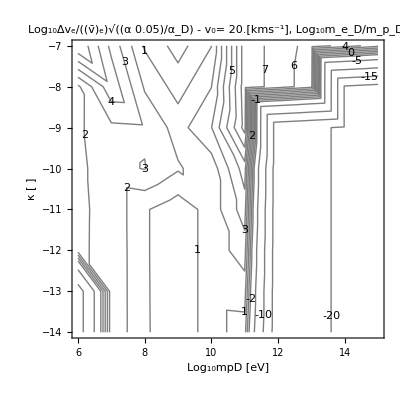

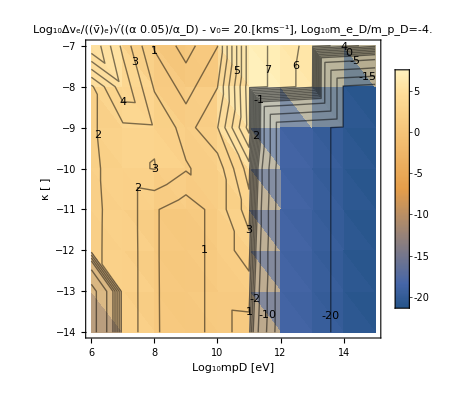

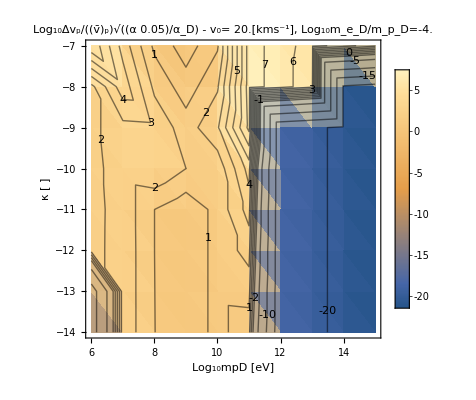

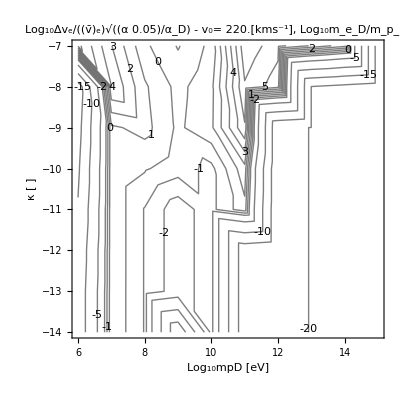

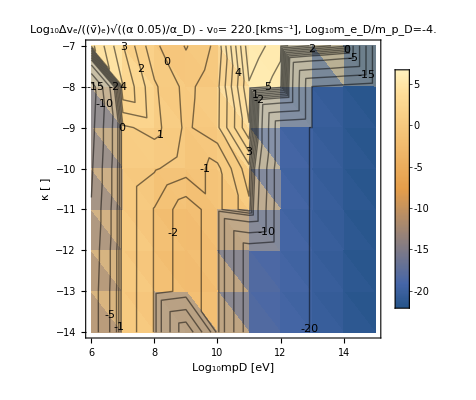

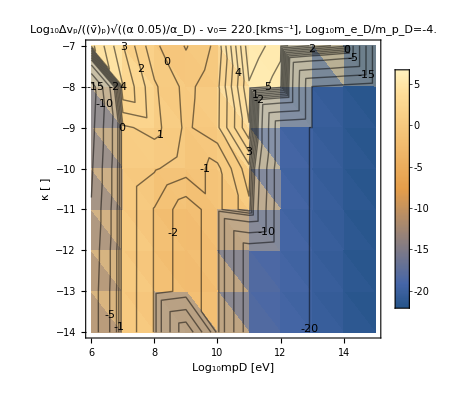

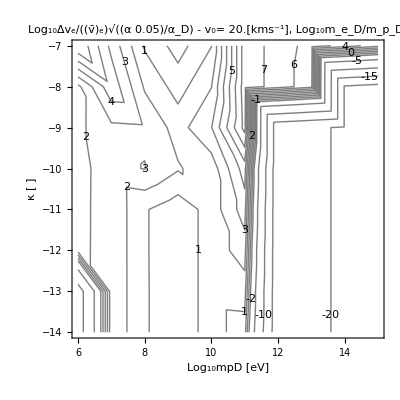

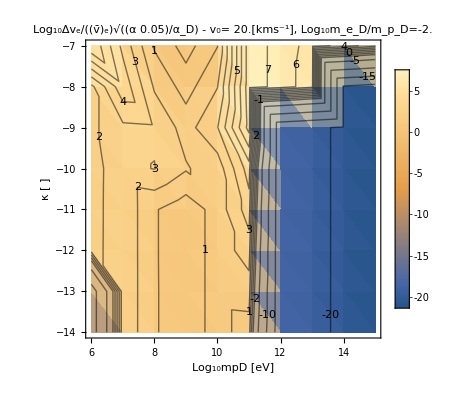

```mathematica
PlotKEchangeκContour[{PDicts1MeVKE,PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

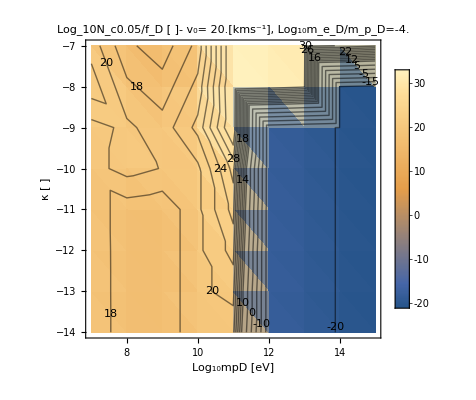

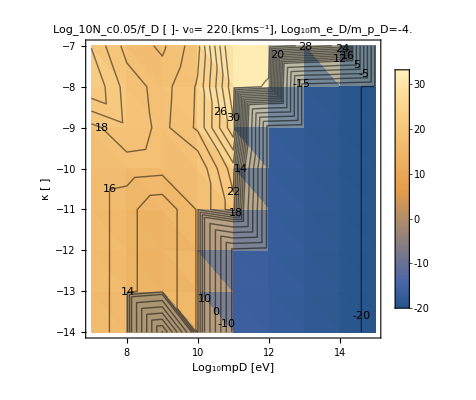

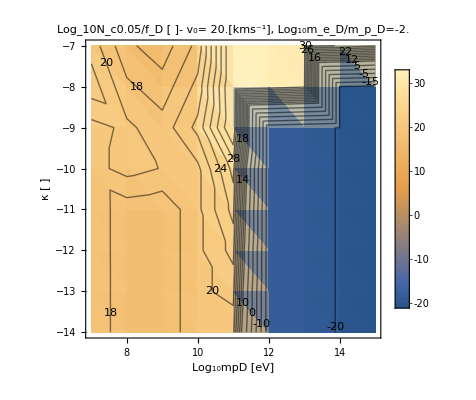

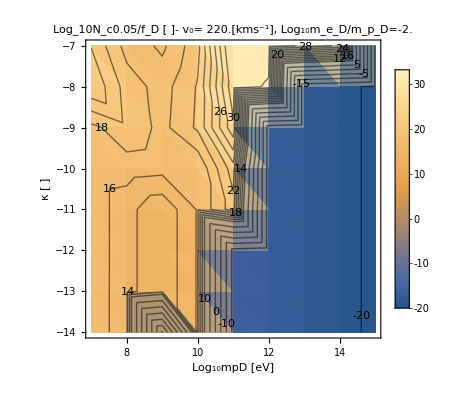

```mathematica
PlotNcκContour[{PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

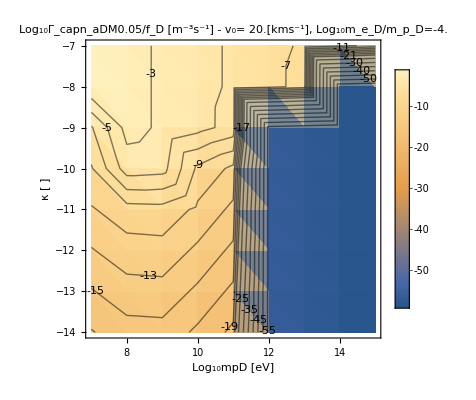

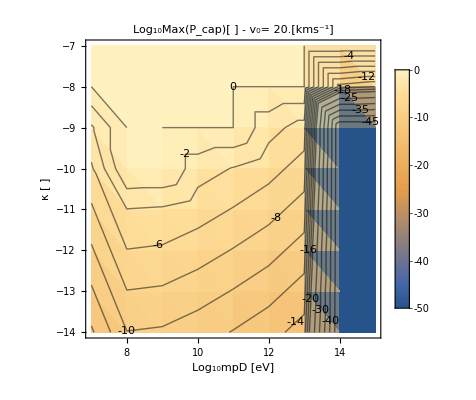

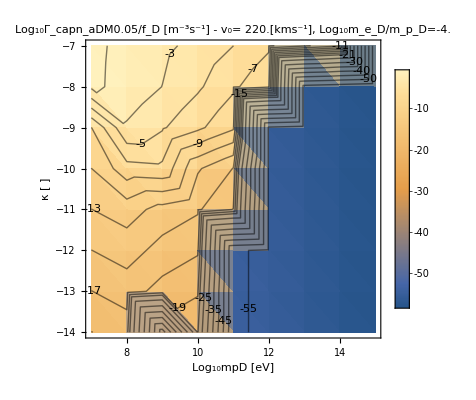

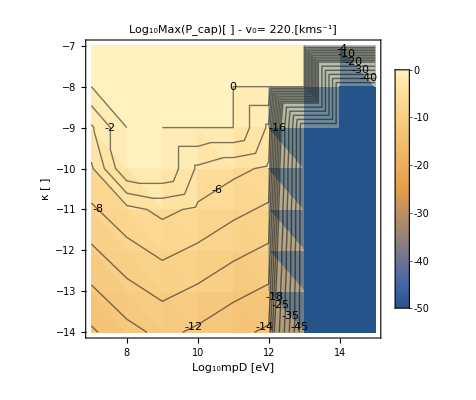

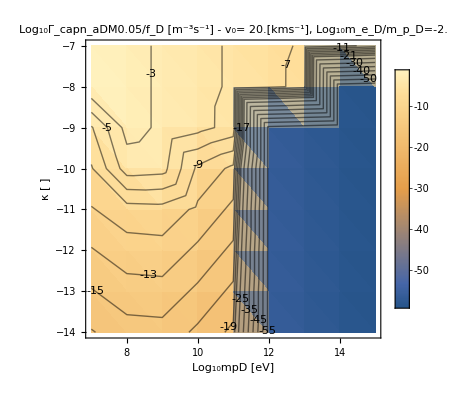

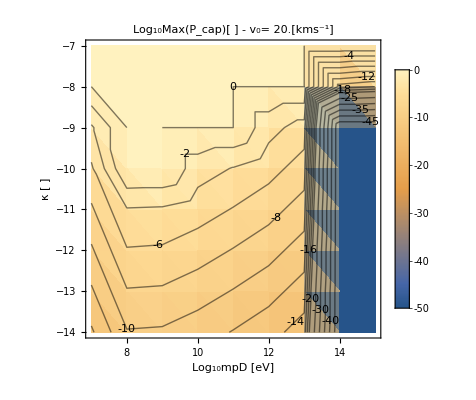

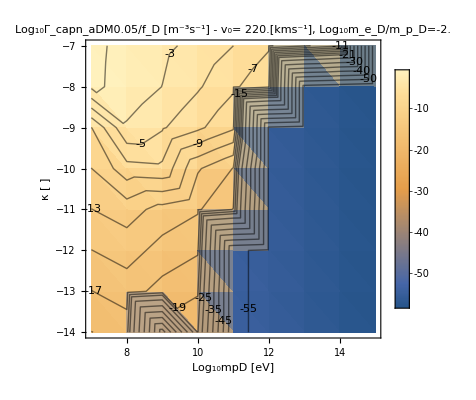

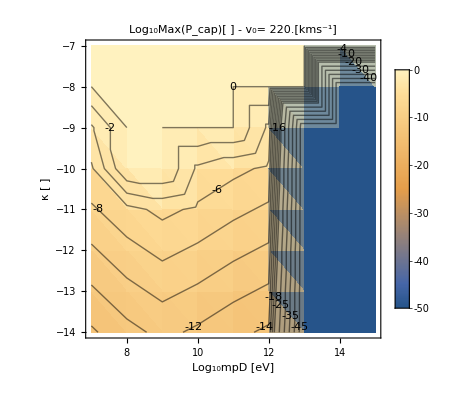

```mathematica
PlotCaptureRateκContour[{PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

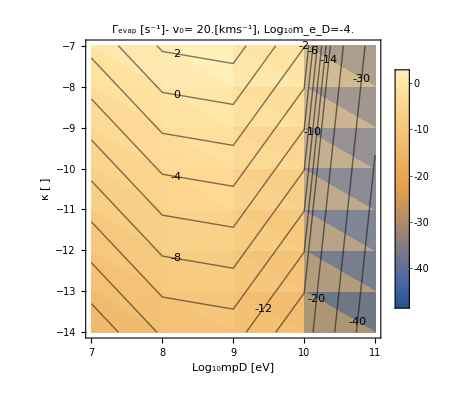

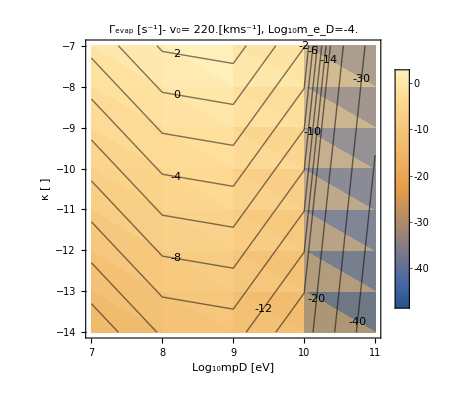

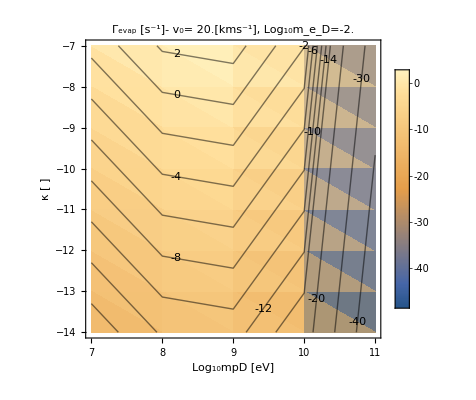

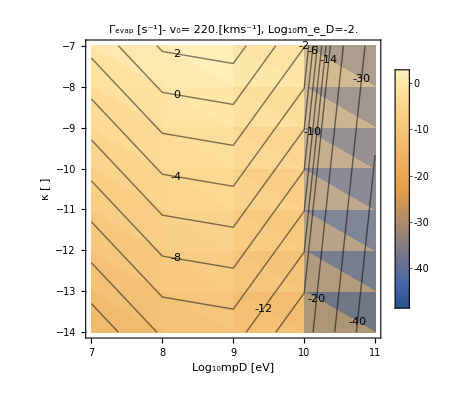

```mathematica
PlotEvaporationRateκContour[{PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

The reason this cuts off, is that Γevap =0 above 10 GeV

#### Soft Scatter Regime

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^6 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^6 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDict1MeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicst10MeVto1PeV[[eind ]],NuclearσDicst10MeVto1PeV[[Nucind ]]]
PlotPDist[PDict1MeV]
```

1

1

κ is: 1.×10^-14

Memory before 437670328

InterpolatingFunction::dmval: Input value {4.07801} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Memory after 450685120

κ is: 1.×10^-13

Memory before 450684832

Memory after 452359232

κ is: 1.×10^-12

Memory before 452358976

Memory after 453840752

κ is: 1.×10^-11

Memory before 453840496

Memory after 455223336

κ is: 1.×10^-10

Memory before 455223080

Memory after 456530728

κ is: 1.×10^-9

Memory before 456530472

Memory after 457853680

κ is: 1.×10^-8

Memory before 457853424

Memory after 459152176

κ is: 1.×10^-7

Memory before 459151920

Memory after 459667040

```mathematica
PlotPDist[PDict1MeV]
```

1.×10^6

220000

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

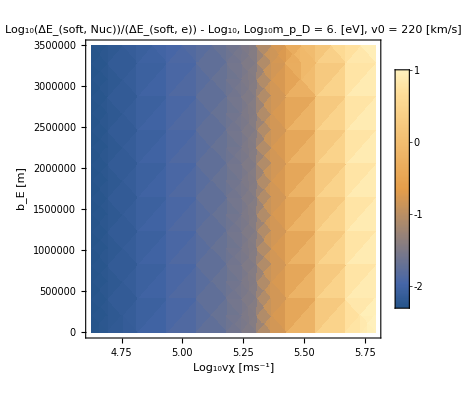

1.×10^6

220000

InterpolatingFunction::dmval: Input value {4.20052} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^6125.98 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/10^42959.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/10^6125.98 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

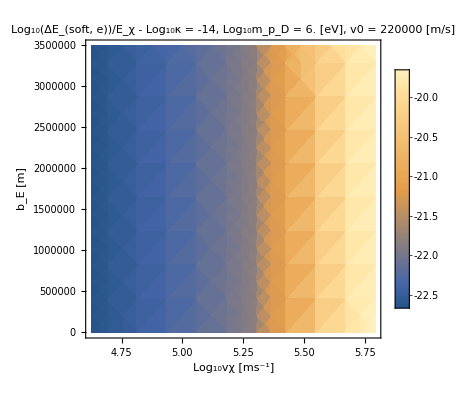

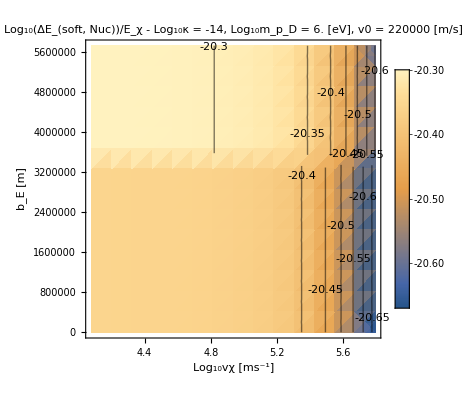

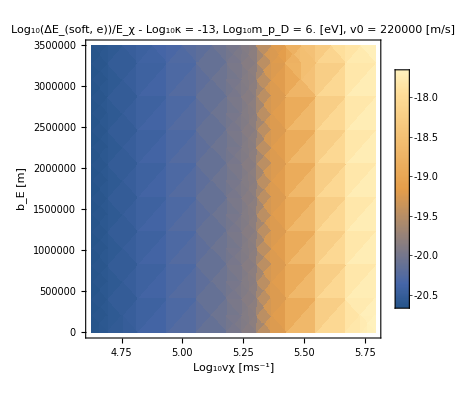

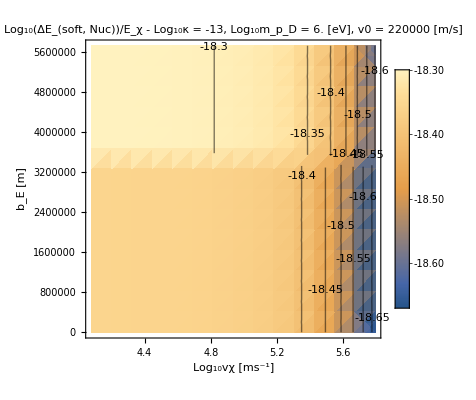

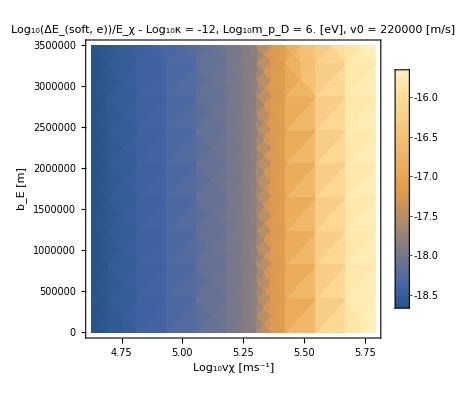

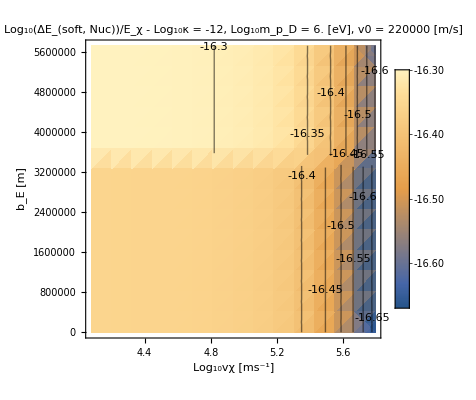

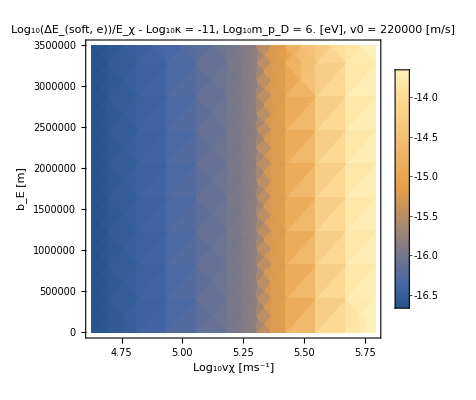

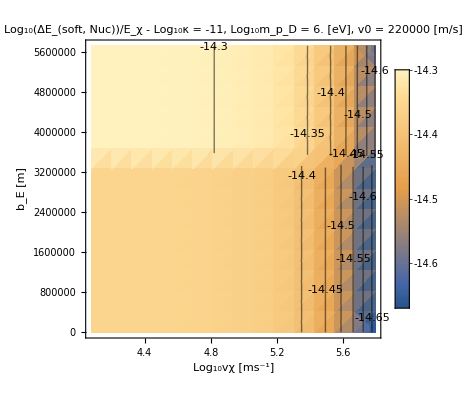

```mathematica
PlotELNucoverE[PDict1MeV,ElectronicσDicst10MeVto1PeV[[eind ]],NuclearσDicst10MeVto1PeV[[Nucind ]]]
PlotELfrac[PDict1MeV,ElectronicσDicst10MeVto1PeV[[eind ]],NuclearσDicst10MeVto1PeV[[Nucind ]]]
```

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^9 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^9 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDict1GeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicst10MeVto1PeV[[eind ]],NuclearσDicst10MeVto1PeV[[Nucind ]]]
PlotPDist[PDict1GeV]
```

4

4

κ is: 1.×10^-14

Memory before 684848280

InterpolatingFunction::dmval: Input value {4.07801} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

1.×10^9

220000

InterpolatingFunction::dmval: Input value {-26.7496,4.04934} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

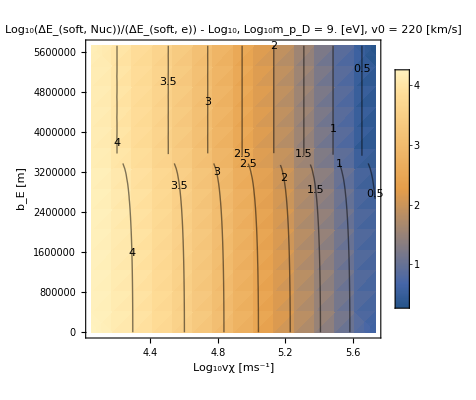

```mathematica
PlotELNucoverE[PDict1GeV]
```

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^10 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^10 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDict10GeV220=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicst10MeVto1PeV[[eind ]],NuclearσDicst10MeVto1PeV[[Nucind ]]]
PlotPDist[PDict10GeV220]
```

5

5

κ is: 1.×10^-14

Memory before 652145064

InterpolatingFunction::dmval: Input value {4.07801} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
PlotELNucoverE[PDict10GeV220]
PlotELNucoverE[PDict10GeV220,ElectronicσDicst10MeVto1PeV[[eind ]],NuclearσDicst10MeVto1PeV[[Nucind ]]]
PlotELfrac[PDict10GeV220,ElectronicσDicst10MeVto1PeV[[eind ]],NuclearσDicst10MeVto1PeV[[Nucind ]]]
```

1.×10^12

220000

InterpolatingFunction::dmval: Input value {-23.7496,4.04934} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

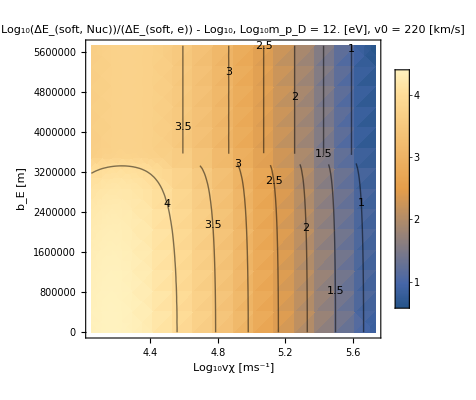

```mathematica
PlotELNucoverE[PDict1TeV]
```

## Misc Studies and Plots

### Interpolation

#### Test run after changing ϵ and temperature in mantle

```mathematica
test10TeVinterpolationFe1=Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigher[[1]],FeTotalparams[[i]],10,60,10^-6,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,1}];
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

### Plot total energy loss for various masses

#### Combined Plots for Core

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^53462.7 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^5734.2 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^4298.35 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

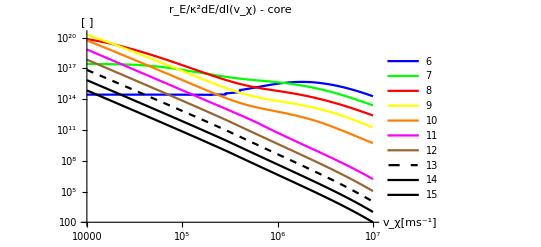

```mathematica
(*Legended@Show@*)
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate@Table[eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)("dEdlofr"/.GetTotalELFunction[ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]])[10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2)
,{m,6,15}],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[ ]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - core",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table[ToString[m],{m,6,15}]]]
```

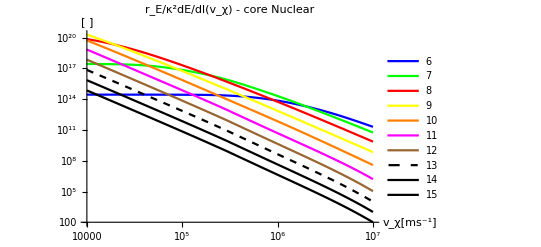

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};

LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)("dEdlofr"/.GetNucELFunction[NuclearσDicst10MeVto1PeV[[Nucind]]])[10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2)
,{m,6,15}]],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[ ]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - core Nuclear",PlotStyle->plotstyle,  PlotLegends->LineLegend[plotstyle,Evaluate[Table[ToString[m],{m,6,15}]]]]
```

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^53462.7 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^5734.2 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^50071.9 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

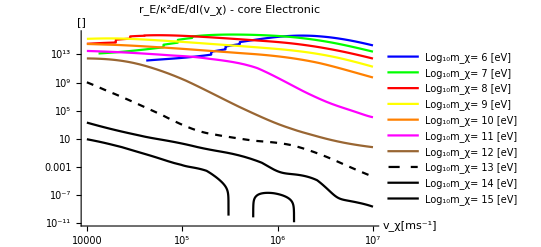

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicst10MeVto1PeV[[eind]]])[10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2))
,{m,6,15}]],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - core Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^53462.7 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^5734.2 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^50071.9 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

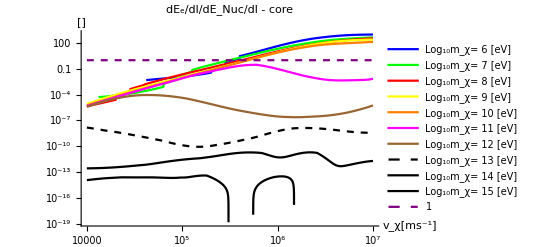

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin],Directive[Purple,Dashed]};
LogLogPlot[Evaluate[Append[Table[eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("dEdlofr"/.GeteELFunction[ElectronicσDicst10MeVto1PeV[[eind]]])[10^6,vχ])/(("dEdlofr"/.GetNucELFunction[NuclearσDicst10MeVto1PeV[[Nucind]]])[10^6,vχ])
,{m,6,15}],1]],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"dE_e/dl/dE_Nuc/dl - core",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Append[Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}],1]]]
```

#### Combined Plots for Mantle

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^429.843 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^309.015 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/10^466.527 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

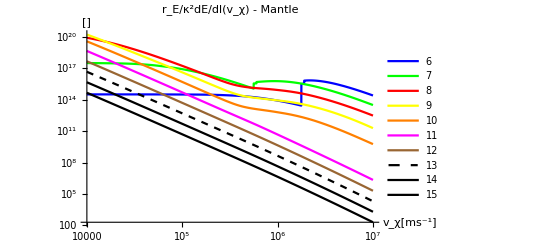

```mathematica
(*Legended@Show@*)
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate@Table[eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)("dEdlofr"/.GetTotalELFunction[ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]])[5 10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2)
,{m,6,15}],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - Mantle",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table[ToString[m],{m,6,15}]]]
```

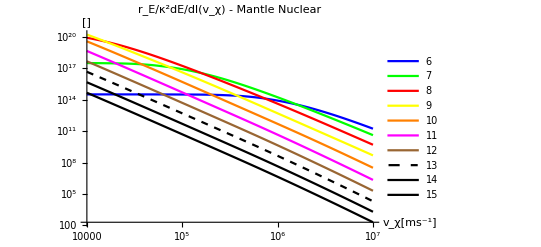

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};

LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)("dEdlofr"/.GetNucELFunction[NuclearσDicst10MeVto1PeV[[Nucind]]])[5 10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2)
,{m,6,15}]],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - Mantle Nuclear",PlotStyle->plotstyle,  PlotLegends->LineLegend[plotstyle,Evaluate[Table[ToString[m],{m,6,15}]]]]
```

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^429.843 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^309.015 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/10^466.527 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

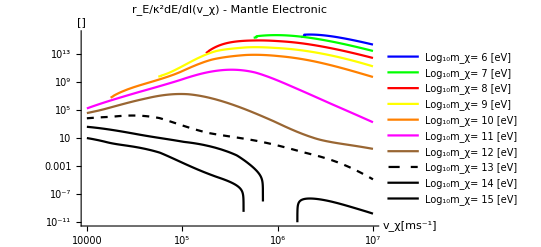

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicst10MeVto1PeV[[eind]]])[5 10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2))
,{m,6,15}]],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - Mantle Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^429.843 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^309.015 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/10^466.527 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

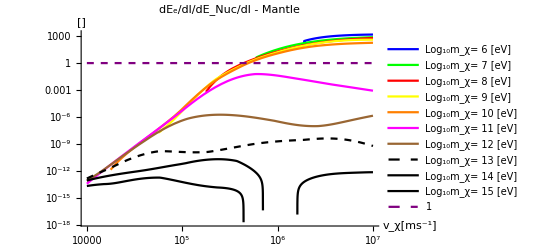

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin],Directive[Purple,Dashed]};
LogLogPlot[Evaluate[Append[Table[eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("dEdlofr"/.GeteELFunction[ElectronicσDicst10MeVto1PeV[[eind]]])[5 10^6,vχ])/(("dEdlofr"/.GetNucELFunction[NuclearσDicst10MeVto1PeV[[Nucind]]])[5 10^6,vχ])
,{m,6,15}],1]],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"dE_e/dl/dE_Nuc/dl - Mantle",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Append[Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}],1]]]
```

### Capture Rate and interaction length

#### Plot Capture Interaction Length Electronic

```mathematica
GetWeakCaptureInteractionLength[test10TeVinterpolationFe1[[1]]]
```

InterpolatingFunction::dmval: Input value {4.04928,-4.46691} lies outside the range of data in the interpolating function. Extrapolation will be used.

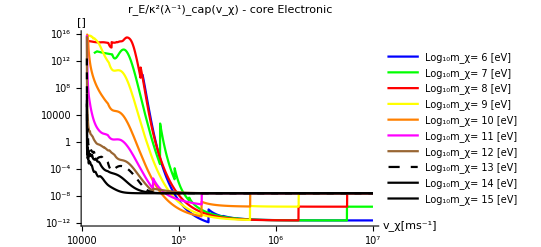

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotaleWeakCaptureInteractionLength[Gather[ElectronicσDicst10MeVto1PeV[[eind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ]
,{m,6,15}]],{vχ,"vesc"/.Constants`EarthRepl,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - core Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->All]
```

InterpolatingFunction::dmval: Input value {4.04928,-4.17969} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

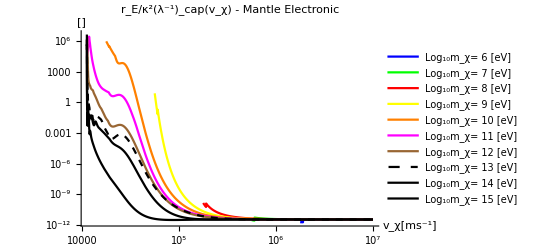

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotaleWeakCaptureInteractionLength[Gather[ElectronicσDicst10MeVto1PeV[[eind]],#1["regionindex"]==#2["regionindex"]&][[2]]][vχ]
,{m,6,15}]],{vχ,"vesc"/.Constants`EarthRepl,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Mantle Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->All]
```

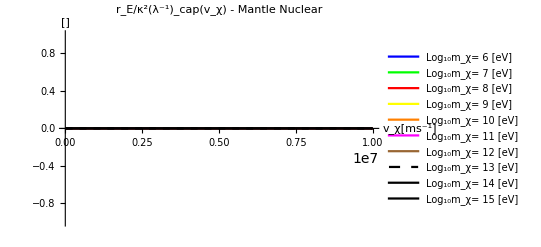

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
Plot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicst10MeVto1PeV[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]][vχ]
,{m,6,15}]],{vχ,"vesc"/.Constants`EarthRepl,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Mantle Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->All]
```

```mathematica
GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicst10MeVto1PeV[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]][10^6]
```

0

#### Plot Capture Interaction Length Nuclear

InterpolatingFunction::dmval: Input value {4.04922,-4.11584} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04922,-4.01065} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04922,-4.00144} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

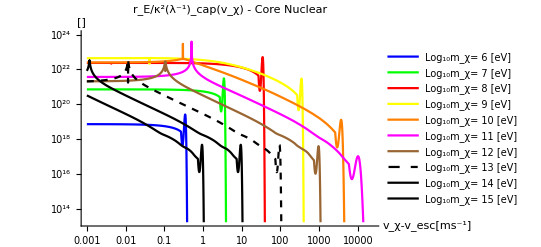

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicst10MeVto1PeV[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-3,10^5-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Core Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{0,10^24}]
```

InterpolatingFunction::dmval: Input value {4.04922,-4.77713} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04922,-7.33316} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04922,-4.47791} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

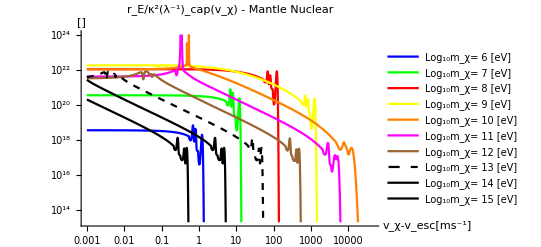

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicst10MeVto1PeV[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-3,10^5-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Mantle Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{0,10^24}]
```

```mathematica
"materialname"/.Gather[NuclearσDicst10MeVto1PeV[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]
```

{Si Nuc,Mg Nuc,O Nuc}

#### Plot Capture Interaction Length Total

InterpolatingFunction::dmval: Input value {4.04922,-4.11585} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04922,-4.01065} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04922,-4.00144} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

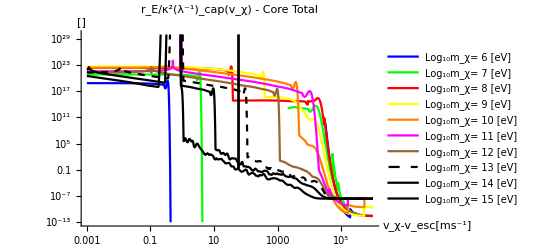

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)(GetTotaleWeakCaptureInteractionLength[Gather[ElectronicσDicst10MeVto1PeV[[eind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ+"vesc"/.Constants`EarthRepl]+GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicst10MeVto1PeV[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ+"vesc"/.Constants`EarthRepl])
,{m,6,15}]],{vχ,10^-3,10^6-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Core Total",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{0,10^30}]
```

InterpolatingFunction::dmval: Input value {4.04922,-4.00051} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04922,-4.00075} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04922,-4.00015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

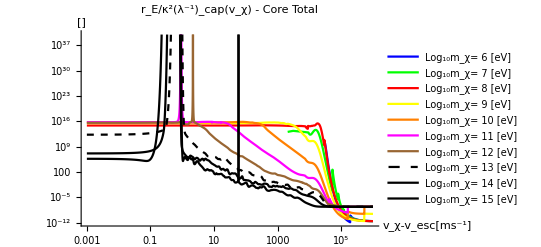

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)(GetTotaleWeakCaptureInteractionLength[Gather[ElectronicσDicst10MeVto1PeV[[eind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ+"vesc"/.Constants`EarthRepl])
,{m,6,15}]],{vχ,10^-3,10^6-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Core Total",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{0,10^40}]
```

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicst10MeVto1PeV[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-3,10^5-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Mantle Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{0,10^24}]
```

InterpolatingFunction::dmval: Input value {4.04922,-4.77713} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04922,-7.33316} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04922,-4.47791} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
"materialname"/.Gather[NuclearσDicst10MeVto1PeV[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]
```

{Si Nuc,Mg Nuc,O Nuc}

### Capture Rate and interaction length - Comparison after Mantle Temperature Change

Conclusion: no visible change

#### Combined Plots for Mantle

```mathematica
(*Legended@Show@*)
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate@Table[eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)("dEdlofr"/.GetTotalELFunction[ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]])[5 10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2)
,{m,6,15}],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - Mantle",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table[ToString[m],{m,6,15}]]]
```

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^429.843 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^309.015 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/10^466.527 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};

LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)("dEdlofr"/.GetNucELFunction[NuclearσDicst10MeVto1PeV[[Nucind]]])[5 10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2)
,{m,6,15}]],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - Mantle Nuclear",PlotStyle->plotstyle,  PlotLegends->LineLegend[plotstyle,Evaluate[Table[ToString[m],{m,6,15}]]]]
```

-Graphics-

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicst10MeVto1PeV[[eind]]])[5 10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2))
,{m,6,15}]],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - Mantle Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^429.843 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^309.015 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/10^466.527 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin],Directive[Purple,Dashed]};
LogLogPlot[Evaluate[Append[Table[eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("dEdlofr"/.GeteELFunction[ElectronicσDicst10MeVto1PeV[[eind]]])[5 10^6,vχ])/(("dEdlofr"/.GetNucELFunction[NuclearσDicst10MeVto1PeV[[Nucind]]])[5 10^6,vχ])
,{m,6,15}],1]],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"dE_e/dl/dE_Nuc/dl - Mantle",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Append[Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}],1]]]
```

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^429.843 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {4.00006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^309.015 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/10^466.527 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

#### Plot Capture Interaction Length Electronic

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotaleWeakCaptureInteractionLength[Gather[ElectronicσDicst10MeVto1PeV[[eind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ]
,{m,6,15}]],{vχ,"vesc"/.Constants`EarthRepl,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - core Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->All]
```

InterpolatingFunction::dmval: Input value {4.04928,-4.46691} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotaleWeakCaptureInteractionLength[Gather[ElectronicσDicst10MeVto1PeV[[eind]],#1["regionindex"]==#2["regionindex"]&][[2]]][vχ]
,{m,6,15}]],{vχ,"vesc"/.Constants`EarthRepl,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Mantle Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->All]
```

InterpolatingFunction::dmval: Input value {4.04928,-4.17969} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
Plot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicst10MeVto1PeV[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]][vχ]
,{m,6,15}]],{vχ,"vesc"/.Constants`EarthRepl,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Mantle Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->All]
```

-Graphics-

```mathematica
GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicst10MeVto1PeV[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]][10^6]
```

0

#### Plot Capture Interaction Length Nuclear

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicst10MeVto1PeV[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-3,10^5-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Core Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{0,10^24}]
```

InterpolatingFunction::dmval: Input value {4.04922,-4.11584} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04922,-4.01065} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04922,-4.00144} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicst10MeVto1PeV[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-3,10^5-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Mantle Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{0,10^24}]
```

InterpolatingFunction::dmval: Input value {4.04922,-4.77713} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04922,-7.33316} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04922,-4.47791} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
"materialname"/.Gather[NuclearσDicst10MeVto1PeV[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]
```

{Si Nuc,Mg Nuc,O Nuc}

### Evaporation Length

```mathematica
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^7 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
```

```mathematica
GetEvaporationRate[NuclearσDicst10MeVto1PeV[[Nucind,2]]]
```

11199.1

11200

{{0.049218,7.77815},{-4.,-0.0000434316}}

1.62064×10^8

0.

testing bounds

-0.0000434316

-4.

-4.

1.37417×10^9

```mathematica
N[Log[11199]/Log[10]]
```

4.04918

### Soft vs hard and nuclear vs electronic domination

```mathematica
Keys@PDicts100GeVKE[[1]]
PropertyList@("PfNuc"/.PDicts100GeVKE[[1]])
(*Table[("PfNuc"/.PDicts100GeVKE[[1]])[%[[i]]],{i,Length[%]}]*)
Max[("PfNuc"/.PDicts100GeVKE[[1]])["ValuesOnGrid"]]
```

{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD}

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,IndexedElementEvaluate,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,ParameterAddress,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid,VectorEvaluate}

-12.1135

```mathematica
Dimensions@KEDictList
```

{10,32}

```mathematica
Max[("PfNuc"/.PDicts100GeVKE[[1]])["ValuesOnGrid"]]
```

-12.1135

```mathematica
Table[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Max[("PfNuc"/.PDicts100GeVKE[[i]])["ValuesOnGrid"]]}/.PDicts100GeVKE[[i]],{i,Length[PDicts100GeVKE]}]
```

{{11.,-Log[100000000000000]/Log[10],-12.1135},{11.,-Log[10000000000000]/Log[10],-10.1135},{11.,-Log[1000000000000]/Log[10],-8.11346},{11.,-Log[100000000000]/Log[10],-6.11346},{11.,-Log[10000000000]/Log[10],-4.11348},{11.,-Log[1000000000]/Log[10],0.},{11.,-Log[100000000]/Log[10],0.},{11.,-Log[10000000]/Log[10],0.},{11.,-Log[100000000000000]/Log[10],-13.4604},{11.,-Log[10000000000000]/Log[10],-11.461},{11.,-Log[1000000000000]/Log[10],-9.46105},{11.,-Log[100000000000]/Log[10],-7.46105},{11.,-Log[10000000000]/Log[10],-5.46105},{11.,-Log[1000000000]/Log[10],0.},{11.,-Log[100000000]/Log[10],0.},{11.,-Log[10000000]/Log[10],0.},{11.,-Log[100000000000000]/Log[10],-12.1159},{11.,-Log[10000000000000]/Log[10],-10.1159},{11.,-Log[1000000000000]/Log[10],-8.11593},{11.,-Log[100000000000]/Log[10],-6.11593},{11.,-Log[10000000000]/Log[10],-4.11595},{11.,-Log[1000000000]/Log[10],0.},{11.,-Log[100000000]/Log[10],0.},{11.,-Log[10000000]/Log[10],0.},{11.,-Log[100000000000000]/Log[10],-13.4646},{11.,-Log[10000000000000]/Log[10],-11.4644},{11.,-Log[1000000000000]/Log[10],-9.46442},{11.,-Log[100000000000]/Log[10],-7.46442},{11.,-Log[10000000000]/Log[10],-5.46443},{11.,-Log[1000000000]/Log[10],0.},{11.,-Log[100000000]/Log[10],0.},{11.,-Log[10000000]/Log[10],0.}}

### Comparing to appendix

#### Capture rates and number density debug

```mathematica
"eVm"/.SIConstRepl
```

2.×10^-7

```mathematica
1/5 nD0ΛCDM[0.05,1/2 10^10 ("JpereV")/("c")^2/.SIConstRepl]
2.3 10^-17 (* eV^-3 value in appendix for the above params*)
% ("eVm")^-3/.SIConstRepl
```

0.00273075

2.3×10^-17

2875.

```mathematica
1/5 nD0ΛCDM[0.05,5 10^9 ("JpereV")/("c")^2/.SIConstRepl](*~Subscript[n, 0] - this is aDM with 0.05 fraction of mass compared to local SM baryon # ie. 0.01 fraction of DM*)
%
```

0.00273075

0.00273075

```mathematica
nD0ΛCDM[0.01,5 10^9 ("JpereV")/("c")^2/.SIConstRepl]
```

0.00273075

```mathematica
1/5 nD0ΛCDM[1,10^9 ("JpereV")/("c")^2/.SIConstRepl]
```

0.273075

```mathematica
"mpD"/.PDicts10GeVScan
10^10 ("JpereV")/("c")^2/.SIConstRepl
```

{{1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26},{1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26},{1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26},{1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26}}

1.78×10^-26

Compare rough scaling of our capture rate to theirs:

```mathematica
("mpD" "βD")^(3/2)ⅇ^(-1/2 "mpD" (vχ^2-("vesc")^2)"βD")/.PDicts10GeVKE[[1]]/.EarthRepl//Simplify;
Integrate[% vχ^3,vχ]
(Limit[%,vχ->∞])-(%/.vχ->0)
```

4.7056×10^-12 ⅇ^(-7.49925×10^-9 vχ^2) (-8.89067×10^15-6.66733×10^7 vχ^2)

41835.9

```mathematica
("mpD" "βD")^(3/2)ⅇ^(-1/2 "mpD" (-("vesc")^2)"βD")/.EarthRepl
```

```mathematica
Integrate[  bE^2/(√(1 + bE^2/("rE")^2)),bE]
(%/.bE->"rE"//FullSimplify)-(%/.bE->0)/.EarthRepl
```

1/2 rE^2 (bE √(1+bE^2/rE^2)-rE ArcSinh[bE/rE])

6.88953×10^19

Discrepancy with appendix is that for us dNc/dt~<v_χ> (r^2)_E n_F whereas for them dNc/dt~<v_χ>1/r_E

So I think it is a discrepancy of definition, the rates to compare to them is R n_F ~ <v_χ>n_F/r_E  which is the rate per unit volume in Earth, so for us the comparison is R n_F ~ <v_χ>n_F/r_E ~ 1/V_E dNc/dt

```mathematica
4/3 π("rE")^3/.EarthRepl
```

1.08321×10^21

## Scrap

#### Test Plotting to Export only

```mathematica
p1=Show[{Plot[x^2,{x,0,10}],Plot[x^4,{x,0,10}]}];
```

```mathematica
Export[NotebookDirectory[]<>"testplot.png",p1]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\testplot.png

```mathematica
Export[NotebookDirectory[]<>"testplot_1.png",p1]
Export[NotebookDirectory[]<>"testplot_2.png",p1]
Export[NotebookDirectory[]<>"testplot_3.png",p1]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\testplot_1.png

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\testplot_2.png

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\testplot_3.png

```mathematica
DateString[{"Day","_","Month","_","Year"}]
```

07_06_2024

```mathematica
ExportToDir[p1,"testplot.png","testplots"]
```

<|path→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Plots/testplots/testplot_4.png,directory→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Plots/testplots|>

```mathematica
FileExistsQ["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Plots/07_06_2024/testplot.png"]
```

True

#### Unit test Δr

```mathematica
testΔEfunc=("ΔEthroughEarth"/.GetTotalELFunction[ElectronicσDicstallmasses[[3]],NuclearσDicstallmasses[[3]]])
%[10^6,10^4]
```

Quiet[Re[Piecewise[{{dM[#1] dEdlofr$127435[1.1 rc$127435,#2]+dc[#1] dEdlofr$127435[0.9 rc$127435,#2], rc$127435^2>#1^2}, {dM[#1] dEdlofr$127435[1.1 rc$127435,#2], rE$127435^2>#1^2≥rc$127435^2}, {0, True}}]]]&

81.4556

{mpD→1.78×10^-28,mpD→1.78×10^-27,mpD→1.78×10^-26,mpD→1.78×10^-25,mpD→1.78×10^-24}

```mathematica
("mpD" ("c")^2)/("JpereV")/.Constants`SIConstRepl/.mpDPoints[[3]]
```

1.×10^10

```mathematica
κtest = 10^-9;
ΔrTotbyκsquared["mpD"/.mpDPoints[[3]],10^5,10^5,testΔEfunc]
%/κtest^2
```

1.0043×10^-11

1.0043×10^7

#### Modify exporting for plots

```mathematica
ToString@StringForm["Pcap_total_mpD_``_``_``",Log10[10^12],1,7]
StringQ[%]
```

Pcap_total_mpD_12_1_7

True

{0,0,0,0,0}

1

1

mpD: 1.×10^6

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^21

κ is: 1.×10^-14

Memory before 219512728

InterpolatingFunction::dmval: Input value {4.05162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Memory after 233200848

κ is: 1.×10^-13

Memory before 233200592

Memory after 234740288

κ is: 1.×10^-12

Memory before 234740032

Memory after 236168208

κ is: 1.×10^-11

Memory before 236167952

Memory after 237543936

κ is: 1.×10^-10

Memory before 237543680

Memory after 240846672

κ is: 1.×10^-9

Memory before 240846416

Memory after 242163760

κ is: 1.×10^-8

Memory before 242163504

Memory after 243485840

κ is: 1.×10^-7

Memory before 243485584

Memory after 244000264

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {42405.7}. NIntegrate obtained 8.60226×10^15 and 8.60457×10^11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {42405.7}. NIntegrate obtained 8.60649×10^17 and 6.61047×10^13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {42405.7}. NIntegrate obtained 8.58398×10^19 and 6.94213×10^15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^19

κ is: 1.×10^-14

Memory before 399029768

Memory after 400365600

κ is: 1.×10^-13

Memory before 400365344

Memory after 401624384

κ is: 1.×10^-12

Memory before 401624128

Memory after 402918960

κ is: 1.×10^-11

Memory before 402918704

Memory after 404203232

κ is: 1.×10^-10

Memory before 404203232

Memory after 405476480

κ is: 1.×10^-9

Memory before 405476480

Memory after 406757352

κ is: 1.×10^-8

Memory before 406757352

Memory after 408028984

κ is: 1.×10^-7

Memory before 408028984

Memory after 408543512

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^21

κ is: 1.×10^-14

Memory before 416350400

Memory after 417620480

κ is: 1.×10^-13

Memory before 417620224

Memory after 418867128

κ is: 1.×10^-12

Memory before 418866872

Memory after 420169112

κ is: 1.×10^-11

Memory before 420169112

Memory after 421416360

κ is: 1.×10^-10

Memory before 421416360

Memory after 422665600

κ is: 1.×10^-9

Memory before 422665600

Memory after 423941608

κ is: 1.×10^-8

Memory before 423941608

Memory after 425205032

κ is: 1.×10^-7

Memory before 425205032

Memory after 425719752

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^19

κ is: 1.×10^-14

Memory before 422011224

Memory after 423276792

κ is: 1.×10^-13

Memory before 423276792

Memory after 424544872

κ is: 1.×10^-12

Memory before 424544872

Memory after 425762944

κ is: 1.×10^-11

Memory before 425762944

Memory after 427041200

κ is: 1.×10^-10

Memory before 427041200

Memory after 428305976

κ is: 1.×10^-9

Memory before 428305976

Memory after 429572448

κ is: 1.×10^-8

Memory before 429572448

Memory after 430817912

κ is: 1.×10^-7

Memory before 430817912

Memory after 431332304

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→73429.,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→False,Nc→1.08118×10^-14 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→73429.,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^-32 nD,NcMax→1.08118×10^-14 nD,timeenoughforequil→True,Nc→1.49846×10^-15 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→73429.,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→0.0746016 nD,NcMax→1.04245×10^16 nD,timeenoughforequil→True,Nc→1.44478×10^13 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→73429.,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.46382 nD,NcMax→1.04296×10^18 nD,timeenoughforequil→True,Nc→1.44549×10^13 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→73429.,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→744.43 nD,NcMax→1.04023×10^20 nD,timeenoughforequil→True,Nc→1.44171×10^13 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→73429.,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→74269.6 nD,NcMax→1.03781×10^22 nD,timeenoughforequil→True,Nc→1.43835×10^13 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→73429.,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.4113×10^6 nD,NcMax→1.03562×10^24 nD,timeenoughforequil→True,Nc→1.43532×10^13 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→73429.,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→1.49846×10^23 nD,Γtotal→5.16352×10^9|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→778994.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→0.55833 nD,NcMax→7.80185×10^16 nD,timeenoughforequil→False,Nc→7.80185×10^16 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→778994.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4250.9 nD,NcMax→5.94001×10^20 nD,timeenoughforequil→True,Nc→8.23256×10^19 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→778994.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→436276. nD,NcMax→6.09633×10^22 nD,timeenoughforequil→True,Nc→8.4492×10^19 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→778994.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.36208×10^7 nD,NcMax→6.09537×10^24 nD,timeenoughforequil→True,Nc→8.44787×10^19 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→778994.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.36133×10^9 nD,NcMax→6.09432×10^26 nD,timeenoughforequil→True,Nc→8.44642×10^19 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→778994.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.36063×10^11 nD,NcMax→6.09335×10^28 nD,timeenoughforequil→True,Nc→8.44508×10^19 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→778994.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.35997×10^13 nD,NcMax→6.09242×10^30 nD,timeenoughforequil→True,Nc→8.44379×10^19 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→778994.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44219×10^19 nD,NcMax→6.20731×10^36 nD,timeenoughforequil→True,Nc→8.60302×10^23 nD,Γtotal→5.16352×10^9|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→73766.,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→False,Nc→1.08141×10^-14 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→73766.,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^-32 nD,NcMax→1.08141×10^-14 nD,timeenoughforequil→True,Nc→1.49878×10^-15 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→73766.,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→0.0769438 nD,NcMax→1.07518×10^16 nD,timeenoughforequil→True,Nc→1.49014×10^13 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→73766.,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.65367 nD,NcMax→1.06949×10^18 nD,timeenoughforequil→True,Nc→1.48226×10^13 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→73766.,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→763.447 nD,NcMax→1.06681×10^20 nD,timeenoughforequil→True,Nc→1.47854×10^13 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→73766.,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→76167.3 nD,NcMax→1.06433×10^22 nD,timeenoughforequil→True,Nc→1.4751×10^13 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→73766.,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.60069×10^6 nD,NcMax→1.06209×10^24 nD,timeenoughforequil→True,Nc→1.472×10^13 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→73766.,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→True,Nc→1.49878×10^23 nD,Γtotal→5.16352×10^9|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→782837.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.38707 nD,NcMax→1.93823×10^17 nD,timeenoughforequil→False,Nc→1.93823×10^17 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→782837.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4363.77 nD,NcMax→6.09773×10^20 nD,timeenoughforequil→True,Nc→8.45115×10^19 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→782837.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→445717. nD,NcMax→6.22824×10^22 nD,timeenoughforequil→True,Nc→8.63203×10^19 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→782837.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.45607×10^7 nD,NcMax→6.22671×10^24 nD,timeenoughforequil→True,Nc→8.62991×10^19 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→782837.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.45532×10^9 nD,NcMax→6.22566×10^26 nD,timeenoughforequil→True,Nc→8.62845×10^19 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→782837.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.45462×10^11 nD,NcMax→6.22468×10^28 nD,timeenoughforequil→True,Nc→8.6271×10^19 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→782837.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.45393×10^13 nD,NcMax→6.22372×10^30 nD,timeenoughforequil→True,Nc→8.62577×10^19 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→782837.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46378×10^19 nD,NcMax→6.23748×10^36 nD,timeenoughforequil→True,Nc→8.64484×10^23 nD,Γtotal→5.16352×10^9|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1MeVScan.dat

{4,4,4,4,4}

```mathematica
reachedcounter
```

{4,4,4,4,4}

#### Scaling estimates for inner shell electrons

```mathematica
1/(Z m α)/.{α->1/137,m->0.5 10^6,Z-> 26}
```

0.0000105385

```mathematica
(Z^2 m α^2)/2/.{α->1/137,m->0.5 10^6,Z-> 26}
Log10@%
```

9004.21

3.95445

```mathematica
N@Log10[9000]
```

3.95424

```mathematica
13 Z^2/.{α->1/137,m->0.5 10^6,Z-> 26}
```

8788

```mathematica
file = OpenWrite[]
Write[file,"hello"]
Write[file,"world"]
Close[file]
FilePrint[%]
```

OutputStream[…]

C:\Users\keega\AppData\Local\Temp\m-71d2e4e6-c113-403b-8d81-418357d10e8c

"hello"
"world"

```mathematica
Clear[logname]
logname = NotebookDirectory[]<>"log.txt"
Export[logname,"hello"]
Export[logname,"world"]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\log.txt

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\log.txt

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\log.txt

```mathematica
Close[logname]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\log.txt

```mathematica
Clear[logname]
logname = NotebookDirectory[]<>"log.txt"
logstrm = OpenWrite[logname]
Write[logstrm,"hello world"]
Write[logstrm,"world hello"]
Close[logstrm]
FilePrint[logname]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\log.txt

OutputStream[…]

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\log.txt

"hello world"
"world hello"

```mathematica
Clear[logname]
logname = NotebookDirectory[]<>"log.txt"
logstrm = OpenAppend[logname]
Write[logstrm,"hello world"]
FilePrint[logname]
Write[logstrm,"world hello"]
FilePrint[logname]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\log.txt

OutputStream[…]

"hello world"
"world hello"
"hello world"
"hello world"
"world hello"
"hello world"
"world hello"

#### How can electronic scattering Dominate for high masses?

```mathematica
"vF"/.FeTotalparams
```

{1.68373×10^6,2.06517×10^6,2.71326×10^6,5.26776×10^6,2.67232×10^7,1.2253×10^8}

```mathematica
Ee = 10^4 
me = 10^6
Ee/me==1/(√(1 - v^2))
Solve[%,v]
```

10000

1000000

1/100==1/(√(1-v^2))

{{v→-3 ⅈ √1111},{v→3 ⅈ √1111}}

```mathematica
"ωi""ℏ"("JpereV")^-1/.FeTotalparams/.SIConstRepl
```

{11.9774,16.2698,24.5012,66.281,757.327,7435.56}

```mathematica
Keys@FeTotalparams
```

{{hbar,ℏ,c,m,e,β,ne,qF,vF,μ,ωp,α,χ,ϵ0,JpereV,kB,D,nI,Z,M,EF,ωi,νi,Ai,ωedgei},{hbar,ℏ,c,m,e,β,ne,qF,vF,μ,ωp,α,χ,ϵ0,JpereV,kB,D,nI,Z,M,EF,ωi,νi,Ai,ωedgei},{hbar,ℏ,c,m,e,β,ne,qF,vF,μ,ωp,α,χ,ϵ0,JpereV,kB,D,nI,Z,M,EF,ωi,νi,Ai,ωedgei},{hbar,ℏ,c,m,e,β,ne,qF,vF,μ,ωp,α,χ,ϵ0,JpereV,kB,D,nI,Z,M,EF,ωi,νi,Ai,ωedgei},{hbar,ℏ,c,m,e,β,ne,qF,vF,μ,ωp,α,χ,ϵ0,JpereV,kB,D,nI,Z,M,EF,ωi,νi,Ai,ωedgei},{hbar,ℏ,c,m,e,β,ne,qF,vF,μ,ωp,α,χ,ϵ0,JpereV,kB,D,nI,Z,M,EF,ωi,νi,Ai,ωedgei}}

Try to find relationship between fermi velocity and energy of the shell

```mathematica
ne = (m ω^2)/α
vFe = ((3 π^2 ne)^(1/3))/m//PowerExpand
```

(m ω^2)/α

(3^(1/3) π^(2/3) ω^(2/3))/(m^(2/3) α^(1/3))

```mathematica
(Ee/me)^(2/3) (3 137 π^2)^(1/3)//N
```

0.740254

```mathematica
"D"/.FeTotalparams
"D"/.SiO2Totalparams
"D"/.MgOTotalparams
```

{322.436,485.073,837.295,3156.08,81222.,1.70758×10^6}

{801.791,2326.72}

{412.839,736.197,841.135,2012.33}

```mathematica
ω/(vF k)==k/(2 kF)//Solve
```

{{ω→(k^2 vF)/(2 kF)}}

```mathematica
mχmax = 10^15 (*PeV in eV*)
vmin=(10^4/(3 10^8))(*vesc in c - typical for large masses*)
vFironmax = 1
Etypical = me  vFironmax vmin (*118 of Tongyan's tasi lecture*)
Ekinmax = mχmax vmin^2
```

1000000000000000

1/30000

1

100/3

10000000/9

So PeV can' t easily be captured

What about a TeV on the plasma frequency for the energy transfer

```mathematica
mχmax = 10^12 (*TeV in eV*)
vmin=(10^4/(3 10^8))(*vesc in c - typical for large masses*)
vFironmax = 1
Etypical = 10^4 (*118 of Tongyan's tasi lecture*)
Ekinmax = mχmax vmin^2
```

1000000000000

1/30000

1

10000

10000/9

This fits!

```mathematica
mχmax = 10^15 (*PeV in eV*)
vmin=(10^4/(3 10^8))(*vesc in c - typical for large masses*)
vFironmax = 1
Etypical = 10^4 (*118 of Tongyan's tasi lecture*)
Ekinmax = mχmax vmin^2
```

1000000000000000

1/30000

1

10000

10000000/9

But we also have that for typical iron max, the energy of the electron is about an MeV near the fermi sphere

```mathematica
mχmax = 10^12 (*PeV in eV*)
vχ={10^-3,10^-4}(*v0 in c - typical for large masses*)
vFironmax = 1
Etypical = me vFironmax vχ (*118 of Tongyan's tasi lecture*)
Ekinmax = mχmax vχ^2
```

1000000000000

{1/1000,1/10000}

1

{me/1000,me/10000}

{1000000,10000}

#### ODE solving for trajectory - psuedo-code

Psuedo code for ODE solver:
ODE is  l’’ = - f(l,l’)
define y = l’
so we have instead the system
y’ = - f(l,y)
l’= y

so the algorithm is:
1) initialize y = v0, l = 0, h = RE/N, make tables of size N for l and y 
	- RE is path length through earth (2 √(r_E^2-b_E^2))
	- N is number of steps

2) Evolve using euler or second order RK
 a) for i in range N:
	 y[i+1] = y[i] - f(l[i],y[i]) h 
	 l[i+1] = l[i] + h y[i]
	 
	 if l >= RE/2 or y < vesc:
	 	return list of l and y (interpolate?)
 b) for i in range N:

*** don’t even need this, this is wrong, we essentially have a 1st order ode

Psuedo code for ODE solver:
ODE is  v’ = - f(l,v)
So we step in l

so the algorithm is:
1) initialize v = v0, l = 0, h = RE/N, make tables of size N for l and y 
	- RE is path length through earth (2 √(r_E^2-b_E^2))
	- N is number of steps

2) Evolve using euler or second order RK
 a) for i in range N:
	 v[i+1] = v[i] - f(l[i],y[i]) h 
	 l[i+1] = l[i] + h
	 
	 if l >= RE/2 or y < vesc:
	 	return list of l and y (interpolate?)
 b) for i in range N:

#### Timing of ODE traj solving algs

No break

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1GeVScan=AbsoluteTiming@GetCaptureRate["meD/mpD"/.meDPoints[[1]], 10^-10,v0Points[[1]],ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1GeVScan",PDicts1GeVScan[[2]]]
Clear[PDicts1GeVScan]
reachedcounter1GeV = reachedcounter
```

{0,0,0,0,0}

3

3

InterpolatingFunction::dmval: Input value {4.05162,-0.0000843029} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{48.2029,{<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00787521,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00801566,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00847399,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→3.8226×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00933292,RE→1.01936×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→11262.2,bEarth→5.0968×10^6,vfinal→11262.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0124439,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00809667,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00824158,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00871501,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→3.8226×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00960664,RE→1.01936×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→11447.7,bEarth→5.0968×10^6,vfinal→11447.7,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0128089,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00902573,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00918942,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00972658,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→12186.3,bEarth→3.8226×10^6,vfinal→12186.3,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0107571,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→12186.3,bEarth→5.0968×10^6,vfinal→12186.3,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0143428,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→7.10015×10^-9,CSDcap→False,vχE→15126.4,bEarth→6.371,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0135506,RE→1.2742×10^7,PcapE→7.10015×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→7.10015×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→6.60929×10^-9,CSDcap→False,vχE→15126.4,bEarth→1.27421×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0138075,RE→1.24846×10^7,PcapE→6.60929×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→6.60929×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→4.84444×10^-9,CSDcap→False,vχE→15126.4,bEarth→2.5484×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0146628,RE→1.16782×10^7,PcapE→4.84444×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→4.84444×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→15126.4,bEarth→3.8226×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0164034,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→15126.4,bEarth→5.0968×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0218712,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→2.23907×10^-7,CSDcap→False,vχE→26831.2,bEarth→6.371,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0504192,RE→1.2742×10^7,PcapE→2.23907×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→2.23907×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→2.08427×10^-7,CSDcap→False,vχE→26831.2,bEarth→1.27421×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0514914,RE→1.24846×10^7,PcapE→2.08427×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→2.08427×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→1.52772×10^-7,CSDcap→False,vχE→26831.2,bEarth→2.5484×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0551901,RE→1.16782×10^7,PcapE→1.52772×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→1.52772×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→26831.2,bEarth→3.8226×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0638308,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→26831.2,bEarth→5.0968×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0851077,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1GeVScan.dat

{0,0,0,0,0}

W break

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1GeVScan=AbsoluteTiming@GetCaptureRate["meD/mpD"/.meDPoints[[1]], 10^-10,v0Points[[1]],ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1GeVScan",PDicts1GeVScan[[2]]]
Clear[PDicts1GeVScan]
reachedcounter1GeV = reachedcounter
```

{0,0,0,0,0}

3

3

InterpolatingFunction::dmval: Input value {4.05162,-0.0000843029} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{47.3853,{<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00787521,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00801566,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00847399,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→3.8226×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00933292,RE→1.01936×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→11262.2,bEarth→5.0968×10^6,vfinal→11262.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0124439,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00809667,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00824158,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00871501,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→3.8226×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00960664,RE→1.01936×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→11447.7,bEarth→5.0968×10^6,vfinal→11447.7,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0128089,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00902573,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00918942,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00972658,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→12186.3,bEarth→3.8226×10^6,vfinal→12186.3,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0107571,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→12186.3,bEarth→5.0968×10^6,vfinal→12186.3,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0143428,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→7.10015×10^-9,CSDcap→False,vχE→15126.4,bEarth→6.371,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0135506,RE→1.2742×10^7,PcapE→7.10015×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→7.10015×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→6.60929×10^-9,CSDcap→False,vχE→15126.4,bEarth→1.27421×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0138075,RE→1.24846×10^7,PcapE→6.60929×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→6.60929×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→4.84444×10^-9,CSDcap→False,vχE→15126.4,bEarth→2.5484×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0146628,RE→1.16782×10^7,PcapE→4.84444×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→4.84444×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→15126.4,bEarth→3.8226×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0164034,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→15126.4,bEarth→5.0968×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0218712,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→2.23907×10^-7,CSDcap→False,vχE→26831.2,bEarth→6.371,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0504192,RE→1.2742×10^7,PcapE→2.23907×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→2.23907×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→2.08427×10^-7,CSDcap→False,vχE→26831.2,bEarth→1.27421×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0514914,RE→1.24846×10^7,PcapE→2.08427×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→2.08427×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→1.52772×10^-7,CSDcap→False,vχE→26831.2,bEarth→2.5484×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0551901,RE→1.16782×10^7,PcapE→1.52772×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→1.52772×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→26831.2,bEarth→3.8226×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0638308,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→26831.2,bEarth→5.0968×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0851077,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1GeVScan.dat

{0,0,0,0,0}

NDsolve v(l) no stop condition

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1GeVScan=AbsoluteTiming@GetCaptureRate["meD/mpD"/.meDPoints[[1]], 10^-10,v0Points[[1]],ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1GeVScan",PDicts1GeVScan[[2]]]
Clear[PDicts1GeVScan]
reachedcounter1GeV = reachedcounter
```

{0,0,0,0,0}

3

3

InterpolatingFunction::dmval: Input value {4.05162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{45.0824,{<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00787521,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00801566,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00847399,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→3.8226×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00933292,RE→1.01936×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→11262.2,bEarth→5.0968×10^6,vfinal→11262.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0124439,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00809667,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00824158,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00871501,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→3.8226×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00960664,RE→1.01936×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→11447.7,bEarth→5.0968×10^6,vfinal→11447.7,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0128089,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00902573,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00918942,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00972658,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→12186.3,bEarth→3.8226×10^6,vfinal→12186.3,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0107571,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→12186.3,bEarth→5.0968×10^6,vfinal→12186.3,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0143428,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→7.09914×10^-9,CSDcap→False,vχE→15126.4,bEarth→6.371,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0135506,RE→1.2742×10^7,PcapE→7.09914×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→7.09914×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→6.60929×10^-9,CSDcap→False,vχE→15126.4,bEarth→1.27421×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0138075,RE→1.24846×10^7,PcapE→6.60929×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→6.60929×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→4.84444×10^-9,CSDcap→False,vχE→15126.4,bEarth→2.5484×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0146628,RE→1.16782×10^7,PcapE→4.84444×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→4.84444×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→15126.4,bEarth→3.8226×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0164034,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→15126.4,bEarth→5.0968×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0218712,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→2.23875×10^-7,CSDcap→False,vχE→26831.2,bEarth→6.371,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0504192,RE→1.2742×10^7,PcapE→2.23875×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→2.23875×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→2.08427×10^-7,CSDcap→False,vχE→26831.2,bEarth→1.27421×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0514914,RE→1.24846×10^7,PcapE→2.08427×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→2.08427×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→1.52772×10^-7,CSDcap→False,vχE→26831.2,bEarth→2.5484×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0551901,RE→1.16782×10^7,PcapE→1.52772×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→1.52772×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→26831.2,bEarth→3.8226×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0638308,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→26831.2,bEarth→5.0968×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0851077,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1GeVScan.dat

{0,0,0,0,0}

NDsolve v(l)  W stop condition

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1GeVScan=AbsoluteTiming@GetCaptureRate["meD/mpD"/.meDPoints[[1]], 10^-10,v0Points[[1]],ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1GeVScan",PDicts1GeVScan[[2]]]
Clear[PDicts1GeVScan]
reachedcounter1GeV = reachedcounter
```

{0,0,0,0,0}

3

3

InterpolatingFunction::dmval: Input value {4.05162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{45.578,{<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00787521,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00801566,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00847399,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→3.8226×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00933292,RE→1.01936×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→11262.2,bEarth→5.0968×10^6,vfinal→11262.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0124439,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00809667,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00824158,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00871501,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→3.8226×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00960664,RE→1.01936×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→11447.7,bEarth→5.0968×10^6,vfinal→11447.7,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0128089,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00902573,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00918942,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00972658,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→12186.3,bEarth→3.8226×10^6,vfinal→12186.3,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0107571,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→12186.3,bEarth→5.0968×10^6,vfinal→12186.3,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0143428,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→7.09914×10^-9,CSDcap→False,vχE→15126.4,bEarth→6.371,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0135506,RE→1.2742×10^7,PcapE→7.09914×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→7.09914×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→6.60929×10^-9,CSDcap→False,vχE→15126.4,bEarth→1.27421×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0138075,RE→1.24846×10^7,PcapE→6.60929×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→6.60929×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→4.84444×10^-9,CSDcap→False,vχE→15126.4,bEarth→2.5484×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0146628,RE→1.16782×10^7,PcapE→4.84444×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→4.84444×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→15126.4,bEarth→3.8226×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0164034,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→15126.4,bEarth→5.0968×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0218712,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→2.23875×10^-7,CSDcap→False,vχE→26831.2,bEarth→6.371,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0504192,RE→1.2742×10^7,PcapE→2.23875×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→2.23875×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→2.08427×10^-7,CSDcap→False,vχE→26831.2,bEarth→1.27421×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0514914,RE→1.24846×10^7,PcapE→2.08427×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→2.08427×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→1.52772×10^-7,CSDcap→False,vχE→26831.2,bEarth→2.5484×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0551901,RE→1.16782×10^7,PcapE→1.52772×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→1.52772×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→26831.2,bEarth→3.8226×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0638308,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→26831.2,bEarth→5.0968×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0851077,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1GeVScan.dat

{0,0,0,0,0}

Old algorithm

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1GeVScan=AbsoluteTiming@GetCaptureRateOldTraj["meD/mpD"/.meDPoints[[1]], 10^-10,v0Points[[1]],ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1GeVScan",PDicts1GeVScan[[2]]]
Clear[PDicts1GeVScan]
reachedcounter1GeV = reachedcounter
```

{0,0,0,0,0}

3

3

InterpolatingFunction::dmval: Input value {4.05162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{4.10435,{<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00787521,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00801566,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00847399,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→3.8226×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00933292,RE→1.01936×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→11262.2,bEarth→5.0968×10^6,vfinal→11262.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0124439,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0.|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00809667,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00824158,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00871501,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→3.8226×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00960664,RE→1.01936×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→11447.7,bEarth→5.0968×10^6,vfinal→11447.7,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0128089,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0.|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00902573,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00918942,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00972658,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→12186.3,bEarth→3.8226×10^6,vfinal→12186.3,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0107571,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0.|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→12186.3,bEarth→5.0968×10^6,vfinal→12186.3,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0143428,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0.|>,<|Psurv→1.,Pcap→7.10144×10^-9,CSDcap→False,vχE→15126.4,bEarth→6.371,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0135506,RE→1.2742×10^7,PcapE→7.10144×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→7.10144×10^-9,intλinvNuc→0.|>,<|Psurv→1.,Pcap→6.6085×10^-9,CSDcap→False,vχE→15126.4,bEarth→1.27421×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0138075,RE→1.24846×10^7,PcapE→6.6085×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→6.6085×10^-9,intλinvNuc→0.|>,<|Psurv→1.,Pcap→4.85239×10^-9,CSDcap→False,vχE→15126.4,bEarth→2.5484×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0146628,RE→1.16782×10^7,PcapE→4.85239×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→4.85239×10^-9,intλinvNuc→0.|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→15126.4,bEarth→3.8226×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0164034,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0.|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→15126.4,bEarth→5.0968×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0218712,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0.|>,<|Psurv→1.,Pcap→2.24039×10^-7,CSDcap→False,vχE→26831.2,bEarth→6.371,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0504192,RE→1.2742×10^7,PcapE→2.24039×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→2.24039×10^-7,intλinvNuc→0.|>,<|Psurv→1.,Pcap→2.08528×10^-7,CSDcap→False,vχE→26831.2,bEarth→1.27421×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0514914,RE→1.24846×10^7,PcapE→2.08528×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→2.08529×10^-7,intλinvNuc→0.|>,<|Psurv→1.,Pcap→1.5338×10^-7,CSDcap→False,vχE→26831.2,bEarth→2.5484×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0551901,RE→1.16782×10^7,PcapE→1.5338×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→1.5338×10^-7,intλinvNuc→0.|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→26831.2,bEarth→3.8226×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0638308,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0.|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→26831.2,bEarth→5.0968×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0851077,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0.|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1GeVScan.dat

{0,0,0,0,0}

#### Timing of integrating Phard along traj for diff algs

Old alg

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1GeVScan=AbsoluteTiming@GetCaptureRateOldTraj["meD/mpD"/.meDPoints[[1]], 10^-10,v0Points[[1]],ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1GeVScan",PDicts1GeVScan[[2]]]
Clear[PDicts1GeVScan]
reachedcounter1GeV = reachedcounter
```

{0,0,0,0,0}

3

3

InterpolatingFunction::dmval: Input value {4.05162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

endpoint vs max

3.8226×10^6

3.8226×10^6

{0.,678.835}

{0.,678.835}

{0.,678.835}

«9 more identical outputs»

"E oldalg: "  0.183675

"Nuc oldalg: "  0.112219

endpoint vs max

3.8226×10^6

3.8226×10^6

{0.,667.835}

{0.,667.835}

{0.,667.835}

«9 more identical outputs»

"E oldalg: "  0.166515

"Nuc oldalg: "  0.106074

endpoint vs max

5.0968×10^6

5.0968×10^6

{0.,836.483}

{0.,836.483}

{0.,836.483}

«9 more identical outputs»

"E oldalg: "  0.213669

"Nuc oldalg: "  0.126551

endpoint vs max

3.8226×10^6

3.8226×10^6

{0.,627.362}

{0.,627.362}

{0.,627.362}

«9 more identical outputs»

"E oldalg: "  0.179661

"Nuc oldalg: "  0.0967863

endpoint vs max

6.371×10^6

6.371×10^6

{0.,842.369}

{0.,842.369}

{0.,842.369}

«9 more identical outputs»

"E oldalg: "  0.20529

"Nuc oldalg: "  0.124557

endpoint vs max

6.24228×10^6

6.24228×10^6

{0.,825.35}

{0.,825.35}

{0.,825.35}

«9 more identical outputs»

"E oldalg: "  0.223196

"Nuc oldalg: "  0.134654

endpoint vs max

5.83912×10^6

5.83912×10^6

{0.,772.044}

{0.,772.044}

{0.,772.044}

«9 more identical outputs»

"E oldalg: "  0.190067

"Nuc oldalg: "  0.104323

endpoint vs max

5.0968×10^6

5.0968×10^6

{0.,673.895}

{0.,673.895}

{0.,673.895}

«9 more identical outputs»

"E oldalg: "  0.166668

"Nuc oldalg: "  0.096014

endpoint vs max

3.8226×10^6

3.8226×10^6

{0.,505.421}

{0.,505.421}

{0.,505.421}

«9 more identical outputs»

"E oldalg: "  0.121448

"Nuc oldalg: "  0.0808132

endpoint vs max

6.371×10^6

6.371×10^6

{0.,474.895}

{0.,474.895}

{0.,474.895}

«9 more identical outputs»

"E oldalg: "  0.180598

"Nuc oldalg: "  0.0752068

endpoint vs max

6.24228×10^6

6.24228×10^6

{0.,465.3}

{0.,465.3}

{0.,465.3}

«9 more identical outputs»

"E oldalg: "  0.175303

"Nuc oldalg: "  0.066905

endpoint vs max

5.83912×10^6

5.83912×10^6

{0.,435.248}

{0.,435.248}

{0.,435.248}

«9 more identical outputs»

"E oldalg: "  0.154248

"Nuc oldalg: "  0.0624957

endpoint vs max

5.0968×10^6

5.0968×10^6

{0.,379.916}

{0.,379.916}

{0.,379.916}

«9 more identical outputs»

"E oldalg: "  0.134717

"Nuc oldalg: "  0.057907

endpoint vs max

3.8226×10^6

3.8226×10^6

{0.,284.937}

{0.,284.937}

{0.,284.937}

«9 more identical outputs»

"E oldalg: "  0.101854

"Nuc oldalg: "  0.0452034

{5.05799,{<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00787521,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00801566,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00847399,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→3.8226×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00933292,RE→1.01936×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→11262.2,bEarth→5.0968×10^6,vfinal→11262.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0124439,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0.|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00809667,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00824158,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00871501,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→3.8226×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00960664,RE→1.01936×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→11447.7,bEarth→5.0968×10^6,vfinal→11447.7,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0128089,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0.|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00902573,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00918942,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00972658,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→12186.3,bEarth→3.8226×10^6,vfinal→12186.3,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0107571,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0.|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→12186.3,bEarth→5.0968×10^6,vfinal→12186.3,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0143428,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0.|>,<|Psurv→1.,Pcap→7.10144×10^-9,CSDcap→False,vχE→15126.4,bEarth→6.371,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0135506,RE→1.2742×10^7,PcapE→7.10144×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→7.10144×10^-9,intλinvNuc→0.|>,<|Psurv→1.,Pcap→6.6085×10^-9,CSDcap→False,vχE→15126.4,bEarth→1.27421×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0138075,RE→1.24846×10^7,PcapE→6.6085×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→6.6085×10^-9,intλinvNuc→0.|>,<|Psurv→1.,Pcap→4.85239×10^-9,CSDcap→False,vχE→15126.4,bEarth→2.5484×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0146628,RE→1.16782×10^7,PcapE→4.85239×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→4.85239×10^-9,intλinvNuc→0.|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→15126.4,bEarth→3.8226×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0164034,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0.|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→15126.4,bEarth→5.0968×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0218712,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0.|>,<|Psurv→1.,Pcap→2.24039×10^-7,CSDcap→False,vχE→26831.2,bEarth→6.371,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0504192,RE→1.2742×10^7,PcapE→2.24039×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→2.24039×10^-7,intλinvNuc→0.|>,<|Psurv→1.,Pcap→2.08528×10^-7,CSDcap→False,vχE→26831.2,bEarth→1.27421×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0514914,RE→1.24846×10^7,PcapE→2.08528×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→2.08529×10^-7,intλinvNuc→0.|>,<|Psurv→1.,Pcap→1.5338×10^-7,CSDcap→False,vχE→26831.2,bEarth→2.5484×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0551901,RE→1.16782×10^7,PcapE→1.5338×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→1.5338×10^-7,intλinvNuc→0.|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→26831.2,bEarth→3.8226×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0638308,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0.|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→26831.2,bEarth→5.0968×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0851077,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0.|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1GeVScan.dat

{0,0,0,0,0}

NDsolve v (l)  W stop condition

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1GeVScan=AbsoluteTiming@GetCaptureRate["meD/mpD"/.meDPoints[[1]], 10^-10,v0Points[[1]],ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1GeVScan",PDicts1GeVScan[[2]]]
Clear[PDicts1GeVScan]
reachedcounter1GeV = reachedcounter
```

{0,0,0,0,0}

3

3

InterpolatingFunction::dmval: Input value {4.05162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-3.8226×10^6,3.8226×10^6}

{-3.8226×10^6,3.8226×10^6}

{-3.8226×10^6,3.8226×10^6}

«9 more identical outputs»

"E newalg: "  0.161252

"Nuc newalg: "  0.0893081

{-3.8226×10^6,3.8226×10^6}

{-3.8226×10^6,3.8226×10^6}

{-3.8226×10^6,3.8226×10^6}

«9 more identical outputs»

"E newalg: "  0.151404

"Nuc newalg: "  0.0815359

{-5.0968×10^6,5.0968×10^6}

{-5.0968×10^6,5.0968×10^6}

{-5.0968×10^6,5.0968×10^6}

«9 more identical outputs»

"E newalg: "  0.190499

"Nuc newalg: "  0.109312

{-3.8226×10^6,3.8226×10^6}

{-3.8226×10^6,3.8226×10^6}

{-3.8226×10^6,3.8226×10^6}

«9 more identical outputs»

"E newalg: "  0.140801

"Nuc newalg: "  0.0881356

{-6.371×10^6,6.371×10^6}

{-6.371×10^6,6.371×10^6}

{-6.371×10^6,6.371×10^6}

«9 more identical outputs»

"E newalg: "  0.248705

"Nuc newalg: "  0.128969

{-6.24228×10^6,6.24228×10^6}

{-6.24228×10^6,6.24228×10^6}

{-6.24228×10^6,6.24228×10^6}

«9 more identical outputs»

"E newalg: "  0.241382

"Nuc newalg: "  0.13835

{-5.83912×10^6,5.83912×10^6}

{-5.83912×10^6,5.83912×10^6}

{-5.83912×10^6,5.83912×10^6}

«9 more identical outputs»

"E newalg: "  0.220868

"Nuc newalg: "  0.132391

{-5.0968×10^6,5.0968×10^6}

{-5.0968×10^6,5.0968×10^6}

{-5.0968×10^6,5.0968×10^6}

«9 more identical outputs»

"E newalg: "  0.19647

"Nuc newalg: "  0.108892

{-3.8226×10^6,3.8226×10^6}

{-3.8226×10^6,3.8226×10^6}

{-3.8226×10^6,3.8226×10^6}

«9 more identical outputs»

"E newalg: "  0.140047

"Nuc newalg: "  0.0998443

{-6.371×10^6,6.371×10^6}

{-6.371×10^6,6.371×10^6}

{-6.371×10^6,6.371×10^6}

«9 more identical outputs»

"E newalg: "  0.31473

"Nuc newalg: "  0.151536

{-6.24228×10^6,6.24228×10^6}

{-6.24228×10^6,6.24228×10^6}

{-6.24228×10^6,6.24228×10^6}

«9 more identical outputs»

"E newalg: "  0.311774

"Nuc newalg: "  0.145173

{-5.83912×10^6,5.83912×10^6}

{-5.83912×10^6,5.83912×10^6}

{-5.83912×10^6,5.83912×10^6}

«9 more identical outputs»

"E newalg: "  0.316771

"Nuc newalg: "  0.132219

{-5.0968×10^6,5.0968×10^6}

{-5.0968×10^6,5.0968×10^6}

{-5.0968×10^6,5.0968×10^6}

«9 more identical outputs»

"E newalg: "  0.299615

"Nuc newalg: "  0.117194

{-3.8226×10^6,3.8226×10^6}

{-3.8226×10^6,3.8226×10^6}

{-3.8226×10^6,3.8226×10^6}

«9 more identical outputs»

"E newalg: "  0.188098

"Nuc newalg: "  0.0869472

{5.91212,{<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00787521,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00801566,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00847399,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→3.8226×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00933292,RE→1.01936×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→11262.2,bEarth→5.0968×10^6,vfinal→11262.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0124439,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00809667,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00824158,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00871501,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→3.8226×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00960664,RE→1.01936×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→11447.7,bEarth→5.0968×10^6,vfinal→11447.7,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0128089,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00902573,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00918942,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00972658,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→12186.3,bEarth→3.8226×10^6,vfinal→12186.3,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0107571,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→12186.3,bEarth→5.0968×10^6,vfinal→12186.3,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0143428,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→7.09812×10^-9,CSDcap→False,vχE→15126.4,bEarth→6.371,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0135506,RE→1.2742×10^7,PcapE→7.09812×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→7.09812×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→6.60929×10^-9,CSDcap→False,vχE→15126.4,bEarth→1.27421×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0138075,RE→1.24846×10^7,PcapE→6.60929×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→6.60929×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→4.83731×10^-9,CSDcap→False,vχE→15126.4,bEarth→2.5484×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0146628,RE→1.16782×10^7,PcapE→4.83731×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→4.83731×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→15126.4,bEarth→3.8226×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0164034,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→15126.4,bEarth→5.0968×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0218712,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→2.23842×10^-7,CSDcap→False,vχE→26831.2,bEarth→6.371,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0504192,RE→1.2742×10^7,PcapE→2.23842×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→2.23842×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→2.08427×10^-7,CSDcap→False,vχE→26831.2,bEarth→1.27421×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0514914,RE→1.24846×10^7,PcapE→2.08427×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→2.08427×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→1.52547×10^-7,CSDcap→False,vχE→26831.2,bEarth→2.5484×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0551901,RE→1.16782×10^7,PcapE→1.52547×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→1.52547×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→26831.2,bEarth→3.8226×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0638308,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→26831.2,bEarth→5.0968×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0851077,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1GeVScan.dat

{0,0,0,0,0}

FE W stop condition

```mathematica
reachedcounter={0,0,0,0,0}
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^8 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1GeVScan=AbsoluteTiming@GetCaptureRate["meD/mpD"/.meDPoints[[1]], 10^-10,v0Points[[1]],ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1GeVScan",PDicts1GeVScan[[2]]]
Clear[PDicts1GeVScan]
reachedcounter1GeV = reachedcounter
```

{0,0,0,0,0}

3

3

InterpolatingFunction::dmval: Input value {4.05162,-0.0000843029} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{5.3213,{<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00787521,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00801566,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00847399,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11262.2,vfinal→0,bEarth→3.8226×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00933292,RE→1.01936×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→11262.2,bEarth→5.0968×10^6,vfinal→11262.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0124439,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00809667,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00824158,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00871501,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→11447.7,vfinal→0,bEarth→3.8226×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00960664,RE→1.01936×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→11447.7,bEarth→5.0968×10^6,vfinal→11447.7,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0128089,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→6.371,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00902573,RE→1.2742×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→1.27421×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00918942,RE→1.24846×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→0,Pcap→1,CSDcap→True,vχE→12186.3,vfinal→0,bEarth→2.5484×10^6,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.00972658,RE→1.16782×10^7,PcapE→1,PcapNuc→1,intλinvE→50,intλinvNuc→50|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→12186.3,bEarth→3.8226×10^6,vfinal→12186.3,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0107571,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→12186.3,bEarth→5.0968×10^6,vfinal→12186.3,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0143428,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→7.09812×10^-9,CSDcap→False,vχE→15126.4,bEarth→6.371,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0135506,RE→1.2742×10^7,PcapE→7.09812×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→7.09812×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→6.60929×10^-9,CSDcap→False,vχE→15126.4,bEarth→1.27421×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0138075,RE→1.24846×10^7,PcapE→6.60929×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→6.60929×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→4.84749×10^-9,CSDcap→False,vχE→15126.4,bEarth→2.5484×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0146628,RE→1.16782×10^7,PcapE→4.84749×10^-9,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→4.84749×10^-9,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→15126.4,bEarth→3.8226×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0164034,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→15126.4,bEarth→5.0968×10^6,vfinal→15126.4,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0218712,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→2.23842×10^-7,CSDcap→False,vχE→26831.2,bEarth→6.371,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0504192,RE→1.2742×10^7,PcapE→2.23842×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→2.23842×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→2.08427×10^-7,CSDcap→False,vχE→26831.2,bEarth→1.27421×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0514914,RE→1.24846×10^7,PcapE→2.08427×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→2.08427×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→1.52868×10^-7,CSDcap→False,vχE→26831.2,bEarth→2.5484×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0551901,RE→1.16782×10^7,PcapE→1.52868×10^-7,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→1.52868×10^-7,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→26831.2,bEarth→3.8226×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0638308,RE→1.01936×10^7,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>,<|Psurv→1.,Pcap→1/100000000000000000000000000000000000000000000000000,CSDcap→False,vχE→26831.2,bEarth→5.0968×10^6,vfinal→26831.2,κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,y→0.0851077,RE→7.6452×10^6,PcapE→1/100000000000000000000000000000000000000000000000000,PcapNuc→1/100000000000000000000000000000000000000000000000000,intλinvE→0.,intλinvNuc→0|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1GeVScan.dat

{0,0,0,0,0}

#### Get KE change - Pre Traj Fix

```mathematica
"mpD"("c")^2/("JpereV")/.PDicts1MeVScan/.SIConstRepl
```

{{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6}}

```mathematica
"mpD"("c")^2/("JpereV")/.PDicts1MeVKE/.SIConstRepl
```

{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6}

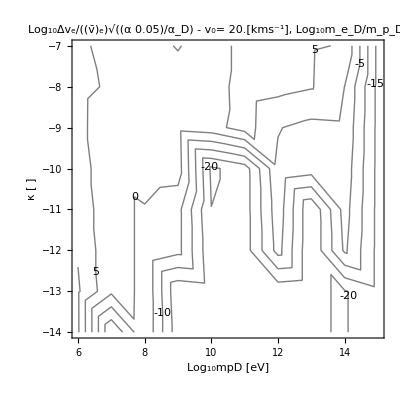

-Graphics-

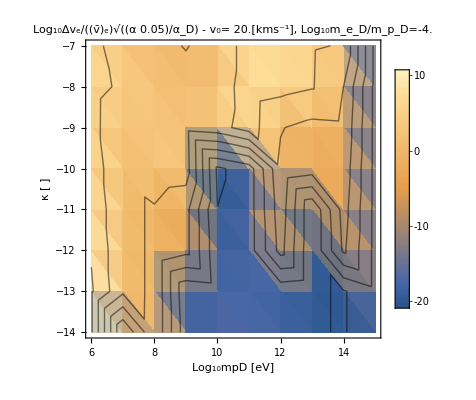

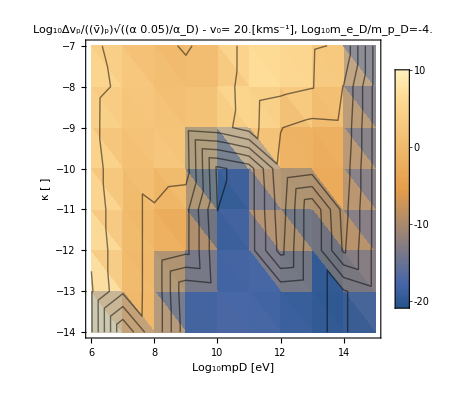

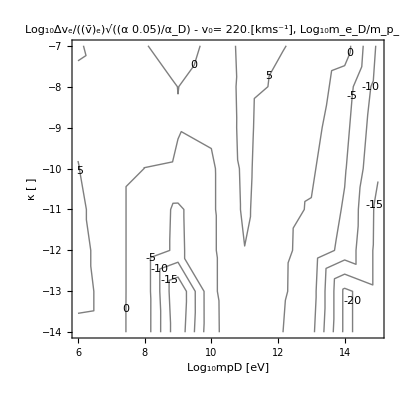

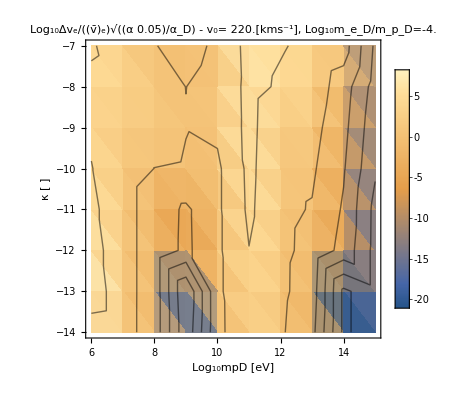

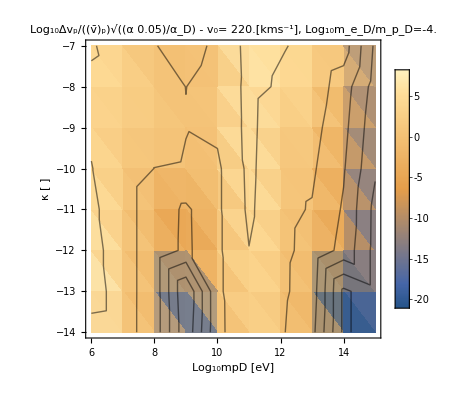

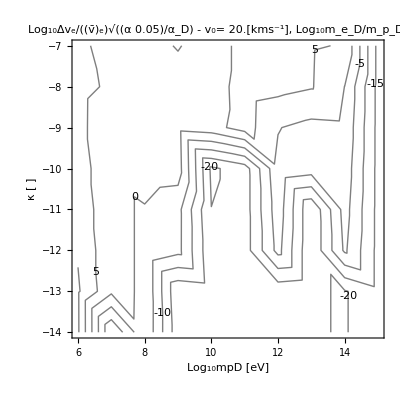

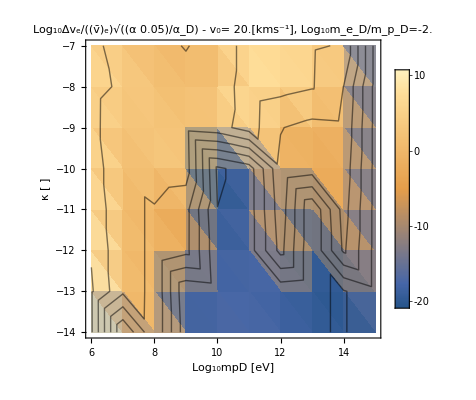

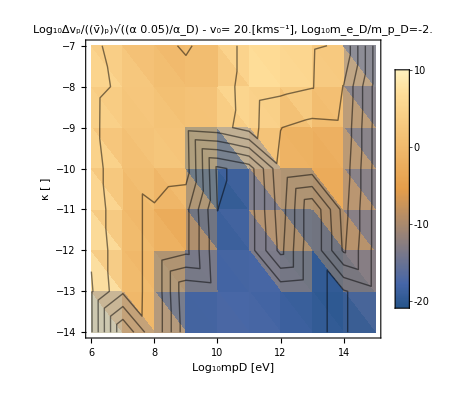

```mathematica
PlotKEchangeκContour[{PDicts1MeVKE,PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

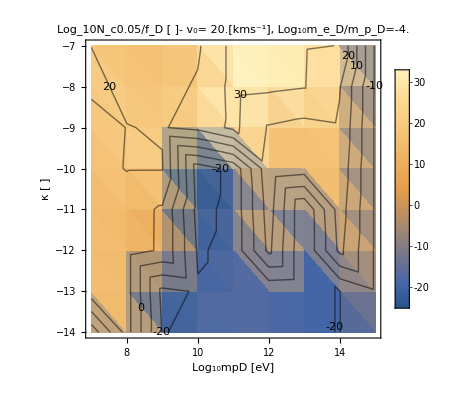

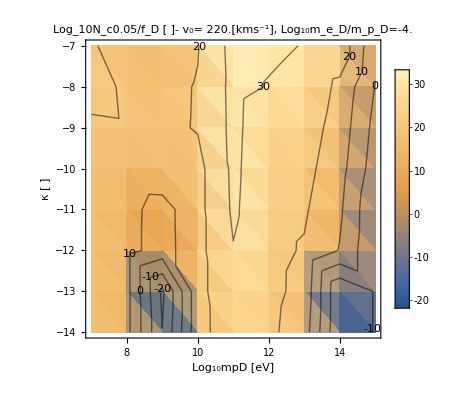

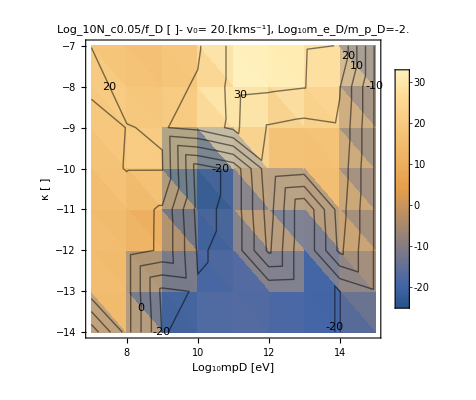

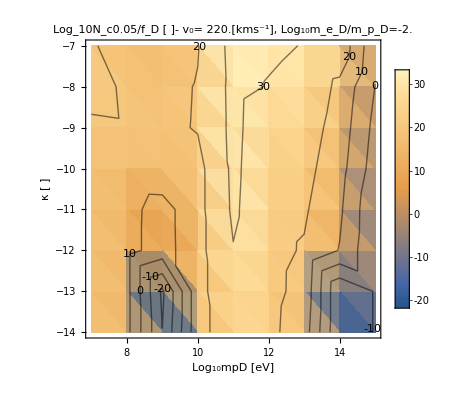

```mathematica
PlotNcκContour[{PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

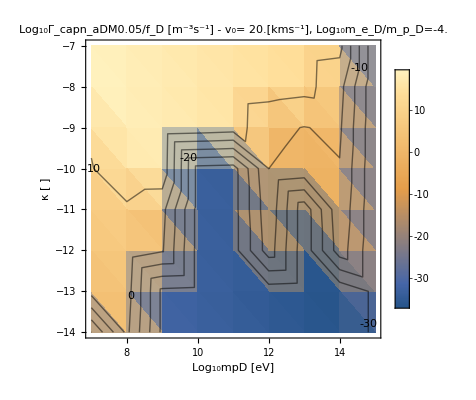

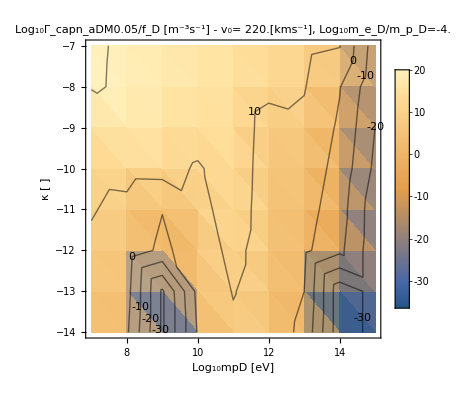

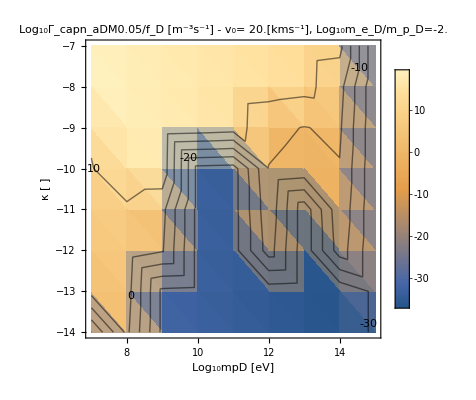

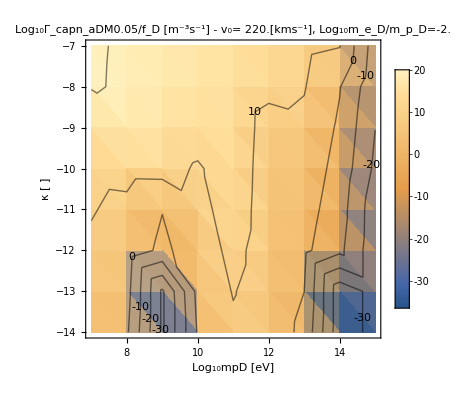

```mathematica
PlotCaptureRateκContour[{PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

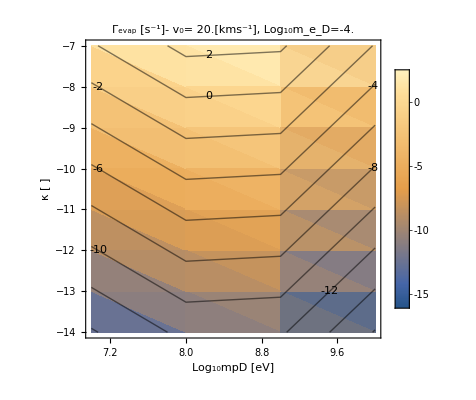

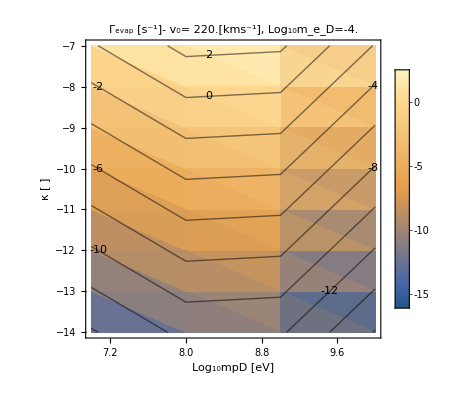

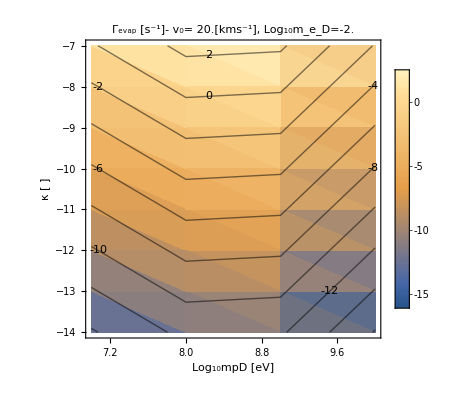

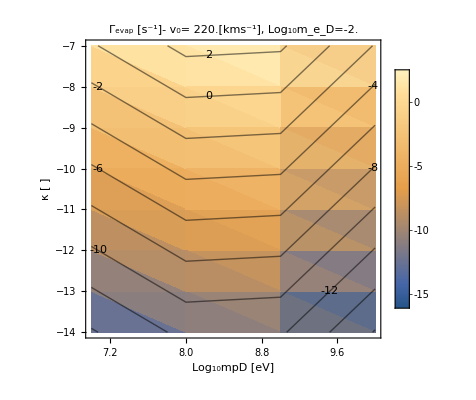

```mathematica
PlotEvaporationRateκContour[{PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

The reason this cuts off, is that Γevap =0 above 10 GeV

```mathematica
"Γtotal"/.PDicts10GeVKE
```

{7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11}

#### Energy Loss Individual masses

5

5

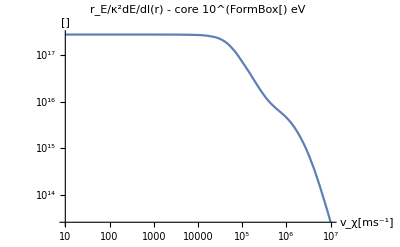

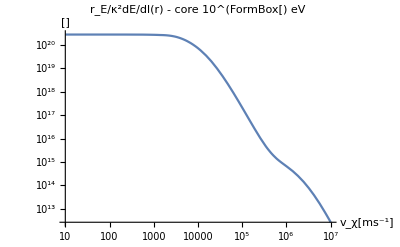

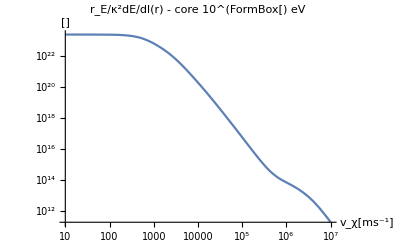

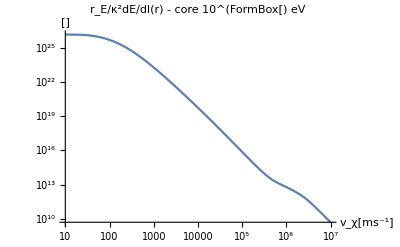

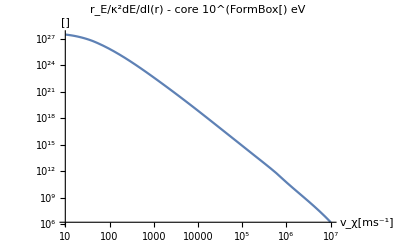

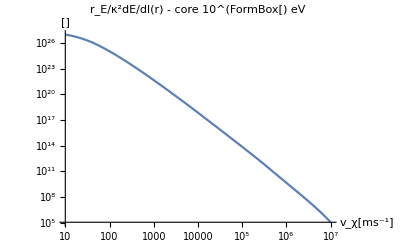

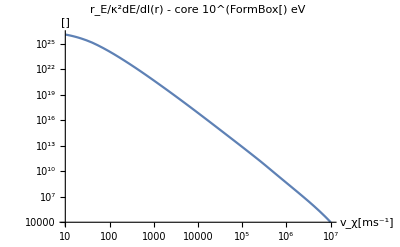

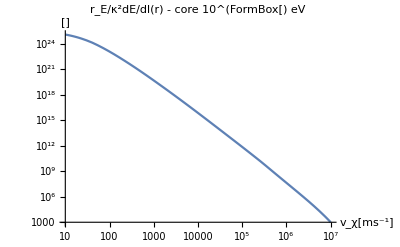

```mathematica
Do[eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Print@LogLogPlot[("rE"/.Constants`EarthRepl)("dEdlofr"/.GetTotalELFunction[ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]])[10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2),{vχ,10,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->StringForm["r_E/κ^2dE/dl(r) - core 10^(``) eV",m]]
,{m,7,15}]
```

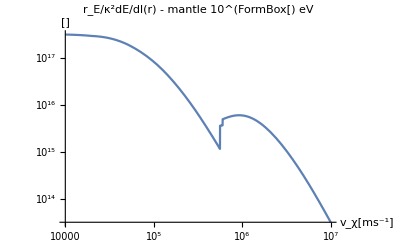

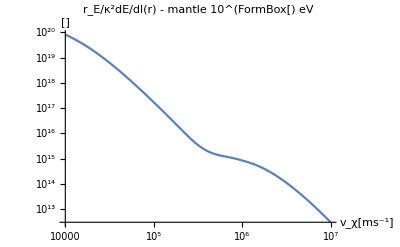

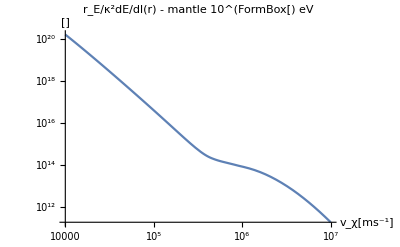

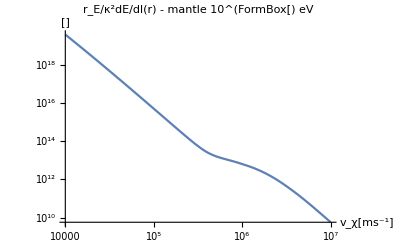

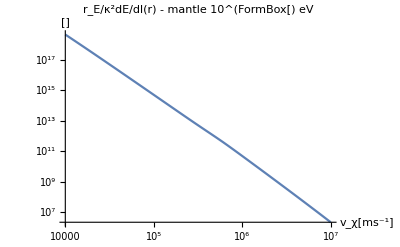

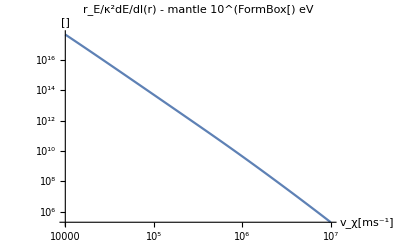

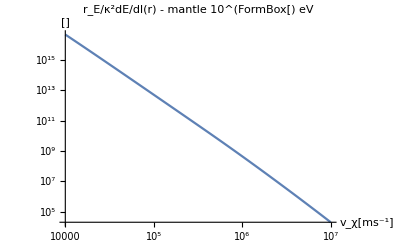

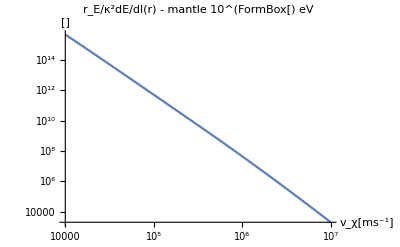

```mathematica
Do[eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Print@LogLogPlot[("rE"/.Constants`EarthRepl)("dEdlofr"/.GetTotalELFunction[ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]])[5 10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2),{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->StringForm["r_E/κ^2dE/dl(r) - mantle 10^(``) eV",m]]
,{m,7,15}]
```

#### Debug Capture Interaction Length

```mathematica
LogLogPlot[Table[eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)("dEdlofr"/.GetTotalELFunction[ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]])[10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2)
,{m,7,15}],{vχ,10,10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - core",PlotLegends->LineLegend[{Blue,Green,Red,Yellow,Orange,Dashed,Thick,Thin},Table[ToString[m],{m,7,15}]]]
```

```mathematica
"mχ"("c")^2/("JpereV")/.ElectronicσDicst10MeVto1PeV[[eind,1]]/.SIConstRepl
"materialname"/.ElectronicσDicst10MeVto1PeV[[eind,1]]
```

1.×10^15

Fe 1

```mathematica
GetWeakCaptureInteractionLength[ElectronicσDicst10MeVto1PeV[[eind,1]]][10^4]
```

{{1.10373,5.77582},{-4.,-0.0667094}}

-4

-0.0000434316

12.6978

ωcapture and ωmaxofvχ

8.43507×10^20

8.43602×10^20

InterpolatingFunction::dmval: Input value {4,-0.0000920802} lies outside the range of data in the interpolating function. Extrapolation will be used.

2.15193×10^-18

-0.0000920802

-0.0000434316

InterpolatingFunction::dmval: Input value {4,-0.0000920802} lies outside the range of data in the interpolating function. Extrapolation will be used.

2.15193×10^-18

It looks like we are extrapolating in the capture cross-section - the ω range is going out of the domain 

So we need to understand where the upper bound of ξ=10^-0.0667094 is coming from. to do this I am going to rerun the interpolation for this parameter point and try to understand why it is this particular value.

```mathematica
"vχ"/.ElectronicσDicst10MeVto1PeV[[eind,1]]//N
```

{1.10373,7.77815}

```mathematica
"ωmin"/.ElectronicσDicst10MeVto1PeV[[eind,1]]//N
```

6.04519×10^14

```mathematica
"ωmax"/.ElectronicσDicst10MeVto1PeV[[eind,1]]//N
```

ωmax

```mathematica
?ωmaxofvχ
```

```mathematica
"mχ"/.ElectronicσDicst10MeVto1PeV[[eind,1]]
```

1.78×10^-21

```mathematica
ωofξ[10^-0.06670937442614426,6.045191348120401*^14,ωmaxofvχ[vχ,1.78*^-21,ElectronicσDicst10MeVto1PeV[[eind,1]]["params"]]]/.vχ->10^5
```

7.23483×10^22

```mathematica
?ωofξ
```

We need to understand where how we get the domain for the capture cross-section. So I’ll rerun one of the interpolations

```mathematica
testpeVinterpolationFe1=Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigher[[3]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,1}];
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
("Interpoints"/.testpeVinterpolationFe1//N)[[1,;;,;;,2]];
Log10@Max[%]
```

-0.0000434316

```mathematica
Block[{m=10,n=60,vχmaxindexforσint,Truncatevχ=False,Interpointsvχandξ,Interpointsvχ,params,mχ,Interdσf,ϵ=10^-4,ωmin,coordtable},
Interpointsvχandξ=("Interpoints"/.testpeVinterpolationFe1//N)[[1]];
Interpointsvχ=("Interpointsvχ"/.testpeVinterpolationFe1//N)[[1]];
params=FeTotalparams[[1]];
mχ="mpD"/.mpDPointshigher[[3]];
Interdσf=("dσf"/.testpeVinterpolationFe1)[[1]];
ωmin= "ωedgei"/.params; (*the cutoff used in the data fitting*)
(*vχmaxindexforσint=If[Truncatevχ,Position[Interpointsvχ,_?(#<10^6&)][[-1,1]],m+1];*)
vχmaxindexforσint=m+1;

(*coordtable=Flatten[Log10@Table[Interpointsvχandξ[[i,j]],{i,vχmaxindexforσint},{j,n}],1];*)
coordtable=Flatten[Log10@Table[Interpointsvχandξ[[i,j]],{i,vχmaxindexforσint},{j,n+1}],1];
{Max[coordtable[[;;,2]]],Max[Flatten[Log10@Interpointsvχandξ,1][[;;,2]]]}
]
```

{-0.0000434316,-0.0000434316}

So it was just an indexing error, should have been {j,n+1} instead of {j,n} for the coordinate table.

```mathematica
testpeVinterpolationFe1=Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigher[[3]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,1}];
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
("σofξf"/.testpeVinterpolationFe1[[1]])[2,-1]
```

-33.8858

```mathematica
testλfuncPeVFe1=GetWeakCaptureInteractionLength[testpeVinterpolationFe1[[1]]]
```

{{1.10373,5.77582},{-4.,-0.0000434316}}

-4

-0.0000434316

12.6978

ωcapture and ωmaxofvχ

8.43507×10^20

8.43602×10^20

Indeterminate

-0.0000920802

-0.0000434316

If[#1>vχmin$5804627&&ωmaxofvχt$5804627[#1]>ωcapture$5804627[#1],(ne/.params$5804627) σofvχandωmin$5804627[#1,ωcapture$5804627[#1]],0]&

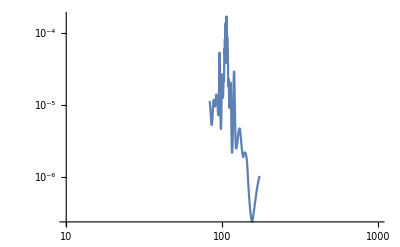

```mathematica
LogLogPlot[testλfuncPeVFe1[v],{v,10,1000}]
```

This is too small of a kinematic range, need to try lower mass  - see if more reasonable

Also need to understand why this is so janky

```mathematica
test10TeVinterpolationFe1=Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigher[[1]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,1}];
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
testλfunc10TeVFe1=GetWeakCaptureInteractionLength[test10TeVinterpolationFe1[[1]]]
```

{{2.10373,5.50838},{-4.,-0.0000434316}}

-4

-0.0000434316

126.978

ωcapture and ωmaxofvχ

8.43507×10^18

8.43602×10^18

Indeterminate

-0.0000920837

-0.0000434316

If[#1>vχmin$5798949&&ωmaxofvχt$5798949[#1]>ωcapture$5798949[#1],(ne/.params$5798949) σofvχandωmin$5798949[#1,ωcapture$5798949[#1]],0]&

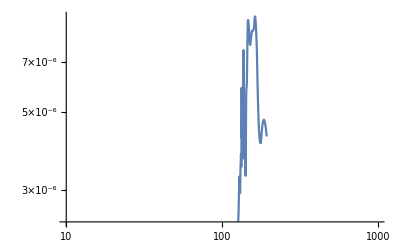

```mathematica
LogLogPlot[testλfunc10TeVFe1[v],{v,10^1,10^3}]
```

a few attempted bug fixes later

```mathematica
testλfunc10TeVFe1=GetWeakCaptureInteractionLength[test10TeVinterpolationFe1[[1]]]
LogLogPlot[testλfunc10TeVFe1[v],{v,10^1,10^3}]
```

{{2.10373,5.50838},{-4.,-0.0000434316}}

-4

-0.0000434316

126.978

ωcapture and ωmaxofvχ

8.43507×10^18

8.43602×10^18

Indeterminate

-0.0000920837

-0.0000434316

If[#1>vχmin$5810233,(ne/.params$5810233) σofvχandωmin$5810233[#1,ωcapture$5810233[#1]],0]&

-Graphics-

No change, why is the velocity range so small???

{{2.10373,5.50838},{-4.,-0.0000434316}}

-4

-0.0000434316

126.978

ωcapture and ωmaxofvχ

-2.14612×10^18

8.43602×10^18

1.74101×10^-9

-0.594159

-0.0000434316

If[#1>vχmin$5817245,(ne/.params$5817245) σofvχandωmin$5817245[#1,ωcapture$5817245[#1]],0]&

InterpolatingFunction::dmval: Input value {4.04926,-4.57842} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

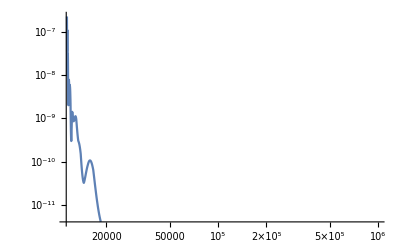

```mathematica
testλfunc10TeVFe1=GetWeakCaptureInteractionLength[test10TeVinterpolationFe1[[1]]]
LogLogPlot[testλfunc10TeVFe1[v],{v,"vesc"/.Constants`EarthRepl,10^6}]
```

Found it, I just forgot to square the escape velocity. Now it makes sense. How do we get the upper bound on velocity here?

```mathematica
testλfunc10TeVFe1[10^5.5]
```

Indeterminate

```mathematica
"σofξf"/.test10TeVinterpolationFe1[[1]]
```

InterpolatingFunction[…]

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

{{2.10373,5.50838},{-4.,-0.0000434316}}

If[#1>vχmin$6388448,(ne/.params$6388448) σofvχandωmin$6388448[#1,ωcapture$6388448[#1]],0]&

InterpolatingFunction::dmval: Input value {4.04926,-4.57842} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

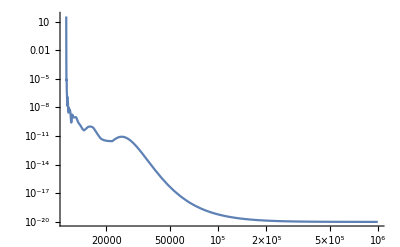

```mathematica
test10TeVinterpolationFe1=Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigher[[1]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,1}];
testλfunc10TeVFe1=GetWeakCaptureInteractionLength[test10TeVinterpolationFe1[[1]]]
LogLogPlot[testλfunc10TeVFe1[v],{v,"vesc"/.Constants`EarthRepl,10^6}]
```

```mathematica
"σofξtable"/.test10TeVinterpolationFe1//N
```

{{{{{126.978,0.0001},3.18056×10^-35},{{126.978,0.000116591},3.17374×10^-35},{{126.978,0.000135935},3.17016×10^-35},{{126.978,0.000158489},3.16186×10^-35},{{126.978,0.000184784},3.15774×10^-35},{{126.978,0.000215442},3.15522×10^-35},{{126.978,0.000251186},3.14482×10^-35},{{126.978,0.000292861},3.14015×10^-35},{{126.978,0.00034145},3.14443×10^-35},{{126.978,0.000398101},3.14106×10^-35},{{126.978,0.000464151},3.14482×10^-35},{{126.978,0.00054116},3.14875×10^-35},{{126.978,0.000630945},3.15141×10^-35},{{126.978,0.000735626},3.1702×10^-35},{{126.978,0.000857676},3.1868×10^-35},{{126.978,0.000999975},3.22098×10^-35},{{126.978,0.00116588},3.23469×10^-35},{{126.978,0.00135932},3.26014×10^-35},{{126.978,0.00158485},3.29528×10^-35},{{126.978,0.00184779},3.32509×10^-35},{{126.978,0.00215436},3.35855×10^-35},{{126.978,0.0025118},3.36307×10^-35},{{126.978,0.00292854},3.30846×10^-35},{{126.978,0.00341442},3.23945×10^-35},{{126.978,0.00398091},3.18571×10^-35},{{126.978,0.0046414},3.31349×10^-35},{{126.978,0.00541146},3.22947×10^-35},{{126.978,0.00630929},3.17341×10^-35},{{126.978,0.00735608},3.15024×10^-35},{{126.978,0.00857654},3.08569×10^-35},{{126.978,0.0099995},2.91316×10^-35},{{126.978,0.0116585},2.97633×10^-35},{{126.978,0.0135928},3.08548×10^-35},{{126.978,0.0158481},3.15905×10^-35},{{126.978,0.0184775},3.22134×10^-35},{{126.978,0.0215431},3.35146×10^-35},{{126.978,0.0251174},3.27772×10^-35},{{126.978,0.0292846},3.09036×10^-35},{{126.978,0.0341433},3.09985×10^-35},{{126.978,0.0398081},3.0879×10^-35},{{126.978,0.0464128},3.11931×10^-35},{{126.978,0.0541133},2.99081×10^-35},{{126.978,0.0630913},2.99772×10^-35},{{126.978,0.073559},2.83398×10^-35},{{126.978,0.0857633},2.87831×10^-35},{{126.978,0.0999925},2.90508×10^-35},{{126.978,0.116583},2.76204×10^-35},{{126.978,0.135925},2.72931×10^-35},{{126.978,0.158477},2.75048×10^-35},{{126.978,0.18477},2.71927×10^-35},{{126.978,0.215426},2.38131×10^-35},{{126.978,0.251167},2.33287×10^-35},{{126.978,0.292839},2.3706×10^-35},{{126.978,0.341425},2.2555×10^-35},{{126.978,0.398071},2.02455×10^-35},{{126.978,0.464116},1.51201×10^-35},{{126.978,0.541119},3.35541×10^-37},{{126.978,0.630897},1.41068×10^-36},{{126.978,0.735571},5.05843×10^-37},{{126.978,0.857612},6.83805×10^-37},{{126.978,0.9999},1.×10^-49}},{{{468.997,0.0001},3.90844×10^-32},{{468.997,0.000116591},3.89493×10^-32},{{468.997,0.000135935},3.87924×10^-32},{{468.997,0.000158489},3.86104×10^-32},{{468.997,0.000184784},3.83995×10^-32},{{468.997,0.000215442},3.81553×10^-32},{{468.997,0.000251186},3.78728×10^-32},{{468.997,0.000292861},3.75464×10^-32},{{468.997,0.00034145},3.717×10^-32},{{468.997,0.000398101},3.67364×10^-32},{{468.997,0.000464151},3.62384×10^-32},{{468.997,0.00054116},3.56676×10^-32},{{468.997,0.000630945},3.50149×10^-32},{{468.997,0.000735626},3.42711×10^-32},{{468.997,0.000857676},3.34268×10^-32},{{468.997,0.000999975},3.24723×10^-32},{{468.997,0.00116588},3.1399×10^-32},{{468.997,0.00135932},3.01986×10^-32},{{468.997,0.00158485},2.88652×10^-32},{{468.997,0.00184779},2.73953×10^-32},{{468.997,0.00215436},2.57887×10^-32},{{468.997,0.0025118},2.40515×10^-32},{{468.997,0.00292854},2.21939×10^-32},{{468.997,0.00341442},2.02324×10^-32},{{468.997,0.00398091},1.81939×10^-32},{{468.997,0.0046414},1.61116×10^-32},{{468.997,0.00541146},1.40248×10^-32},{{468.997,0.00630929},1.19759×10^-32},{{468.997,0.00735608},1.00121×10^-32},{{468.997,0.00857654},8.18068×10^-33},{{468.997,0.0099995},6.52142×10^-33},{{468.997,0.0116585},5.06752×10^-33},{{468.997,0.0135928},3.84062×10^-33},{{468.997,0.0158481},2.84459×10^-33},{{468.997,0.0184775},2.06326×10^-33},{{468.997,0.0215431},1.47497×10^-33},{{468.997,0.0251174},1.05911×10^-33},{{468.997,0.0292846},7.73805×10^-34},{{468.997,0.0341433},5.83356×10^-34},{{468.997,0.0398081},4.47873×10^-34},{{468.997,0.0464128},3.85349×10^-34},{{468.997,0.0541133},3.46681×10^-34},{{468.997,0.0630913},3.04342×10^-34},{{468.997,0.073559},3.94483×10^-34},{{468.997,0.0857633},4.18607×10^-34},{{468.997,0.0999925},2.83747×10^-34},{{468.997,0.116583},2.74877×10^-34},{{468.997,0.135925},1.91629×10^-34},{{468.997,0.158477},2.2808×10^-34},{{468.997,0.18477},2.13669×10^-34},{{468.997,0.215426},2.76722×10^-34},{{468.997,0.251167},1.98211×10^-34},{{468.997,0.292839},1.65972×10^-34},{{468.997,0.341425},1.59805×10^-34},{{468.997,0.398071},1.25834×10^-34},{{468.997,0.464116},1.04258×10^-34},{{468.997,0.541119},7.16632×10^-35},{{468.997,0.630897},4.29908×10^-35},{{468.997,0.735571},2.11883×10^-35},{{468.997,0.857612},3.30116×10^-36},{{468.997,0.9999},1.×10^-49}},{{{1732.26,0.0001},1.35438×10^-29},{{1732.26,0.000116591},1.3033×10^-29},{{1732.26,0.000135935},1.24666×10^-29},{{1732.26,0.000158489},1.18436×10^-29},{{1732.26,0.000184784},1.11643×10^-29},{{1732.26,0.000215442},1.04313×10^-29},{{1732.26,0.000251186},9.64945×10^-30},{{1732.26,0.000292861},8.82671×10^-30},{{1732.26,0.00034145},7.97399×10^-30},{{1732.26,0.000398101},7.10498×10^-30},{{1732.26,0.000464151},6.23617×10^-30},{{1732.26,0.00054116},5.38586×10^-30},{{1732.26,0.000630945},4.57309×10^-30},{{1732.26,0.000735626},3.81616×10^-30},{{1732.26,0.000857676},3.13091×10^-30},{{1732.26,0.000999975},2.52942×10^-30},{{1732.26,0.00116588},2.01863×10^-30},{{1732.26,0.00135932},1.59984×10^-30},{{1732.26,0.00158485},1.26902×10^-30},{{1732.26,0.00184779},1.01762×10^-30},{{1732.26,0.00215436},8.34044×10^-31},{{1732.26,0.0025118},7.05356×10^-31},{{1732.26,0.00292854},6.18777×10^-31},{{1732.26,0.00341442},5.62867×10^-31},{{1732.26,0.00398091},5.26296×10^-31},{{1732.26,0.0046414},5.10855×10^-31},{{1732.26,0.00541146},4.00559×10^-31},{{1732.26,0.00630929},1.76605×10^-31},{{1732.26,0.00735608},7.94821×10^-32},{{1732.26,0.00857654},3.47259×10^-32},{{1732.26,0.0099995},1.47735×10^-32},{{1732.26,0.0116585},6.12609×10^-33},{{1732.26,0.0135928},2.50404×10^-33},{{1732.26,0.0158481},1.06586×10^-33},{{1732.26,0.0184775},4.64246×10^-34},{{1732.26,0.0215431},5.8406×10^-34},{{1732.26,0.0251174},3.00312×10^-34},{{1732.26,0.0292846},1.77268×10^-34},{{1732.26,0.0341433},8.73067×10^-35},{{1732.26,0.0398081},3.25824×10^-35},{{1732.26,0.0464128},2.2788×10^-36},{{1732.26,0.0541133},2.39021×10^-35},{{1732.26,0.0630913},6.784×10^-35},{{1732.26,0.073559},3.8084×10^-35},{{1732.26,0.0857633},1.68202×10^-35},{{1732.26,0.0999925},1.98574×10^-35},{{1732.26,0.116583},1.64969×10^-35},{{1732.26,0.135925},1.30558×10^-35},{{1732.26,0.158477},7.00257×10^-36},{{1732.26,0.18477},3.22594×10^-36},{{1732.26,0.215426},8.57281×10^-37},{{1732.26,0.251167},1.10768×10^-36},{{1732.26,0.292839},6.72732×10^-37},{{1732.26,0.341425},9.21431×10^-37},{{1732.26,0.398071},9.56954×10^-37},{{1732.26,0.464116},8.9068×10^-37},{{1732.26,0.541119},4.29172×10^-38},{{1732.26,0.630897},2.70804×10^-37},{{1732.26,0.735571},1.39689×10^-37},{{1732.26,0.857612},4.82392×10^-38},{{1732.26,0.9999},1.×10^-49}},{{{6398.15,0.0001},2.89994×10^-27},{{6398.15,0.000116591},2.03436×10^-27},{{6398.15,0.000135935},1.37971×10^-27},{{6398.15,0.000158489},9.03912×10^-28},{{6398.15,0.000184784},5.71818×10^-28},{{6398.15,0.000215442},3.49287×10^-28},{{6398.15,0.000251186},2.06102×10^-28},{{6398.15,0.000292861},1.17579×10^-28},{{6398.15,0.00034145},6.49382×10^-29},{{6398.15,0.000398101},3.47851×10^-29},{{6398.15,0.000464151},1.81174×10^-29},{{6398.15,0.00054116},9.21019×10^-30},{{6398.15,0.000630945},4.59672×10^-30},{{6398.15,0.000735626},2.27587×10^-30},{{6398.15,0.000857676},1.13918×10^-30},{{6398.15,0.000999975},5.95878×10^-31},{{6398.15,0.00116588},3.41854×10^-31},{{6398.15,0.00135932},2.25423×10^-31},{{6398.15,0.00158485},1.72997×10^-31},{{6398.15,0.00184779},1.49764×10^-31},{{6398.15,0.00215436},1.39802×10^-31},{{6398.15,0.0025118},1.35864×10^-31},{{6398.15,0.00292854},1.03004×10^-31},{{6398.15,0.00341442},3.419×10^-32},{{6398.15,0.00398091},1.15127×10^-32},{{6398.15,0.0046414},4.19556×10^-33},{{6398.15,0.00541146},1.32277×10^-33},{{6398.15,0.00630929},4.61072×10^-33},{{6398.15,0.00735608},1.07736×10^-33},{{6398.15,0.00857654},5.5508×10^-34},{{6398.15,0.0099995},8.52222×10^-35},{{6398.15,0.0116585},8.9252×10^-35},{{6398.15,0.0135928},4.72769×10^-35},{{6398.15,0.0158481},2.72512×10^-35},{{6398.15,0.0184775},5.09045×10^-35},{{6398.15,0.0215431},2.06595×10^-35},{{6398.15,0.0251174},5.46301×10^-36},{{6398.15,0.0292846},2.05155×10^-35},{{6398.15,0.0341433},2.97042×10^-36},{{6398.15,0.0398081},1.50629×10^-36},{{6398.15,0.0464128},2.84629×10^-36},{{6398.15,0.0541133},1.42136×10^-36},{{6398.15,0.0630913},3.27855×10^-37},{{6398.15,0.073559},9.13691×10^-37},{{6398.15,0.0857633},2.07583×10^-37},{{6398.15,0.0999925},1.93821×10^-37},{{6398.15,0.116583},1.15944×10^-37},{{6398.15,0.135925},7.78011×10^-39},{{6398.15,0.158477},2.01934×10^-37},{{6398.15,0.18477},5.95015×10^-38},{{6398.15,0.215426},3.8896×10^-38},{{6398.15,0.251167},6.21614×10^-38},{{6398.15,0.292839},6.08139×10^-39},{{6398.15,0.341425},9.75176×10^-39},{{6398.15,0.398071},1.24908×10^-38},{{6398.15,0.464116},1.12116×10^-38},{{6398.15,0.541119},1.55436×10^-38},{{6398.15,0.630897},1.5241×10^-38},{{6398.15,0.735571},1.68507×10^-39},{{6398.15,0.857612},1.96975×10^-40},{{6398.15,0.9999},1.×10^-49}},{{{23631.8,0.0001},2.35982×10^-28},{{23631.8,0.000116591},1.0333×10^-28},{{23631.8,0.000135935},4.47218×10^-29},{{23631.8,0.000158489},1.91661×10^-29},{{23631.8,0.000184784},8.15222×10^-30},{{23631.8,0.000215442},3.45438×10^-30},{{23631.8,0.000251186},1.46866×10^-30},{{23631.8,0.000292861},6.36007×10^-31},{{23631.8,0.00034145},2.89309×10^-31},{{23631.8,0.000398101},1.45832×10^-31},{{23631.8,0.000464151},1.06769×10^-31},{{23631.8,0.00054116},6.21549×10^-32},{{23631.8,0.000630945},2.4636×10^-32},{{23631.8,0.000735626},1.06868×10^-32},{{23631.8,0.000857676},6.03624×10^-32},{{23631.8,0.000999975},2.09228×10^-32},{{23631.8,0.00116588},5.98896×10^-32},{{23631.8,0.00135932},1.76433×10^-32},{{23631.8,0.00158485},5.3837×10^-33},{{23631.8,0.00184779},3.84913×10^-32},{{23631.8,0.00215436},1.22301×10^-32},{{23631.8,0.0025118},3.51839×10^-33},{{23631.8,0.00292854},4.84605×10^-34},{{23631.8,0.00341442},6.7731×10^-34},{{23631.8,0.00398091},2.044×10^-34},{{23631.8,0.0046414},3.65757×10^-35},{{23631.8,0.00541146},4.15646×10^-36},{{23631.8,0.00630929},7.98712×10^-35},{{23631.8,0.00735608},7.19821×10^-36},{{23631.8,0.00857654},1.83392×10^-36},{{23631.8,0.0099995},4.88473×10^-35},{{23631.8,0.0116585},1.62448×10^-35},{{23631.8,0.0135928},7.02552×10^-36},{{23631.8,0.0158481},5.71314×10^-37},{{23631.8,0.0184775},7.56135×10^-38},{{23631.8,0.0215431},6.56441×10^-38},{{23631.8,0.0251174},1.57569×10^-38},{{23631.8,0.0292846},3.23384×10^-38},{{23631.8,0.0341433},9.25344×10^-39},{{23631.8,0.0398081},4.60009×10^-39},{{23631.8,0.0464128},1.58322×10^-38},{{23631.8,0.0541133},2.01904×10^-39},{{23631.8,0.0630913},2.04735×10^-39},{{23631.8,0.073559},6.84769×10^-39},{{23631.8,0.0857633},1.00702×10^-38},{{23631.8,0.0999925},1.19771×10^-38},{{23631.8,0.116583},3.56362×10^-39},{{23631.8,0.135925},1.4047×10^-39},{{23631.8,0.158477},1.64814×10^-39},{{23631.8,0.18477},1.83814×10^-39},{{23631.8,0.215426},1.92984×10^-39},{{23631.8,0.251167},1.1332×10^-39},{{23631.8,0.292839},1.46483×10^-39},{{23631.8,0.341425},2.06396×10^-40},{{23631.8,0.398071},6.05733×10^-41},{{23631.8,0.464116},2.43202×10^-40},{{23631.8,0.541119},2.05555×10^-40},{{23631.8,0.630897},1.71133×10^-41},{{23631.8,0.735571},2.27865×10^-41},{{23631.8,0.857612},3.10954×10^-41},{{23631.8,0.9999},1.×10^-49}},{{{87285.,0.0001},2.14761×10^-31},{{87285.,0.000116591},1.10924×10^-30},{{87285.,0.000135935},3.81689×10^-31},{{87285.,0.000158489},1.31222×10^-31},{{87285.,0.000184784},4.50955×10^-32},{{87285.,0.000215442},4.06083×10^-31},{{87285.,0.000251186},1.3927×10^-31},{{87285.,0.000292861},4.77187×10^-32},{{87285.,0.00034145},1.63457×10^-32},{{87285.,0.000398101},1.35522×10^-31},{{87285.,0.000464151},1.04826×10^-30},{{87285.,0.00054116},3.04311×10^-31},{{87285.,0.000630945},9.34506×10^-32},{{87285.,0.000735626},2.52799×10^-32},{{87285.,0.000857676},7.06197×10^-33},{{87285.,0.000999975},3.40654×10^-33},{{87285.,0.00116588},1.01611×10^-33},{{87285.,0.00135932},1.08209×10^-34},{{87285.,0.00158485},1.14614×10^-34},{{87285.,0.00184779},2.77394×10^-34},{{87285.,0.00215436},1.59921×10^-34},{{87285.,0.0025118},1.12691×10^-34},{{87285.,0.00292854},1.22779×10^-35},{{87285.,0.00341442},6.72188×10^-36},{{87285.,0.00398091},8.57215×10^-37},{{87285.,0.0046414},2.51716×10^-37},{{87285.,0.00541146},3.81161×10^-38},{{87285.,0.00630929},3.68596×10^-39},{{87285.,0.00735608},8.35226×10^-39},{{87285.,0.00857654},1.02295×10^-38},{{87285.,0.0099995},1.01696×10^-39},{{87285.,0.0116585},3.79214×10^-40},{{87285.,0.0135928},1.16165×10^-39},{{87285.,0.0158481},2.59534×10^-39},{{87285.,0.0184775},1.32796×10^-39},{{87285.,0.0215431},1.45862×10^-39},{{87285.,0.0251174},1.10379×10^-39},{{87285.,0.0292846},3.12886×10^-40},{{87285.,0.0341433},1.76938×10^-40},{{87285.,0.0398081},2.03162×10^-40},{{87285.,0.0464128},3.24681×10^-40},{{87285.,0.0541133},3.38649×10^-40},{{87285.,0.0630913},4.08472×10^-40},{{87285.,0.073559},4.78889×10^-40},{{87285.,0.0857633},1.97815×10^-40},{{87285.,0.0999925},1.13225×10^-40},{{87285.,0.116583},1.02484×10^-40},{{87285.,0.135925},1.07017×10^-40},{{87285.,0.158477},1.9617×10^-40},{{87285.,0.18477},1.52663×10^-40},{{87285.,0.215426},2.60187×10^-41},{{87285.,0.251167},3.93847×10^-42},{{87285.,0.292839},3.54602×10^-41},{{87285.,0.341425},3.25876×10^-43},{{87285.,0.398071},6.57153×10^-42},{{87285.,0.464116},5.49535×10^-42},{{87285.,0.541119},7.58778×10^-42},{{87285.,0.630897},6.85363×10^-42},{{87285.,0.735571},1.823×10^-42},{{87285.,0.857612},1.92583×10^-43},{{87285.,0.9999},1.×10^-49}},{{{322390.,0.0001},3.53807×10^-32},{{322390.,0.000116591},1.20846×10^-32},{{322390.,0.000135935},4.14321×10^-33},{{322390.,0.000158489},2.26169×10^-30},{{322390.,0.000184784},6.65003×10^-31},{{322390.,0.000215442},1.88368×10^-31},{{322390.,0.000251186},5.83403×10^-32},{{322390.,0.000292861},1.37817×10^-32},{{322390.,0.00034145},4.31046×10^-33},{{322390.,0.000398101},2.19046×10^-33},{{322390.,0.000464151},1.67954×10^-35},{{322390.,0.00054116},4.96389×10^-34},{{322390.,0.000630945},1.9703×10^-34},{{322390.,0.000735626},3.47108×10^-35},{{322390.,0.000857676},3.87209×10^-34},{{322390.,0.000999975},1.91422×10^-34},{{322390.,0.00116588},3.89092×10^-37},{{322390.,0.00135932},2.53648×10^-37},{{322390.,0.00158485},2.76757×10^-38},{{322390.,0.00184779},3.94637×10^-38},{{322390.,0.00215436},1.97065×10^-38},{{322390.,0.0025118},1.87703×10^-38},{{322390.,0.00292854},5.7401×10^-39},{{322390.,0.00341442},1.60073×10^-39},{{322390.,0.00398091},1.38985×10^-39},{{322390.,0.0046414},3.68737×10^-39},{{322390.,0.00541146},7.93356×10^-40},{{322390.,0.00630929},1.26448×10^-39},{{322390.,0.00735608},1.23649×10^-40},{{322390.,0.00857654},3.10408×10^-40},{{322390.,0.0099995},6.40136×10^-41},{{322390.,0.0116585},6.07465×10^-41},{{322390.,0.0135928},1.48765×10^-40},{{322390.,0.0158481},7.88905×10^-41},{{322390.,0.0184775},5.32812×10^-41},{{322390.,0.0215431},4.84962×10^-42},{{322390.,0.0251174},1.75967×10^-41},{{322390.,0.0292846},3.82647×10^-42},{{322390.,0.0341433},8.34625×10^-43},{{322390.,0.0398081},3.62031×10^-42},{{322390.,0.0464128},5.71221×10^-42},{{322390.,0.0541133},1.87552×10^-42},{{322390.,0.0630913},7.4311×10^-43},{{322390.,0.073559},2.77237×10^-42},{{322390.,0.0857633},1.39432×10^-42},{{322390.,0.0999925},1.32873×10^-44},{{322390.,0.116583},1.67655×10^-42},{{322390.,0.135925},2.32248×10^-42},{{322390.,0.158477},1.25957×10^-42},{{322390.,0.18477},6.01263×10^-43},{{322390.,0.215426},2.6707×10^-43},{{322390.,0.251167},3.67672×10^-44},{{322390.,0.292839},4.41392×10^-44},{{322390.,0.341425},4.51634×10^-44},{{322390.,0.398071},2.69765×10^-44},{{322390.,0.464116},1.59746×10^-44},{{322390.,0.541119},9.66762×10^-45},{{322390.,0.630897},3.40278×10^-45},{{322390.,0.735571},6.67268×10^-46},{{322390.,0.857612},1.16548×10^-46},{{322390.,0.9999},1.×10^-49}}}}

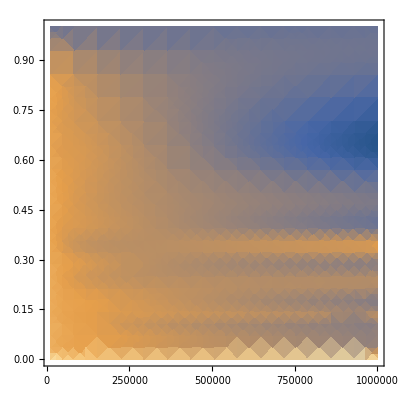

```mathematica
DensityPlot[("σofξf"/.test10TeVinterpolationFe1[[1]])[Log10@v,Log10@ξ],{v,"vesc"/.Constants`EarthRepl,10^6},{ξ,10^-4,1-10^-4},PlotRange->All]
```

Order 3 interpolation with the a small padding of 10^-49 in the table of values, it was giving indeterminates (from a 0) at the last energy transfer value, this is what was causing the restricted range of the interpolation function. Try again with interpolation order 4

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

{{2.10373,5.50838},{-4.,-0.0000434316}}

If[#1>vχmin$6507814,(ne/.params$6507814) σofvχandωmin$6507814[#1,ωcapture$6507814[#1]],0]&

InterpolatingFunction::dmval: Input value {4.04926,-4.57842} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

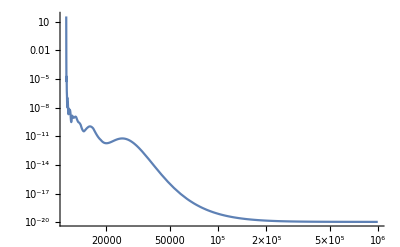

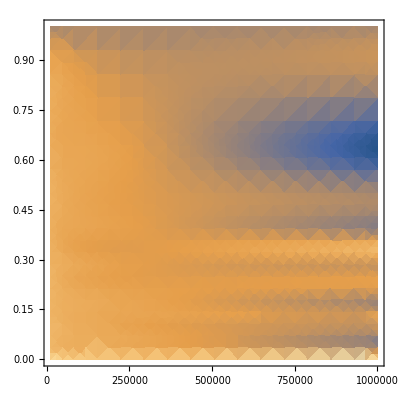

```mathematica
test10TeVinterpolationFe1=Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigher[[1]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,1}];
testλfunc10TeVFe1=GetWeakCaptureInteractionLength[test10TeVinterpolationFe1[[1]]]
LogLogPlot[testλfunc10TeVFe1[v],{v,"vesc"/.Constants`EarthRepl,10^6}]
DensityPlot[("σofξf"/.test10TeVinterpolationFe1[[1]])[Log10@v,Log10@ξ],{v,"vesc"/.Constants`EarthRepl,10^6},{ξ,10^-4,1-10^-4},PlotRange->All]
```

#### Debug Capture Interaction Length Nuclear

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicst10MeVto1PeV[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[2]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-3,10^5-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Mantle Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{0,10^24}]
```

InterpolatingFunction::dmval: Input value {4.04922,-4.77713} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04922,-7.33316} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04922,-4.47791} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^10 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
GetWeakCaptureInteractionLengthNuc[NuclearσDicst10MeVto1PeV[[Nucind]][[1]]][1.13 10^4]
```

{{0.049218,7.77815},{-4.,-0.0000434316}}

-4

-0.0000434316

0.

ωcapture and ωmaxofvχ

1.8981×10^14

5.81172×10^15

3.07438×10^-16 ne

-1.48732

-0.0000434316

3.07438×10^-16 ne

It seems like ωcapture is always greater than ωmax, but this shouldn’t be, let’s solve to find the condition such that ωmax > ωcapture

```mathematica
ωcapturet=1/(2 ℏ)mχ (vχ^2 - vesc^2)
ωmaxt = (2 vχ^2)/(ℏ) (mχ^2 mN)/(mχ + mN)^2
vχbsol=Solve[ωcapturet == ωmaxt,vχ][[2]]
```

(mχ (-vesc^2+vχ^2))/(2 ℏ)

(2 mN mχ^2 vχ^2)/((mN+mχ)^2 ℏ)

{vχ→vesc/(√(1-(4 mN mχ)/(mN+mχ)^2))}

```mathematica
ωcapturet-ωmax/.vχ->(ϵ vχ/.vχbsol)//Simplify
```

(mχ vesc^2 (-1+ϵ^2))/(2 ℏ)

okay so for vχ < vχbsol we have ωcapture < ωmax and we can capture from a single hard scatter, so what is vχbsol for various values of mχ?

```mathematica
"vesc"/.EarthRepl
```

11200

```mathematica
vχbsol//FullSimplify
%/.mN->10^10/.mχ->1.1 10^10
```

{vχ→vesc/(√(1-(4 mN mχ)/(mN+mχ)^2))}

{vχ→21. vesc}

For slides

```mathematica
Subscript[v, esc]<Subscript[v, χ]<Subscript[v, esc]/(√(1-(4 Subscript[m, N] Subscript[m, χ])/(Subscript[m, N]+Subscript[m, χ])^2))
```

v_esc<v_χ<v_esc/(√(1-(4 m_N m_χ)/(m_N+m_χ)^2))

#### Fix Nc evap and capture rates

```mathematica
Dimensions@PDicts100GeVScan
```

{4,8}

```mathematica
PDicts100GeVScan[[1,1]];
KeyDrop[%,{"Γtotal","dNcMaxdt","NcMax","timeenoughforequil","Nc"}]
```

<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→73429.,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→778994.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→778994.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→778994.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→778994.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→778994.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→778994.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→778994.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→778994.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→73766.,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→73766.,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→73766.,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→73766.,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→73766.,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→73766.,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→73766.,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→73766.,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→782837.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→782837.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→782837.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→782837.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→782837.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→782837.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→782837.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→782837.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…]|>}}

```mathematica
Dimensions@droppedPDicts100GeVScan
```

{4,8}

6

{1.78×10^-25,1.78×10^-25,1.78×10^-25,1.78×10^-25}

```mathematica
SymbolName[Unevaluated@PDicts100GeVKE]
"PDicts100GeVKE"
```

PDicts100GeVKE

PDicts100GeVKE

pdicts

```mathematica
vartostring[var_]:=SymbolName[Unevaluated@var]
```

```mathematica
masses=Table[m,{m,6,15}];
pdicts={PDicts1MeVScan,PDicts10MeVScan,PDictsp1GeVScan,PDicts1GeVScan,PDicts10GeVScan,PDicts100GeVScan,PDicts1TeVScan,PDicts10TeVScan,PDicts100TeVScan,PDicts1PeVScan};

(*filenames=Table[vartostring[pdicts[[p]]],{p,Length@pdicts}]*)
filenames = {"PDicts1MeVScan","PDicts10MeVScan","PDictsp1GeVScan","PDicts1GeVScan","PDicts10GeVScan","PDicts100GeVScan","PDicts1TeVScan","PDicts10TeVScan","PDicts100TeVScan","PDicts1PeVScan"};
Monitor[
Do[
Print[masses[[p]]];
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^masses[[p]] ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
droppedPDicts=Table[Table[KeyDrop[pdicts[[p]][[i,j]],{"Γtotal","dNcMaxdt","NcMax","timeenoughforequil","Nc"}],{j,Dimensions[pdicts[[p]]][[2]]}],{i,Dimensions[pdicts[[p]]][[1]]}];
(*Print[droppedPDicts];*)

Scandicts={};
Do[
NcMaxdict =GetNcMax[droppedPDicts[[d]]];
Ncdict=GetNc[NcMaxdict,NuclearσDicst10MeVto1PeV[[Nucind]]];
AppendTo[Scandicts,Ncdict];
,{d,Length[droppedPDicts]}];

SaveIt[NotebookDirectory[]<>filenames[[p]],Scandicts]

,{p,Length[masses]}]
,p]
```

6

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in vχ near {vχ,bE} = {42392.6,2.81109×10^6}. NIntegrate obtained 1.63623×10^15 and 2.66918×10^12 for the integral and error estimates.

I made it to dNcMaxdt

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in vχ near {vχ,bE} = {42392.6,2.81109×10^6}. NIntegrate obtained 1.54875×10^17 and 2.53341×10^14 for the integral and error estimates.

I made it to dNcMaxdt

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in vχ near {vχ,bE} = {42392.6,2.81109×10^6}. NIntegrate obtained 2.42294×10^19 and 2.93234×10^16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

I made it to dNcMaxdt

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

7

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

8

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

9

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

10

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

11

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

12

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

I made it to evaporation rate

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

I made it to evaporation rate

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

I made it to evaporation rate

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

13

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

14

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

15

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

I made it to dNcMaxdt

I made it to dNcMaxdt

I made it to dNcMaxdt

«5 more identical outputs»

I made it to evaporation rate

I made it to evaporation rate

I made it to evaporation rate

«1 more identical outputs»

#### Get KE change - prefix

```mathematica
"mpD"("c")^2/("JpereV")/.PDicts1MeVScan/.SIConstRepl
```

{{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6}}

```mathematica
"mpD"("c")^2/("JpereV")/.PDicts1MeVKE/.SIConstRepl
```

{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6}

```mathematica
PDictsp1GeVKE
```

{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→277.577 nD,NcMax→3.87873×10^19 nD,timeenoughforequil→True,Nc→8.18632×10^13 nD,Γtotal→3.39074×10^16,pDvescchange→4771.57,eDvescchange→477157.,ΔpKE/vpbar→0.264492,ΔeKE/vpbar→0.337373,Ntot→5.58813×10^13,nD→0.682619,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→31934. nD,NcMax→4.46231×10^21 nD,timeenoughforequil→True,Nc→9.41801×10^13 nD,Γtotal→3.39074×10^16,pDvescchange→5117.95,eDvescchange→511795.,ΔpKE/vpbar→0.283692,ΔeKE/vpbar→0.361865,Ntot→6.42891×10^13,nD→0.682619,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.1911×10^6 nD,NcMax→4.45909×10^23 nD,timeenoughforequil→True,Nc→9.41121×10^13 nD,Γtotal→3.39074×10^16,pDvescchange→5116.11,eDvescchange→511611.,ΔpKE/vpbar→0.28359,ΔeKE/vpbar→0.361734,Ntot→6.42427×10^13,nD→0.682619,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.19053×10^8 nD,NcMax→4.4583×10^25 nD,timeenoughforequil→True,Nc→9.40954×10^13 nD,Γtotal→3.39074×10^16,pDvescchange→5115.65,eDvescchange→511565.,ΔpKE/vpbar→0.283565,ΔeKE/vpbar→0.361702,Ntot→6.42313×10^13,nD→0.682619,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.59255×10^17 nD,NcMax→2.22536×10^34 nD,timeenoughforequil→True,Nc→4.69677×10^20 nD,Γtotal→3.39074×10^16,pDvescchange→1.14292×10^7,eDvescchange→1.14292×10^9,ΔpKE/vpbar→633.531,ΔeKE/vpbar→808.102,Ntot→3.20611×10^20,nD→0.682619,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→2.2819×10^20 nD,Γtotal→3.39074×10^16,pDvescchange→7.96646×10^6,eDvescchange→7.96646×10^8,ΔpKE/vpbar→441.587,ΔeKE/vpbar→563.268,Ntot→1.55767×10^20,nD→0.682619,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→2.2819×10^18 nD,Γtotal→3.39074×10^16,pDvescchange→796646.,eDvescchange→7.96646×10^7,ΔpKE/vpbar→44.1587,ΔeKE/vpbar→56.3268,Ntot→1.55767×10^18,nD→0.682619,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→73429.,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73733×10^18 nD,NcMax→1.08118×10^36 nD,timeenoughforequil→True,Nc→2.2819×10^16 nD,Γtotal→3.39074×10^16,pDvescchange→79664.6,eDvescchange→7.96646×10^6,ΔpKE/vpbar→4.41587,ΔeKE/vpbar→5.63268,Ntot→1.55767×10^16,nD→0.682619,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→46.227 nD,NcMax→6.45955×10^18 nD,timeenoughforequil→True,Nc→1.36333×10^13 nD,Γtotal→3.39074×10^16,pDvescchange→1947.23,eDvescchange→194723.,ΔpKE/vpbar→0.0124843,ΔeKE/vpbar→0.0125167,Ntot→9.30636×10^12,nD→0.682619,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5171.12 nD,NcMax→7.22589×10^20 nD,timeenoughforequil→True,Nc→1.52507×10^13 nD,Γtotal→3.39074×10^16,pDvescchange→2059.5,eDvescchange→205950.,ΔpKE/vpbar→0.0132041,ΔeKE/vpbar→0.0132383,Ntot→1.04104×10^13,nD→0.682619,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→520997. nD,NcMax→7.28017×10^22 nD,timeenoughforequil→True,Nc→1.53653×10^13 nD,Γtotal→3.39074×10^16,pDvescchange→2067.22,eDvescchange→206722.,ΔpKE/vpbar→0.0132536,ΔeKE/vpbar→0.0132879,Ntot→1.04886×10^13,nD→0.682619,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.21235×10^7 nD,NcMax→7.28349×10^24 nD,timeenoughforequil→True,Nc→1.53723×10^13 nD,Γtotal→3.39074×10^16,pDvescchange→2067.69,eDvescchange→206769.,ΔpKE/vpbar→0.0132567,ΔeKE/vpbar→0.013291,Ntot→1.04934×10^13,nD→0.682619,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.59119×10^13 nD,NcMax→3.62081×10^30 nD,timeenoughforequil→True,Nc→7.64196×10^16 nD,Γtotal→3.39074×10^16,pDvescchange→145787.,eDvescchange→1.45787×10^7,ΔpKE/vpbar→0.934689,ΔeKE/vpbar→0.937108,Ntot→5.21655×10^16,nD→0.682619,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.6767×10^17 nD,NcMax→1.21244×10^35 nD,timeenoughforequil→True,Nc→2.55894×10^19 nD,Γtotal→3.39074×10^16,pDvescchange→2.66776×10^6,eDvescchange→2.66776×10^8,ΔpKE/vpbar→17.1039,ΔeKE/vpbar→17.1482,Ntot→1.74678×10^19,nD→0.682619,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.55409×10^19 nD,NcMax→4.96633×10^36 nD,timeenoughforequil→True,Nc→1.04818×10^19 nD,Γtotal→3.39074×10^16,pDvescchange→1.7074×10^6,eDvescchange→1.7074×10^8,ΔpKE/vpbar→10.9467,ΔeKE/vpbar→10.975,Ntot→7.15505×10^18,nD→0.682619,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→778994.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44219×10^19 nD,NcMax→6.20731×10^36 nD,timeenoughforequil→True,Nc→1.31009×10^17 nD,Γtotal→3.39074×10^16,pDvescchange→190883.,eDvescchange→1.90883×10^7,ΔpKE/vpbar→1.22382,ΔeKE/vpbar→1.22698,Ntot→8.94294×10^16,nD→0.682619,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→281.798 nD,NcMax→3.93772×10^19 nD,timeenoughforequil→True,Nc→8.31082×10^13 nD,Γtotal→3.39074×10^16,pDvescchange→4784.1,eDvescchange→47841.,ΔpKE/vpbar→0.264383,ΔeKE/vpbar→0.335568,Ntot→5.61751×10^13,nD→0.675928,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→32461.7 nD,NcMax→4.53605×10^21 nD,timeenoughforequil→True,Nc→9.57364×10^13 nD,Γtotal→3.39074×10^16,pDvescchange→5134.72,eDvescchange→51347.2,ΔpKE/vpbar→0.28376,ΔeKE/vpbar→0.360161,Ntot→6.47109×10^13,nD→0.675928,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.24544×10^6 nD,NcMax→4.53503×10^23 nD,timeenoughforequil→True,Nc→9.57149×10^13 nD,Γtotal→3.39074×10^16,pDvescchange→5134.14,eDvescchange→51341.4,ΔpKE/vpbar→0.283728,ΔeKE/vpbar→0.36012,Ntot→6.46963×10^13,nD→0.675928,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.24487×10^8 nD,NcMax→4.53423×10^25 nD,timeenoughforequil→True,Nc→9.5698×10^13 nD,Γtotal→3.39074×10^16,pDvescchange→5133.69,eDvescchange→51336.9,ΔpKE/vpbar→0.283703,ΔeKE/vpbar→0.360089,Ntot→6.46849×10^13,nD→0.675928,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.57936×10^17 nD,NcMax→2.20693×10^34 nD,timeenoughforequil→True,Nc→4.65788×10^20 nD,Γtotal→3.39074×10^16,pDvescchange→1.13259×10^7,eDvescchange→1.13259×10^8,ΔpKE/vpbar→625.902,ΔeKE/vpbar→794.423,Ntot→3.14839×10^20,nD→0.675928,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→True,Nc→2.28238×10^20 nD,Γtotal→3.39074×10^16,pDvescchange→7.92816×10^6,eDvescchange→7.92816×10^7,ΔpKE/vpbar→438.133,ΔeKE/vpbar→556.099,Ntot→1.54273×10^20,nD→0.675928,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→True,Nc→2.28238×10^18 nD,Γtotal→3.39074×10^16,pDvescchange→792816.,eDvescchange→7.92816×10^6,ΔpKE/vpbar→43.8133,ΔeKE/vpbar→55.6099,Ntot→1.54273×10^18,nD→0.675928,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→73766.,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.73896×10^18 nD,NcMax→1.08141×10^36 nD,timeenoughforequil→True,Nc→2.28238×10^16 nD,Γtotal→3.39074×10^16,pDvescchange→79281.6,eDvescchange→792816.,ΔpKE/vpbar→4.38133,ΔeKE/vpbar→5.56099,Ntot→1.54273×10^16,nD→0.675928,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→45.2265 nD,NcMax→6.31975×10^18 nD,timeenoughforequil→True,Nc→1.33383×10^13 nD,Γtotal→3.39074×10^16,pDvescchange→1916.58,eDvescchange→19165.8,ΔpKE/vpbar→0.0122278,ΔeKE/vpbar→0.0122588,Ntot→9.0157×10^12,nD→0.675928,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5093.67 nD,NcMax→7.11766×10^20 nD,timeenoughforequil→True,Nc→1.50223×10^13 nD,Γtotal→3.39074×10^16,pDvescchange→2033.98,eDvescchange→20339.8,ΔpKE/vpbar→0.0129768,ΔeKE/vpbar→0.0130097,Ntot→1.0154×10^13,nD→0.675928,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→513027. nD,NcMax→7.16881×10^22 nD,timeenoughforequil→True,Nc→1.51303×10^13 nD,Γtotal→3.39074×10^16,pDvescchange→2041.27,eDvescchange→20412.7,ΔpKE/vpbar→0.0130233,ΔeKE/vpbar→0.0130563,Ntot→1.0227×10^13,nD→0.675928,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.13242×10^7 nD,NcMax→7.17181×10^24 nD,timeenoughforequil→True,Nc→1.51366×10^13 nD,Γtotal→3.39074×10^16,pDvescchange→2041.7,eDvescchange→20417.,ΔpKE/vpbar→0.013026,ΔeKE/vpbar→0.0130591,Ntot→1.02312×10^13,nD→0.675928,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.56916×10^13 nD,NcMax→3.59003×10^30 nD,timeenoughforequil→True,Nc→7.577×10^16 nD,Γtotal→3.39074×10^16,pDvescchange→144453.,eDvescchange→1.44453×10^6,ΔpKE/vpbar→0.921609,ΔeKE/vpbar→0.923947,Ntot→5.1215×10^16,nD→0.675928,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.69059×10^17 nD,NcMax→1.21438×10^35 nD,timeenoughforequil→True,Nc→2.56304×10^19 nD,Γtotal→3.39074×10^16,pDvescchange→2.65678×10^6,eDvescchange→2.65678×10^7,ΔpKE/vpbar→16.9502,ΔeKE/vpbar→16.9932,Ntot→1.73243×10^19,nD→0.675928,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.57059×10^19 nD,NcMax→4.98938×10^36 nD,timeenoughforequil→True,Nc→1.05304×10^19 nD,Γtotal→3.39074×10^16,pDvescchange→1.70294×10^6,eDvescchange→1.70294×10^7,ΔpKE/vpbar→10.8648,ΔeKE/vpbar→10.8923,Ntot→7.1178×10^18,nD→0.675928,fD→0.05,αD→1/137|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→782837.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46378×10^19 nD,NcMax→6.23748×10^36 nD,timeenoughforequil→True,Nc→1.31646×10^17 nD,Γtotal→3.39074×10^16,pDvescchange→190407.,eDvescchange→1.90407×10^6,ΔpKE/vpbar→1.21479,ΔeKE/vpbar→1.21787,Ntot→8.89834×10^16,nD→0.675928,fD→0.05,αD→1/137|>}

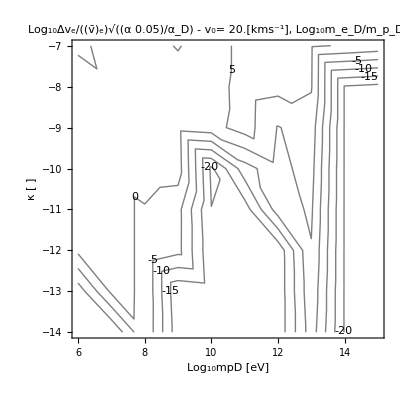

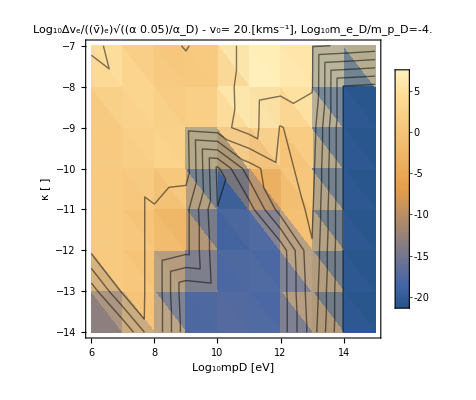

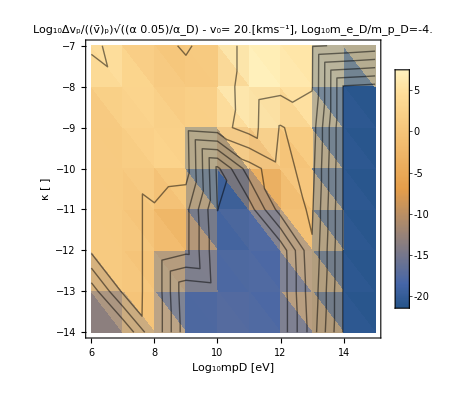

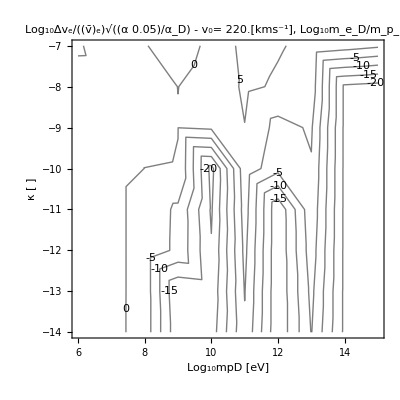

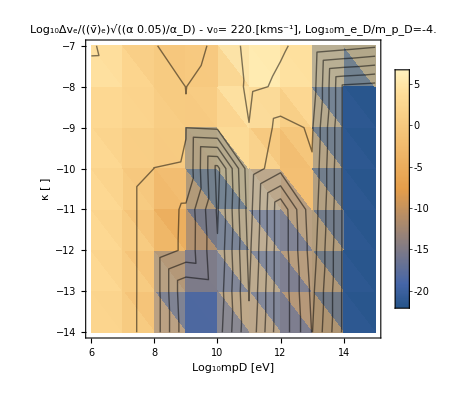

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

```mathematica
PlotKEchangeκContour[{PDicts1MeVKE,PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

```mathematica
PlotNcκContour[{PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

```mathematica
PlotCaptureRateκContour[{PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[{PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

```mathematica
"Γtotal"/.PDicts10GeVKE
```

{7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11}

#### Debug sharp drop offs in capture rate plots

Why is there such a sharp drop off here at a TEV? Ie. why no hard scattering contribution?

```mathematica
Keys@PDicts1TeVKE
```

{{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD},{Pf,κ,mpD,meD,vχMax,βD,v0,PfE,PfNuc,dNcMaxdt,NcMax,timeenoughforequil,Nc,Γtotal,pDvescchange,eDvescchange,ΔpKE/vpbar,ΔeKE/vpbar,Ntot,nD,fD,αD}}

```mathematica
{"dNcMaxdt","Nc",N@Log10@"κ","Γtotal"}/.PDicts1TeVScan
```

{{{7.90068×10^-32 nD,1.104×10^-14 nD,-14.,0.},{7.90068×10^-32 nD,1.104×10^-14 nD,-13.,0.},{7.90068×10^-32 nD,1.104×10^-14 nD,-12.,0.},{7.90068×10^-32 nD,1.104×10^-14 nD,-11.,0.},{7.90068×10^-32 nD,1.104×10^-14 nD,-10.,0.},{7.90068×10^-32 nD,1.104×10^-14 nD,-9.,0.},{7.63678×10^18 nD,1.06713×10^36 nD,-8.,0.},{7.7372×10^18 nD,1.08116×10^36 nD,-7.,0.}},{{4.28282×10^-31 nD,5.98462×10^-14 nD,-14.,0.},{4.28282×10^-31 nD,5.98462×10^-14 nD,-13.,0.},{4.28282×10^-31 nD,5.98462×10^-14 nD,-12.,0.},{4.28282×10^-31 nD,5.98462×10^-14 nD,-11.,0.},{4.28282×10^-31 nD,5.98462×10^-14 nD,-10.,0.},{4.28282×10^-31 nD,5.98462×10^-14 nD,-9.,0.},{4.10677×10^16 nD,5.73861×10^33 nD,-8.,0.},{3.25534×10^18 nD,4.54886×10^35 nD,-7.,0.}},{{7.90412×10^-32 nD,1.10449×10^-14 nD,-14.,0.},{7.90412×10^-32 nD,1.10449×10^-14 nD,-13.,0.},{7.90412×10^-32 nD,1.10449×10^-14 nD,-12.,0.},{7.90412×10^-32 nD,1.10449×10^-14 nD,-11.,0.},{7.90412×10^-32 nD,1.10449×10^-14 nD,-10.,0.},{7.90412×10^-32 nD,1.10449×10^-14 nD,-9.,0.},{7.6369×10^18 nD,1.06715×10^36 nD,-8.,0.},{7.73884×10^18 nD,1.08139×10^36 nD,-7.,0.}},{{4.30316×10^-31 nD,6.01304×10^-14 nD,-14.,0.},{4.30316×10^-31 nD,6.01304×10^-14 nD,-13.,0.},{4.30316×10^-31 nD,6.01304×10^-14 nD,-12.,0.},{4.30316×10^-31 nD,6.01304×10^-14 nD,-11.,0.},{4.30316×10^-31 nD,6.01304×10^-14 nD,-10.,0.},{4.30316×10^-31 nD,6.01304×10^-14 nD,-9.,0.},{4.09633×10^16 nD,5.72403×10^33 nD,-8.,0.},{2.84141×10^18 nD,3.97045×10^35 nD,-7.,0.}}}